## Analytical solution

```mathematica
P(Subscript[τ, 2],Subscript[τ, 3])= (i^3((2 π ℏ Subscript[ω, F])/V))^3 π^2/(|a a'|)^2 Exp(-2 Subscript[σ, F]^2(((3+4 Subscript[σ, F]^4(Subscript[B, 2]^2+Subscript[B, 2] Subscript[B, 3]+Subscript[B, 3]^2))Subscript[τ, 2]^2+(3+4 Subscript[σ, F]^4 (Subscript[B, 1] (Subscript[B, 2]-Subscript[B, 3])+Subscript[B, 2] (2 Subscript[B, 2]+Subscript[B, 3])) ) Subscript[τ, 2] Subscript[τ, 3]+(3+4 Subscript[σ, F]^4(Subscript[B, 2]^2+Subscript[B, 2] Subscript[B, 1]+Subscript[B, 1]^2))Subscript[τ, 3]^2)/(9+8 (Subscript[σ, F]^4)[2 (Subscript[B, 1]^2+Subscript[B, 2]^2+ Subscript[B, 3]^2)+Subscript[B, 1] Subscript[B, 2]+Subscript[B, 2] Subscript[B, 3]+Subscript[B, 3] Subscript[B, 1]]+16 Subscript[σ, F]^8 (Subscript[B, 1] Subscript[B, 2]+Subscript[B, 2] Subscript[B, 3]+Subscript[B, 3] Subscript[B, 1])^2 )))
a=1/σF^2-ⅈ (B2+B3);
aprime=1/σF^2-ⅈ (B1+B3)-1/(4a)(1/σF^2-2ⅈ B3)^2;
bprime=-ⅈ (A1-A3+τ2+τ3-2/(4a)(1/σF^2-2ⅈ B3) (A2-A3+τ3));
cprime=1/(4a)(A2-A3+τ3)^2+ⅈ ω0/3 (2τ2+τ3);
cnprime=cn ((2π ℏ ωF)/V)^(3/2) ⅇ^(ⅈ (Kf1+Kf2+Kf3-ω0 t))√(π^2/(a aprime));
```

## Numerical Results

### (a) Numerical solution

```mathematica
Do[k[i][ω_,ωF_]=KF[i]+A[i] (ω-ωF)+B[i] (ω-ωF)^2,{i,1,3}]
f[ω_,ωF_,σF_]=Exp[-(ω-ωF)^2/(2 σF^2)];
Do[KF[i]=0,{i,1,3}];
Do[A[i]=0,{i,1,3}];
B[1]=10;
B[2]=-20;
B[3]=-30;
ClearAll[int1,result1]
Do[
Do[
int1[τ2,τ3][ω1_,ω2_,ω3_,t_,ωF_,σF_]=f[ω1,ωF,σF]*f[ω2,ωF,σF]*f[ω3,ωF,σF]*Exp[ⅈ (k[1][ω1,ωF]+k[2][ω2,ωF]+k[3][ω3,ωF]-ω1 t -ω2 (t+τ2)-ω3 (t+τ2+τ3))],
{τ3,-10,10,1}
],{τ2,-10,10,1}
]
σFtest=0.1;
Do[
Do[
result1[τ2,τ3]=NIntegrate[int1[τ2,τ3][1/3+ϵ,1/3+δ,1/3-ϵ-δ,0,1/3,σFtest],{ϵ,-1/3,2/3},{δ,-1/3,2/3-ϵ}],
{τ3,-10,10,1}
],{τ2,-10,10,1}
]
resultmat1=Table[Abs[result1[i-11,j-11]]^2,{i,1,21},{j,1,21}];
```

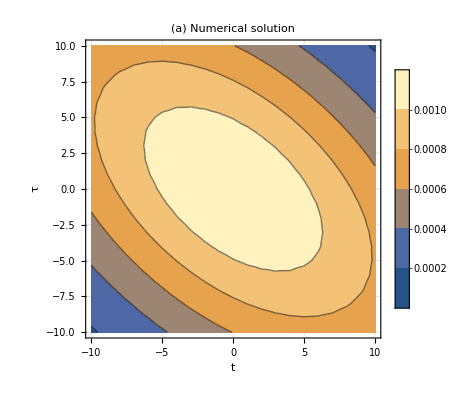

```mathematica
ListContourPlot[resultmat1,DataRange->{{-10,10},{-10,10}}, PlotLegends->Automatic,AxesLabel->{"t","τ"},LabelStyle->{FontFamily->"Times New Roman",FontSize-> 12,Bold,Black},AxesStyle->Thick,GridLines->Automatic ,Axes->True, PlotLabel->"(a) Numerical solution"]
```

### (b) Analytical solution

```mathematica
σFtest=1/10;
numer[σF_,τ2_,τ3_,A1_,A2_,A3_,B1_,B2_,B3_]=((4 σF^4+4 (B2+B3)^2 σF^8) (-3 A3^2-4 A3^2 B1^2 σF^4-4 A3^2 B1 B2 σF^4-4 A3^2 B2^2 σF^4+A2^2 (-3-4 (B1^2+B1 B3+B3^2) σF^4)+A1^2 (-3-4 (B2^2+B2 B3+B3^2) σF^4)+3 A3 τ2+4 A3 B1 B2 σF^4 τ2+8 A3 B2^2 σF^4 τ2-4 A3 B1 B3 σF^4 τ2+4 A3 B2 B3 σF^4 τ2-3 τ2^2-4 B2^2 σF^4 τ2^2-4 B2 B3 σF^4 τ2^2-4 B3^2 σF^4 τ2^2+(6 A3+8 A3 (B1^2+B1 B2+B2^2) σF^4-(3+4 (B1 (B2-B3)+B2 (2 B2+B3)) σF^4) τ2) τ3-(3+4 (B1^2+B1 B2+B2^2) σF^4) τ3^2+A1 (A2 (3+4 (B1 (-B2+B3)+B3 (B2+2 B3)) σF^4)+3 (A3-2 τ2-τ3)+4 σF^4 (A3 B1 (B2-B3)+A3 B2 (2 B2+B3)-2 B2 B3 τ2-B2 (B1+B3) τ3-2 B2^2 (τ2+τ3)+B3 (-2 B3 τ2+B1 τ3)))+A2 (A3 (3+4 (2 B1^2-B2 B3+B1 (B2+B3)) σF^4)+3 (τ2-τ3)+4 σF^4 (-2 B1^2 τ3+B3 (2 B3 τ2+B2 (τ2+τ3))-B1 (B3 (-τ2+τ3)+B2 (τ2+τ3))))));
denom[σF_,τ2_,τ3_,A1_,A2_,A3_,B1_,B2_,B3_]=((2 σF^2+2 (B2+B3)^2 σF^6) (9+8 (2 B1^2+2 B2^2+B2 B3+2 B3^2+B1 (B2+B3)) σF^4+16 (B2 B3+B1 (B2+B3))^2 σF^8));
resultmatold=(π^2/Abs[(1/σFtest^2-ⅈ (-20-30)) (1/σFtest^2-ⅈ (10-30)-1/(4(1/σFtest^2-ⅈ (-20-30)))(1/σFtest^2-2ⅈ (-30))^2)])Table[N[Exp[numer[σFtest,τ2-11,τ3-11,0,0,0,10,-20,-30]/denom[σFtest,τ2-11,τ3-11,0,0,0,10,-20,-30]]],{τ2,1,21},{τ3,1,21}];
```

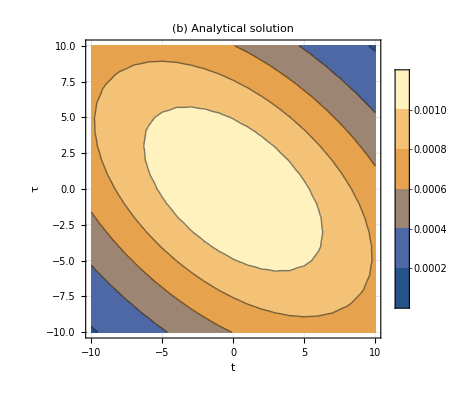

```mathematica
ListContourPlot[resultmatold,DataRange->{{-10,10},{-10,10}}, PlotLegends->Automatic,AxesLabel->{"t","τ"},LabelStyle->{FontFamily->"Times New Roman",FontSize-> 12,Bold,Black},AxesStyle->Thick,GridLines->Automatic ,Axes->True, PlotLabel->"(b) Analytical solution"]
```

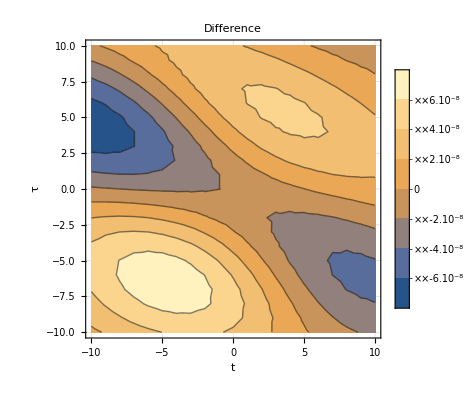

```mathematica
ListContourPlot[resultmat1-resultmatold,DataRange->{{-10,10},{-10,10}}, PlotLegends->Automatic,AxesLabel->{"t","τ"},LabelStyle->{FontFamily->"Times New Roman",FontSize-> 12,Bold,Black},AxesStyle->Thick,GridLines->Automatic ,Axes->True,PlotLabel-> "Difference"]
```

```mathematica
Sum[resultmatold[[n,m]],{n,1,21},{m,1,21}]
```

0.0000390665

### Larger range range = 50, σFtest = 0.1

```mathematica
Do[k[i][ω_,ωF_]=KF[i]+A[i] (ω-ωF)+B[i] (ω-ωF)^2,{i,1,3}]
f[ω_,ωF_,σF_]=Exp[-(ω-ωF)^2/(2 σF^2)];
Do[KF[i]=0,{i,1,3}];
Do[A[i]=0,{i,1,3}];
B[1]=10;
B[2]=-20;
B[3]=-30;
range=50;
σFtest=0.1;
```

```mathematica
ClearAll[int1,result1]
Do[
Do[
int1[τ2,τ3][ω1_,ω2_,ω3_,t_,ωF_,σF_]=f[ω1,ωF,σF]*f[ω2,ωF,σF]*f[ω3,ωF,σF]*Exp[ⅈ (k[1][ω1,ωF]+k[2][ω2,ωF]+k[3][ω3,ωF]-ω1 t -ω2 (t+τ2)-ω3 (t+τ2+τ3))],
{τ3,-range,range,1}
],{τ2,-range,range,1}
]
```

```mathematica
Monitor[Do[
Do[
result1[τ2,τ3]=NIntegrate[int1[τ2,τ3][1/3+ϵ,1/3+δ,1/3-ϵ-δ,0,1/3,σFtest],{ϵ,-1/3,2/3},{δ,-1/3,2/3-ϵ}];result1[-τ2,-τ3]=result1[τ2,τ3]
,{τ2,-range,range,1}],{τ3,0,range,1}],{τ2,τ3}]
resultMatNumerical=Table[Abs[result1[i-range -1,j-range -1]]^2,{i,1,2 range +1},{j,1,2 range +1}];
```

```mathematica
range=50;
σFtest=0.1;
numer[σF_,τ2_,τ3_,A1_,A2_,A3_,B1_,B2_,B3_]=((4 σF^4+4 (B2+B3)^2 σF^8) (-3 A3^2-4 A3^2 B1^2 σF^4-4 A3^2 B1 B2 σF^4-4 A3^2 B2^2 σF^4+A2^2 (-3-4 (B1^2+B1 B3+B3^2) σF^4)+A1^2 (-3-4 (B2^2+B2 B3+B3^2) σF^4)+3 A3 τ2+4 A3 B1 B2 σF^4 τ2+8 A3 B2^2 σF^4 τ2-4 A3 B1 B3 σF^4 τ2+4 A3 B2 B3 σF^4 τ2-3 τ2^2-4 B2^2 σF^4 τ2^2-4 B2 B3 σF^4 τ2^2-4 B3^2 σF^4 τ2^2+(6 A3+8 A3 (B1^2+B1 B2+B2^2) σF^4-(3+4 (B1 (B2-B3)+B2 (2 B2+B3)) σF^4) τ2) τ3-(3+4 (B1^2+B1 B2+B2^2) σF^4) τ3^2+A1 (A2 (3+4 (B1 (-B2+B3)+B3 (B2+2 B3)) σF^4)+3 (A3-2 τ2-τ3)+4 σF^4 (A3 B1 (B2-B3)+A3 B2 (2 B2+B3)-2 B2 B3 τ2-B2 (B1+B3) τ3-2 B2^2 (τ2+τ3)+B3 (-2 B3 τ2+B1 τ3)))+A2 (A3 (3+4 (2 B1^2-B2 B3+B1 (B2+B3)) σF^4)+3 (τ2-τ3)+4 σF^4 (-2 B1^2 τ3+B3 (2 B3 τ2+B2 (τ2+τ3))-B1 (B3 (-τ2+τ3)+B2 (τ2+τ3))))));
denom[σF_,τ2_,τ3_,A1_,A2_,A3_,B1_,B2_,B3_]=((2 σF^2+2 (B2+B3)^2 σF^6) (9+8 (2 B1^2+2 B2^2+B2 B3+2 B3^2+B1 (B2+B3)) σF^4+16 (B2 B3+B1 (B2+B3))^2 σF^8));resultMatAnalytical=(π^2/Abs[(1/σFtest^2-ⅈ (B[2]+B[3])) (1/σFtest^2-ⅈ (B[1]+B[3])-(1/(4(1/σFtest^2-ⅈ (B[2]+B[3]))))(1/σFtest^2-2ⅈ (B[3]))^2)])Table[N[Exp[numer[σFtest,τ2-range -1,τ3-range -1,0,0,0,B[1],B[2],B[3]]/denom[σFtest,τ2-range -1,τ3-range -1,0,0,0,B[1],B[2],B[3]]]],{τ2,1,2 range +1},{τ3,1,2 range +1}];
```

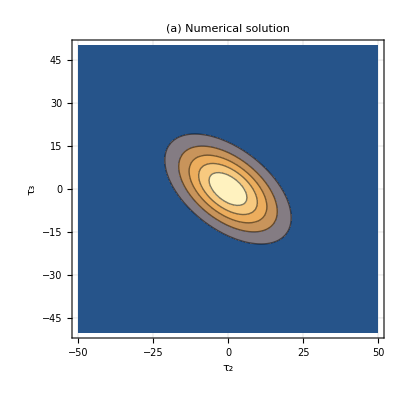

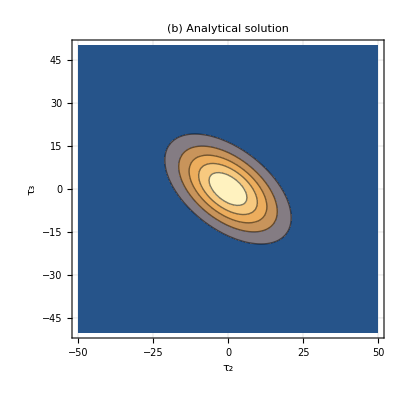

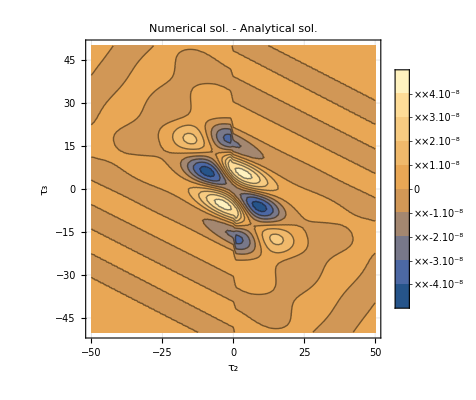

```mathematica
ListContourPlot[resultMatnumerical550,DataRange->{{-range,range},{-range,range}},AxesLabel->{"τ_2","τ_3"},LabelStyle->{FontFamily->"Times New Roman",FontSize-> 15,Bold,Black},AxesStyle->Thick,GridLines->Automatic ,Axes->True, PlotLabel->"(a) Numerical solution",PlotRange->Full]
ListContourPlot[resultMatAnalytical,DataRange->{{-range,range},{-range,range}}, AxesLabel->{"τ_2","τ_3"},LabelStyle->{FontFamily->"Times New Roman",FontSize-> 15,Bold,Black},AxesStyle->Thick,GridLines->Automatic ,Axes->True, PlotLabel->"(b) Analytical solution",PlotRange->Full]
ListContourPlot[resultMatnumerical50-resultMatAnalytical,DataRange->{{-range,range},{-range,range}}, AxesLabel->{"τ_2","τ_3"},LabelStyle->{FontFamily->"Times New Roman",FontSize-> 15,Bold,Black},AxesStyle->Thick,GridLines->Automatic ,Axes->True, PlotLabel->"Numerical sol. - Analytical sol.",PlotLegends-> Automatic,PlotRange->Full]
```

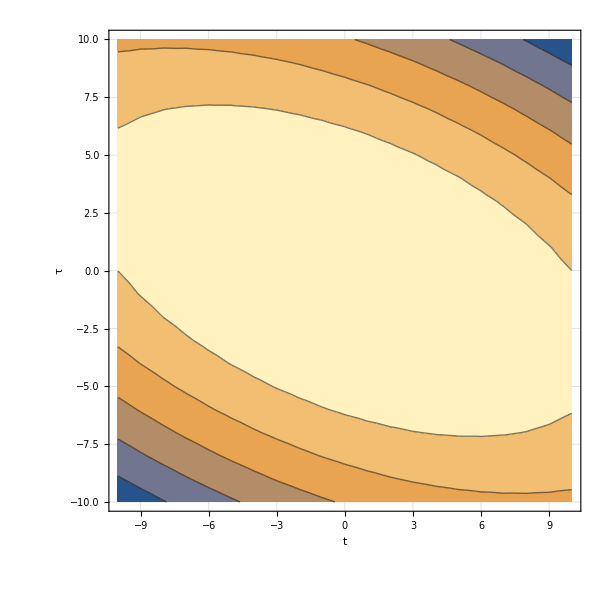

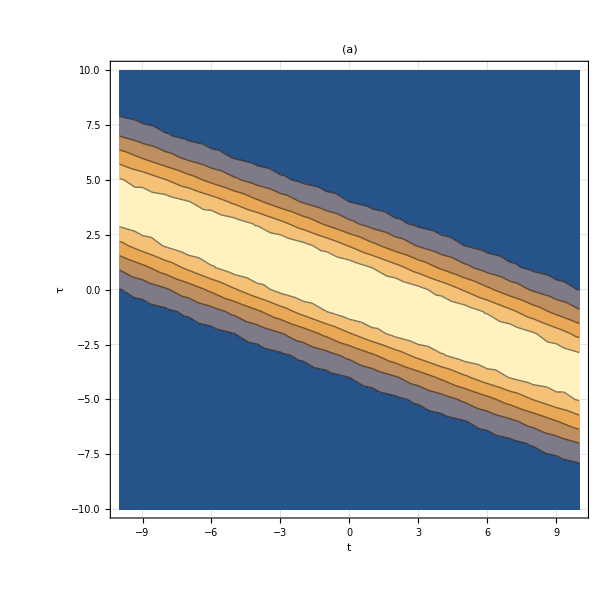

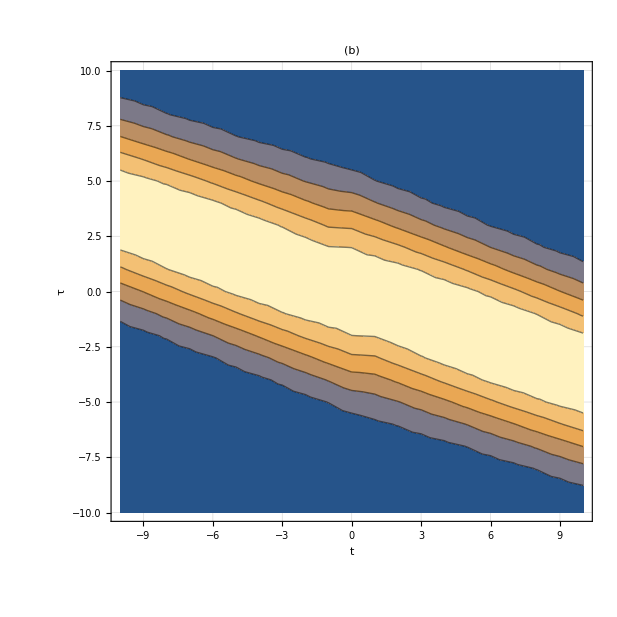

```mathematica
Classical[σF_,t_,τ_,A1_,A2_,A3_,B1_,B2_,B3_]:=Exp[1/((3+8 σF^4 (B1^2+B2^2+B3^2+2 (B2^2 B3^2+B1^2 (B2^2+B3^2)) σF^4))/σF^2)(-t^2 (1+2 B2^2 σF^4+2 B3^2 σF^4)- (-A2 A3+A3^2-4 A2 A3 B1^2 σF^4+2 A3^2 B1^2 σF^4+2 A3^2 B2^2 σF^4-A1 A3 (1+4 B2^2 σF^4)-A1 A2 (1+4 B3^2 σF^4)+A2^2 (1+2 (B1^2+B3^2) σF^4)+A1^2 (1+2 (B2^2+B3^2) σF^4))- (A1+A2-2 A3+4 A2 B1^2 σF^4+4 A1 B2^2 σF^4-4 A3 (B1^2+B2^2) σF^4) τ-(1+2 (B1^2+B2^2) σF^4) τ^2+t (- (2 A1-A2-A3+4 A1 B2^2 σF^4-4 A3 B2^2 σF^4+4 A1 B3^2 σF^4-4 A2 B3^2 σF^4)-(1+4 B2^2 σF^4) τ))];
range=10;
B[1]=10;
B[2]=-20;
B[3]=-30;
σFtest=0.5;
resultClassical=Table[N[Classical[σFtest,τ2-range -1,τ3-range -1,0,0,0,10,-20,-30]],{τ2,1,2 range +1},{τ3,1,2 range +1}];
resultClassical=resultClassical/Total[Total[resultClassical]];
ListContourPlot[resultClassical,DataRange->{{-range,range},{-range,range}}, AxesLabel->{"t","τ"},LabelStyle->{FontSize->60,FontFamily->"Times", ,Black},AxesStyle->Thick,GridLines->Automatic ,Axes->True,PlotRange->Full,Contours-> 5,ImageSize->Scaled[0.5]]
numer[σF_,τ2_,τ3_,A1_,A2_,A3_,B1_,B2_,B3_]=((4 σF^4+4 (B2+B3)^2 σF^8) (-3 A3^2-4 A3^2 B1^2 σF^4-4 A3^2 B1 B2 σF^4-4 A3^2 B2^2 σF^4+A2^2 (-3-4 (B1^2+B1 B3+B3^2) σF^4)+A1^2 (-3-4 (B2^2+B2 B3+B3^2) σF^4)+3 A3 τ2+4 A3 B1 B2 σF^4 τ2+8 A3 B2^2 σF^4 τ2-4 A3 B1 B3 σF^4 τ2+4 A3 B2 B3 σF^4 τ2-3 τ2^2-4 B2^2 σF^4 τ2^2-4 B2 B3 σF^4 τ2^2-4 B3^2 σF^4 τ2^2+(6 A3+8 A3 (B1^2+B1 B2+B2^2) σF^4-(3+4 (B1 (B2-B3)+B2 (2 B2+B3)) σF^4) τ2) τ3-(3+4 (B1^2+B1 B2+B2^2) σF^4) τ3^2+A1 (A2 (3+4 (B1 (-B2+B3)+B3 (B2+2 B3)) σF^4)+3 (A3-2 τ2-τ3)+4 σF^4 (A3 B1 (B2-B3)+A3 B2 (2 B2+B3)-2 B2 B3 τ2-B2 (B1+B3) τ3-2 B2^2 (τ2+τ3)+B3 (-2 B3 τ2+B1 τ3)))+A2 (A3 (3+4 (2 B1^2-B2 B3+B1 (B2+B3)) σF^4)+3 (τ2-τ3)+4 σF^4 (-2 B1^2 τ3+B3 (2 B3 τ2+B2 (τ2+τ3))-B1 (B3 (-τ2+τ3)+B2 (τ2+τ3))))));
denom[σF_,τ2_,τ3_,A1_,A2_,A3_,B1_,B2_,B3_]=((2 σF^2+2 (B2+B3)^2 σF^6) (9+8 (2 B1^2+2 B2^2+B2 B3+2 B3^2+B1 (B2+B3)) σF^4+16 (B2 B3+B1 (B2+B3))^2 σF^8));resultMatAnalytical=(π^2/Abs[(1/σFtest^2-ⅈ (B[2]+B[3])) (1/σFtest^2-ⅈ (B[1]+B[3])-(1/(4(1/σFtest^2-ⅈ (B[2]+B[3]))))(1/σFtest^2-2ⅈ (B[3]))^2)])Table[N[Exp[numer[σFtest,τ2-range -1,τ3-range -1,0,0,0,B[1],B[2],B[3]]/denom[σFtest,τ2-range -1,τ3-range -1,0,0,0,B[1],B[2],B[3]]]],{τ2,1,2 range +1},{τ3,1,2 range +1}];
resultMatAnalytical=resultMatAnalytical/Total[Total[resultMatAnalytical]];
ListContourPlot[resultMatAnalytical,DataRange->{{-range,range},{-range,range}}, AxesLabel->{"t","τ"},LabelStyle->{FontSize->60,FontFamily->"Times", ,Black},AxesStyle->Thick,GridLines->Automatic ,Axes->True, PlotLabel->"(a)",PlotRange->Full,Contours->5,ImageSize->Scaled[0.5]]
Do[k[i][ω_,ωF_]=KF[i]+A[i] (ω-ωF)+B[i] (ω-ωF)^2,{i,1,3}]
f[ω_,ωF_,σF_]=Exp[-(ω-ωF)^2/(2 σF^2)];
Do[KF[i]=0,{i,1,3}];
Do[A[i]=0,{i,1,3}];
ClearAll[int2,result2]
Do[
Do[
int2[τ2,τ3][ω1_,ω2_,ω3_,t_,ωF_,σF_]=f[ω1,ωF,σF]*f[ω2,ωF,σF]*f[ω3,ωF,σF]*Exp[ⅈ (k[1][ω1,ωF]+k[2][ω2,ωF]+k[3][ω3,ωF]-ω1 t -ω2 (t+τ2)-ω3 (t+τ2+τ3))],
{τ3,-range,range,1}
],{τ2,-range,range,1}
]
Monitor[Do[
Do[
result2[τ2,τ3]=NIntegrate[int2[τ2,τ3][1/3+ϵ,1/3+δ,1/3-ϵ-δ,0,1/3,σFtest],{ϵ,-1/3,2/3},{δ,-1/3,2/3-ϵ}];result2[-τ2,-τ3]=result2[τ2,τ3]
,{τ2,-range,range,1}],{τ3,0,range,1}],{τ2,τ3}]
resultMatNumerical2=Table[Abs[result2[i-range -1,j-range -1]]^2,{i,1,2 range +1},{j,1,2 range +1}];
resultMatNumerical2 = resultMatNumerical2/Total[Total[resultMatNumerical2]];
ListContourPlot[resultMatNumerical2,DataRange->{{-range,range},{-range,range}}, AxesLabel->{"t","τ"},LabelStyle->{FontSize->60,FontFamily->"Times", ,Black},AxesStyle->Thick,GridLines->Automatic ,Axes->True, PlotLabel->"(b)",PlotRange->Full,Contours->5,ImageSize->Scaled[0.5]]
```

```mathematica
Total[Total[resultClassical]]
```

1.

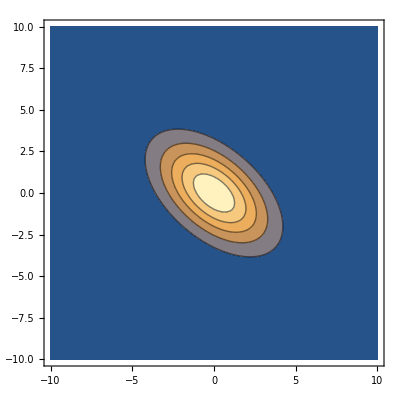

```mathematica
ListContourPlot[resultMatnumerical50,PlotRange->Full,DataRange->{{-10,10},{-10,10}},Axes->True]
```

## Result

```mathematica
resultMatnumerical50={{2.2324611704901758*^-18,3.4371135208433995*^-18,5.247914636060909*^-18,7.945214677855573*^-18,1.192576180475941*^-17,1.7744310156543003*^-17,2.616707619643718*^-17,3.8239429754573556*^-17,5.5370779347914493*^-17,7.944094939472704*^-17,1.1293527569726413*^-16,1.591216144397251*^-16,2.222938544234751*^-16,3.081261979584146*^-16,4.242148351750939*^-16,5.809327982738854*^-16,7.927932560563035*^-16,1.0806072105520907*^-15,1.4748283564726162*^-15,2.020584041684529*^-15,2.784968142416287*^-15,3.8671695851947005*^-15,5.411861489014445*^-15,7.625909706524565*^-15,1.0797800305700753*^-14,1.5318235196049997*^-14,2.1699183798168997*^-14,3.058762558426945*^-14,4.2769849352941*^-14,5.916354034588122*^-14,8.079945365539562*^-14,1.0880429686663491*^-13,1.4441395277239005*^-13,1.8907397456416656*^-13,2.447246731630279*^-13,3.144224313226079*^-13,4.0351661898486845*^-13,5.21679489017166*^-13,6.861679614639413*^-13,9.267706755928158*^-13,1.2929466410507135*^-12,1.863676006206098*^-12,2.7605006177228904*^-12,4.164115566954953*^-12,6.334671125228474*^-12,9.635653537787178*^-12,1.456084004274876*^-11,2.1763386397008644*^-11,3.2085633540252294*^-11,4.658775059319462*^-11,6.657290489648695*^-11,1.041417082717043*^-10,1.4088741358906126*^-10,1.880095244510235*^-10,2.476893889180591*^-10,3.223647835536062*^-10,4.147019352379988*^-10,5.275445498230651*^-10,6.638351085794533*^-10,8.26504415519852*^-10,1.0183268732079762*^-9,1.241741357592388*^-9,1.4986408909111355*^-9,1.7901384851926224*^-9,2.1163212822344695*^-9,2.4760099975146598*^-9,2.8665450482309095*^-9,3.283623839932708*^-9,3.7212146853725658*^-9,4.1715710080885416*^-9,4.625364353420743*^-9,5.071946221484992*^-9,5.499737274785657*^-9,5.896729089585019*^-9,6.251069837590837*^-9,6.5516929967004546*^-9,6.788939356936002*^-9,6.95511890665968*^-9,7.0449617479583096*^-9,7.055916180016122*^-9,6.988266688015847*^-9,6.845062961810234*^-9,6.631870719121748*^-9,6.356373228487162*^-9,6.027866344923249*^-9,5.656697731564606*^-9,5.253701833770888*^-9,4.829676452768847*^-9,4.394935883082279*^-9,3.958961688562736*^-9,3.5301579377790077*^-9,3.1157054630227614*^-9,2.721500434717837*^-9,2.3521585927725494*^-9,2.0110657665989846*^-9,1.7004579679726632*^-9,1.421519576471909*^-9,1.1744923404230702*^-9,9.587918011727383*^-10,7.731310779662524*^-10,6.156509611280094*^-10},{2.2713788205015954*^-18,3.494224909572596*^-18,5.329192873627439*^-18,8.0565207357362*^-18,1.2070758145282252*^-17,1.7920653388139817*^-17,2.636043487627237*^-17,3.841554260613318*^-17,5.546766779140707*^-17,7.936753207707372*^-17,1.1259081175197073*^-16,1.5846504089965077*^-16,2.215164306801899*^-16,3.080190084448577*^-16,4.268782805453817*^-16,5.910505316097623*^-16,8.197868148763831*^-16,1.142090665865464*^-15,1.6018746362454533*^-15,2.2653599812104595*^-15,3.23124161891556*^-15,4.643971425727687*^-15,6.710138333207487*^-15,9.71729601863854*^-15,1.4053747730439069*^-14,2.022691553203561*^-14,2.887741192048192*^-14,4.078658633200141*^-14,5.687842183982531*^-14,7.822402204286288*^-14,1.0607109670073555*^-13,1.4194471958028016*^-13,1.8790245176779277*^-13,2.4707954117113846*^-13,3.247301438978875*^-13,4.3005812945554603*^-13,5.792326501882142*^-13,8.000918732171647*^-13,1.139140887278621*^-12,1.6715300227041092*^-12,2.5147369587073693*^-12,3.846647467309084*^-12,5.928613690221468*^-12,9.133848027118813*^-12,1.3981175374241434*^-11,2.1173717503580855*^-11,3.164153412234359*^-11,4.658662029951065*^-11,6.752799413385154*^-11,9.634394105494823*^-11,1.3530785325576713*^-10,2.006777717454788*^-10,2.68338886264163*^-10,3.544670330458142*^-10,4.62815516679129*^-10,5.975365322888779*^-10,7.631141301803222*^-10,9.642549196171966*^-10,1.2057299945959097*^-9,1.492163645949034*^-9,1.827767757084671*^-9,2.2160254245136886*^-9,2.6593331982452814*^-9,3.158618096188072*^-9,3.712952662022798*^-9,4.319198023638935*^-9,4.971710173916353*^-9,5.66214745360489*^-9,6.379416384519938*^-9,7.109787760912595*^-9,7.837204846731585*^-9,8.54379084739271*^-9,9.210544518873156*^-9,9.81819254403055*^-9,1.0348147545727577*^-8,1.0783504023259627*^-8,1.1109993817268957*^-8,1.1316820080880251*^-8,1.1397295379889293*^-8,1.1349225375553402*^-8,1.1175002997281344*^-8,1.0881406302058075*^-8,1.047912258379466*^-8,9.98204772966275*^-9,9.406429719075708*^-9,8.769935935506011*^-9,8.090724568247371*^-9,7.386591386952214*^-9,6.674246737229436*^-9,5.96875672694372*^-9,5.283161063727758*^-9,4.628260568409845*^-9,4.012553447756871*^-9,3.4422901176400916*^-9,2.921615262045991*^-9,2.4527665699467927*^-9,2.036306478715226*^-9,1.6713689949123095*^-9,1.355909565607397*^-9,1.0869515786544926*^-9,8.608247630576957*^-10},{2.306469636754702*^-18,3.54280174517518*^-18,5.392916431275751*^-18,8.133988551597465*^-18,1.2154230518372232*^-17,1.7991439660938443*^-17,2.6383792267180133*^-17,3.833813322874279*^-17,5.522510852769823*^-17,7.891809522757642*^-17,1.1200601781013295*^-16,1.5813203462266914*^-16,2.2254367175111195*^-16,3.129894951191308*^-16,4.4116403466868923*^-16,6.249863566712327*^-16,8.920898755616028*^-16,1.2849848066810245*^-15,1.8684002612357294*^-15,2.7392744934395696*^-15,4.039689395863794*^-15,5.9726894206198164*^-15,8.82038552863113*^-15,1.2963108739644037*^-14,1.8897917516435273*^-14,2.7255063250358414*^-14,3.8813061460187347*^-14,5.4518437375848394*^-14,7.552725334807113*^-14,1.0330525852057469*^-13,1.398555419958474*^-13,1.881909123166443*^-13,2.5323655060661977*^-13,3.4343936687328596*^-13,4.734742219231169*^-13,6.685705793762383*^-13,9.711282887281117*^-13,1.450434655983746*^-12,2.2164173973095204*^-12,3.4384452070737007*^-12,5.370191686831239*^-12,8.381480997233221*^-12,1.2997809266473981*^-11,1.9947865604213518*^-11,3.021885129487631*^-11,4.5118717568381116*^-11,6.634362568412283*^-11,9.604800210219995*^-11,1.3691354903801952*^-10,1.922125137915308*^-10,2.658594619500163*^-10,3.7755662162197796*^-10,5.004873001349903*^-10,6.560276393256103*^-10,8.505673291974133*^-10,1.0910855467511578*^-9,1.3850013028279772*^-9,1.7399491458384892*^-9,2.1634726618255475*^-9,2.662632976535432*^-9,3.2435360930285695*^-9,3.910791249977956*^-9,4.666922161038465*^-9,5.511763299894372*^-9,6.44188332044798*^-9,7.450085985484957*^-9,8.525044164919835*^-9,9.651123116646523*^-9,1.080844410701025*^-8,1.197322768542919*^-8,1.3118437476875695*^-8,1.4214721074858973*^-8,1.5231616304226372*^-8,1.6138961656253752*^-8,1.690842256080973*^-8,1.751502424721817*^-8,1.793857072506214*^-8,1.816483056059193*^-8,1.8186384710916193*^-8,1.800305894996647*^-8,1.762190068420108*^-8,1.7056702806641244*^-8,1.6327120253144845*^-8,1.5457462459401586*^-8,1.4475272097861705*^-8,1.3409813997233631*^-8,1.2290596834113337*^-8,1.114603520610422*^-8,1.0002334152193176*^-8,8.882646578889415*^-9,7.806521363348843*^-9,6.789630630962405*^-9,5.843742416628323*^-9,4.976890464039867*^-9,4.193688928349544*^-9,3.4957399018280044*^-9,2.8820905014406625*^-9,2.3497049464099425*^-9,1.8939263806646755*^-9,1.508912784651859*^-9,1.188036695746169*^-9},{2.3335833668910117*^-18,3.57570209437006*^-18,5.427578036826875*^-18,8.160593408257768*^-18,1.2154068614415278*^-17,1.7934652814850633*^-17,2.623173925871156*^-17,3.8058840732377104*^-17,5.48388343833979*^-17,7.860447636132476*^-17,1.1232750111078114*^-16,1.604627782633467*^-16,2.2984186972445987*^-16,3.3111376685924367*^-16,4.810083704367443*^-16,7.057821288984017*^-16,1.0462777504885957*^-15,1.5650642181639796*^-15,2.3560798218107725*^-15,3.557041942654476*^-15,5.364592383296777*^-15,8.051756256367225*^-15,1.1986976792584221*^-14,1.7654137276343594*^-14,2.5674371226669177*^-14,3.6834355448452586*^-14,5.213419784528719*^-14,7.288376839162706*^-14,1.009031250812437*^-13,1.3892508187001567*^-13,1.9136093260851762*^-13,2.6567875638248514*^-13,3.7476127504028935*^-13,5.407582776595978*^-13,8.011246345974651*^-13,1.2177310903060597*^-12,1.8901369859605956*^-12,2.974300455201423*^-12,4.708144165251002*^-12,7.445459802283132*^-12,1.1699585499439928*^-11,1.819809098940097*^-11,2.794932263433426*^-11,4.23210689589632*^-11,6.31307902439169*^-11,9.274580644258129*^-11,1.3419055997385038*^-10,1.912565768958167*^-10,2.6860906674208154*^-10,3.7188226695544196*^-10,5.077537179301446*^-10,6.975174682897326*^-10,9.183749629538039*^-10,1.1963003906640056*^-9,1.5420142989022443*^-9,1.967047347064195*^-9,2.483426831992502*^-9,3.1032368988047823*^-9,3.838046476325141*^-9,4.698208588410196*^-9,5.692046813884288*^-9,6.824958733188759*^-9,8.09848124816778*^-9,9.50937735395452*^-9,1.1048816588259809*^-8,1.2701730069097485*^-8,1.4446423812463966*^-8,1.6254529116524716*^-8,1.8091354977954168*^-8,1.991668430017987*^-8,2.1686023750746067*^-8,2.3352278448609228*^-8,2.4867780527570852*^-8,2.618655938661036*^-8,2.7266706252443576*^-8,2.8072661665250304*^-8,2.8577246033363007*^-8,2.8763263360418794*^-8,2.862453713215792*^-8,2.8166283158377856*^-8,2.740478225599666*^-8,2.6366379355993824*^-8,2.508589708009226*^-8,2.3604603378247967*^-8,2.1967908017110422*^-8,2.0222977522233152*^-8,1.84164516911924*^-8,1.6592419083609267*^-8,1.4790768777926181*^-8,1.3045987644260053*^-8,1.1386423406257649*^-8,9.833990185671323*^-9,8.404259681370535*^-9,7.106859813505756*^-9,5.946094826716028*^-9,4.921702081309346*^-9,4.029672063539313*^-9,3.26307255642994*^-9,2.61283278361456*^-9,2.0684592390819607*^-9,1.618666222005541*^-9},{2.347410514006612*^-18,3.584883307339286*^-18,5.422424313170235*^-18,8.125096386722116*^-18,1.2066272724700162*^-17,1.777329200112391*^-17,2.5998149979316758*^-17,3.783153156347774*^-17,5.4891960507587966*^-17,7.964319764498546*^-17,1.1592512379357612*^-16,1.698284688149791*^-16,2.511032809746136*^-16,3.7536199864113605*^-16,5.67413598528736*^-16,8.661283150665413*^-16,1.3312611652580094*^-15,2.0526259406476453*^-15,3.1618919099931616*^-15,4.847084463204685*^-15,7.369708792778676*^-15,1.1084549699742897*^-14,1.6463169618010714*^-14,2.4124941723830433*^-14,3.4885715938473695*^-14,4.9846426746855946*^-14,7.05655784040603*^-14,9.939520739588733*^-14,1.4011527245440676*^-13,1.9908283673318857*^-13,2.8722629770558164*^-13,4.2336678114680543*^-13,6.395416883101198*^-13,9.892382865701621*^-13,1.5597112919300287*^-12,2.4898432772186685*^-12,3.9952875041351924*^-12,6.40287765146795*^-12,1.0196457694603386*^-11,1.607633135846084*^-11,2.50344031244211*^-11,3.84467298449424*^-11,5.818457260063314*^-11,8.674408569698625*^-11,1.27393461820789*^-10,1.8433463488131457*^-10,2.6287450173279933*^-10,3.6959805443626723*^-10,5.125328411123749*^-10,7.012908684935072*^-10,9.471705729116462*^-10,1.2700701633662353*^-9,1.6627671133831548*^-9,2.1542852382117483*^-9,2.762294041493876*^-9,3.5054583828861066*^-9,4.402817461639522*^-9,5.472959307923755*^-9,6.732992769981502*^-9,8.197336748534517*^-9,9.876367148986819*^-9,1.1774984318036703*^-8,1.3891185706511905*^-8,1.62147478101581*^-8,1.8726135460812107*^-8,2.139576259662948*^-8,2.4183724295003376*^-8,2.704010329595445*^-8,2.9905924641869086*^-8,3.27147899112452*^-8,3.539516997114376*^-8,3.787327605805978*^-8,4.0076368719238425*^-8,4.1936309336849646*^-8,4.3393116641841764*^-8,4.439826736834908*^-8,4.491748105591753*^-8,4.4932756451974846*^-8,4.4443480183228033*^-8,4.346650310916997*^-8,4.2035168306362936*^-8,4.0197367100487675*^-8,3.801278487556007*^-8,3.55495663170738*^-8,3.2880672122691653*^-8,3.008021165785263*^-8,2.7220018233475246*^-8,2.4366689607456334*^-8,2.15792533101173*^-8,1.8907543840108767*^-8,1.6391306509228643*^-8,1.4059979330091323*^-8,1.193305617913538*^-8,1.0020904331617297*^-8,8.32589890563693*^-9,6.843739767186429*^-9,5.564833905610752*^-9,4.475649530299703*^-9,3.5599721616808957*^-9,2.8000185833837456*^-9,2.1773847697937803*^-9},{2.3428950240673733*^-18,3.5648166465563086*^-18,5.374938152170695*^-18,8.03731498315108*^-18,1.1934379618482882*^-17,1.7629238207879472*^-17,2.5970174251893864*^-17,3.8268618489964507*^-17,5.660231778504886*^-17,8.432563177872449*^-17,1.2691098168844095*^-16,1.9330003064625899*^-16,2.9800772886253416*^-16,4.642898533496755*^-16,7.287424165433462*^-16,1.1477310014161714*^-15,1.8060351964321972*^-15,2.8280415226487995*^-15,4.391783464978796*^-15,6.746282900629323*^-15,1.0233373910623932*^-14,1.531722040047215*^-14,2.262934775622557*^-14,3.3046223892916764*^-14,4.783334200290192*^-14,6.891863372301595*^-14,9.940466691474982*^-14,1.4450048149016012*^-13,2.1315833657488075*^-13,3.2084669028361164*^-13,4.940863888514111*^-13,7.776281526564067*^-13,1.2454576897225373*^-12,2.0171756348864324*^-12,3.2817000652829656*^-12,5.3306564360695525*^-12,8.604218700145788*^-12,1.3752499539135078*^-11,2.1715798488488232*^-11,3.382703529705999*^-11,5.1939443283740016*^-11,7.858198740696458*^-11,1.1714391090627993*^-10,1.7208820591374746*^-10,2.4919155043871677*^-10,3.5580526844756025*^-10,5.011280879409511*^-10,6.964768787222302*^-10,9.55536213838251*^-10,1.2945617243821011*^-9,1.7325061536681935*^-9,2.284303098342663*^-9,2.9753107289721858*^-9,3.835371227160192*^-9,4.8930204735939905*^-9,6.1777810809548146*^-9,7.718990676218665*^-9,9.544314040416048*^-9,1.1677961989575757*^-8,1.413867056076259*^-8,1.6937527434935646*^-8,2.0075765831278768*^-8,2.3542675956501798*^-8,2.7313806710468244*^-8,3.1349641959052314*^-8,3.559493280180532*^-8,3.9978847307068744*^-8,4.4416060826540194*^-8,4.880885361910199*^-8,5.305021064685657*^-8,5.702783569394524*^-8,6.062890524659185*^-8,6.374530535335164*^-8,6.627902640507955*^-8,6.814734566213495*^-8,6.928741326069315*^-8,6.965987937780037*^-8,6.925125923578524*^-8,6.807482538091551*^-8,6.616993478896651*^-8,6.359982999413976*^-8,6.044808389245947*^-8,5.6813972227080844*^-8,5.280714257175989*^-8,4.8541994427133903*^-8,4.4132187427160645*^-8,3.968565516078094*^-8,3.530042775856121*^-8,3.106146840277306*^-8,2.7038620806918833*^-8,2.3285660065808327*^-8,1.9840349755766116*^-8,1.6725341716217793*^-8,1.3949715835829788*^-8,1.1510944083028046*^-8,9.39707446240041*^-9,7.588955077503546*^-9,6.062359142599221*^-9,4.789908303740551*^-9,3.742732765212479*^-9,2.8918383306454677*^-9},{2.318605132455044*^-18,3.519510350931811*^-18,5.304641108252034*^-18,7.95389212099303*^-18,1.18953071100556*^-17,1.7801055886311893*^-17,2.6753907350812665*^-17,4.053341162901423*^-17,6.209893121587333*^-17,9.638523479757714*^-17,1.5157584254839169*^-16,2.41077632639157*^-16,3.8648200112879937*^-16,6.218535636394241*^-16,9.997292882865418*^-16,1.599238126385951*^-15,2.5368012834688962*^-15,3.980050822656362*^-15,6.166175285152391*^-15,9.427379535499284*^-15,1.4229490781502038*^-14,2.1236562138721244*^-14,3.142713514548619*^-14,4.6310449898030787*^-14,6.832859160609743*^-14,1.0159051351042112*^-13,1.5317496707648804*^-13,2.35372218417179*^-13,3.6942064251955775*^-13,5.915454658712242*^-13,9.624329660853985*^-13,1.5816805215457262*^-12,2.6092507937363574*^-12,4.296517697696677*^-12,7.030101409507018*^-12,1.1392313633328986*^-11,1.8242620013557697*^-11,2.8825002652620445*^-11,4.490638028535333*^-11,6.895120355699793*^-11,1.0433685157318382*^-10,1.5561335475165866*^-10,2.288090776573915*^-10,3.317811209560071*^-10,4.746051513649888*^-10,6.699939784311868*^-10,9.33727373616892*^-10,1.2850674105921369*^-9,1.7471242080894285*^-9,2.3471269660091247*^-9,3.1165453308019384*^-9,4.062629416626163*^-9,5.26534450165636*^-9,6.753355828954849*^-9,8.571726000402583*^-9,1.0765974585749909*^-8,1.3379960604060714*^-8,1.6453299870465625*^-8,2.001838498092719*^-8,2.4097125717947992*^-8,2.86975784803987*^-8,3.38106799929677*^-8,3.9407337436270224*^-8,4.5436148653412576*^-8,5.182202708922511*^-8,5.8465982722341045*^-8,6.524626034124447*^-8,7.202096036748005*^-8,7.863216818191319*^-8,8.491150154528475*^-8,9.068686115807977*^-8,9.579004787138872*^-8,1.0006480423868762*^-7,1.0337476075301135*^-7,1.0561072971209001*^-7,1.0669680046624137*^-7,1.0659475243350087*^-7,1.053064147719096*^-7,1.0287375535318857*^-7,9.937666283206951*^-8,9.492857556610375*^-8,8.967028929209431*^-8,8.376242203223962*^-8,7.737711311622108*^-8,7.068957316847633*^-8,6.387008041756169*^-8,5.7076940777165107*^-8,5.045080676495647*^-8,4.411060045606424*^-8,3.815112750086338*^-8,3.264232131101528*^-8,2.7629933877365083*^-8,2.3137402694328646*^-8,1.9168575699340777*^-8,1.5710966479424347*^-8,1.2739234956126345*^-8,1.021863288178598*^-8,8.108214361625195*^-9,6.363671630692673*^-9,4.939716702371175*^-9,3.79197955689007*^-9},{2.2830024311344695*^-18,3.474444803586775*^-18,5.2747497557151156*^-18,8.01578716465052*^-18,1.2241198104700317*^-17,1.8860754694175926*^-17,2.94169526802042*^-17,4.653514094951072*^-17,7.466330649671774*^-17,1.2125230929014682*^-16,1.9858043427871867*^-16,3.2648457323189395*^-16,5.363201708620609*^-16,8.765360422529916*^-16,1.4203388122591244*^-15,2.2761078116615346*^-15,3.601673390764814*^-15,5.624657478997072*^-15,8.673474400035739*^-15,1.3228521435898092*^-14,2.0012548077334654*^-14,3.0156307033716284*^-14,4.550501300018247*^-14,6.91794005852011*^-14,1.0658114128720909*^-13,1.6714732111645505*^-13,2.6732629640842714*^-13,4.354831773724746*^-13,7.197639869729824*^-13,1.2003691070395727*^-12,2.0082218078396296*^-12,3.352673456835251*^-12,5.5616608368951226*^-12,9.138606777074044*^-12,1.4841299018440122*^-11,2.378893706966917*^-11,3.760441799042122*^-11,5.859962156011981*^-11,9.001179535618413*^-11,1.362989290651846*^-10,2.0350099384038582*^-10,2.996718092089232*^-10,4.353827495161938*^-10,6.242941626026387*^-10,8.837829215497223*^-10,1.235604722339863*^-9,1.7065575552398974*^-9,2.3290984206354622*^-9,3.1418495286881975*^-9,4.1899141567301405*^-9,5.524907703714383*^-9,7.147152288336314*^-9,9.216258702401235*^-9,1.1759803034378105*^-8,1.4847239232024128*^-8,1.8546811618312634*^-8,2.2921873190723372*^-8,2.802655711555594*^-8,3.390095559979416*^-8,4.0566037684729254*^-8,4.8018610597141886*^-8,5.622668975727692*^-8,6.512568184318619*^-8,7.461579554014532*^-8,8.45610696124278*^-8,9.47903441283794*^-8,1.0510039795688263*^-7,1.152613379282194*^-7,1.250241603287504*^-7,1.3413022576297625*^-7,1.423222091045942*^-7,1.4935592476099168*^-7,1.550123015758728*^-7,1.5910870789043793*^-7,1.6150881815812471*^-7,1.621302753773268*^-7,1.6094953798243753*^-7,1.5800349759971104*^-7,1.533876987302561*^-7,1.4725126001965542*^-7,1.3978886201566236*^-7,1.3123040014283534*^-7,1.218290787216157*^-7,1.1184882337043945*^-7,1.0155190526673496*^-7,9.118760234029958*^-8,8.098258058779951*^-8,7.113348305933303*^-8,6.180198976364128*^-8,5.311238555910866*^-8,4.5151469678265456*^-8,3.79704788168308*^-8,3.158858780360329*^-8,2.5997500839644102*^-8,2.1166648011433887*^-8,1.704854795573926*^-8,1.3583970960959768*^-8,1.0706631163405175*^-8,8.34722781568078*^-9,6.436744574373696*^-9,4.908988684120384*^-9},{2.2643501174301123*^-18,3.494071490309312*^-18,5.4216424478479886*^-18,8.495412959188018*^-18,1.3490562203828645*^-17,2.1753965205356505*^-17,3.561719195053497*^-17,5.90736319366766*^-17,9.885620196096255*^-17,1.6610132878273808*^-16,2.7884333673949687*^-16,4.656536083505338*^-16,7.708369620468795*^-16,1.2617684377117505*^-15,2.039312998668477*^-15,3.2530588235409555*^-15,5.124798214006695*^-15,7.987181521207678*^-15,1.2351262573832265*^-14,1.902921105030649*^-14,2.936061019098531*^-14,4.562815610771028*^-14,7.180929018146161*^-14,1.149052657953303*^-13,1.8723263212393074*^-13,3.1027178975233427*^-13,5.209640597911541*^-13,8.817559122259583*^-13,1.496230835181533*^-12,2.5328685462807575*^-12,4.2603457226556426*^-12,7.098850942443424*^-12,1.1693123041647213*^-11,1.901430903237361*^-11,3.0499217931889844*^-11,4.823702345156965*^-11,7.521479384296072*^-11,1.1563419037312238*^-10,1.7531198963326018*^-10,2.6217637685087173*^-10,3.868687654356279*^-10,5.634566828939817*^-10,8.102564361675743*^-10,1.1507542583513001*^-9,1.6146009746276218*^-9,2.2386377075680517*^-9,3.0678889382421677*^-9,4.15643521521838*^-9,5.568052474084363*^-9,7.376480902655677*^-9,9.665166844245292*^-9,1.2435757227442872*^-8,1.5951528949463303*^-8,2.0244094007368392*^-8,2.54177334607798*^-8,3.157162963905865*^-8,3.8793686625561687*^-8,4.715351216324599*^-8,5.669486975826706*^-8,6.742802339802975*^-8,7.932249579827722*^-8,9.230083143271951*^-8,1.0623398543368125*^-7,1.2093893857164465*^-7,1.361790606613403*^-7,1.516676084572859*^-7,1.670745539702558*^-7,1.8203670586852735*^-7,1.961708267616346*^-7,2.090891841448676*^-7,2.2041672718572963*^-7,2.2980888082731477*^-7,2.3696881675491526*^-7,2.4166301666289216*^-7,2.4373399927732655*^-7,2.431092408295981*^-7,2.398055713767359*^-7,2.3392865696440485*^-7,2.256675516096628*^-7,2.1528468765462416*^-7,2.0310202959061028*^-7,1.8948440821856097*^-7,1.7482124860942843*^-7,1.5950798727192434*^-7,1.439284350915845*^-7,1.2843919111367887*^-7,1.1335696936321132*^-7,9.894939766058763*^-8,8.542952011245034*^-8,7.295392005158152*^-8,6.162410933433233*^-8,5.149062613496334*^-8,4.255915860102276*^-8,3.479796820545971*^-8,2.8145914220515884*^-8,2.2520466254777864*^-8,1.78252110226557*^-8,1.3956502892390493*^-8,1.0809042138963983*^-8,8.28029194413309*^-9,6.273747065540684*^-9},{2.3243076921709063*^-18,3.704041418513213*^-18,5.989228153097332*^-18,9.84640819628264*^-18,1.6454639081846775*^-17,2.7878790977305014*^-17,4.768048795477893*^-17,8.188973430277182*^-17,1.4050769369119312*^-16,2.3977299025845307*^-16,4.0551155625292615*^-16,6.780340784389145*^-16,1.1193195882187429*^-15,1.823790997716747*^-15,2.935174484936967*^-15,4.6743543681772374*^-15,7.387884729872143*^-15,1.1635752371011917*^-14,1.8353088101548718*^-14,2.914844666615975*^-14,4.6847876468727166*^-14,7.646916469291919*^-14,1.269278532141411*^-13,2.1395383586389476*^-13,3.6495727677789455*^-13,6.269529942855957*^-13,1.0791655945353935*^-12,1.852629063331757*^-12,3.1600007972118806*^-12,5.339965144011873*^-12,8.922031451273246*^-12,1.471924741650432*^-11,2.3958336246365564*^-11,3.845897423985997*^-11,6.087624904972775*^-11,9.502259983586865*^-11,1.4628746534756144*^-10,2.2217406289387293*^-10,3.329726591159604*^-10,4.925876932330033*^-10,7.195313534281575*^-10,1.0380877694630556*^-9,1.4796389124781663*^-9,2.084124804267507*^-9,2.901586146126081*^-9,3.993707130495425*^-9,5.435240804514838*^-9,7.315160983480532*^-9,9.737346672367068*^-9,1.2820572068184353*^-8,1.669755337174572*^-8,2.1392389926480673*^-8,2.7288857248886253*^-8,3.443677288554297*^-8,4.29883120571823*^-8,5.308261871027518*^-8,6.483576828730728*^-8,7.832974587002162*^-8,9.360101007531346*^-8,1.1062937091361822*^-7,1.29328032123621*^-7,1.4953571597373774*^-7,1.7101178437924707*^-7,1.9343518299098197*^-7,2.164078601240953*^-7,2.3946305438613036*^-7,2.6207851727363997*^-7,2.83694362354953*^-7,3.03734841315486*^-7,3.2163297416790204*^-7,3.368566437629551*^-7,3.4893453849503113*^-7,3.5748022110914285*^-7,3.6221263571115075*^-7,3.629715459594838*^-7,3.597267178819125*^-7,3.5258009732516317*^-7,3.417607488365946*^-7,3.276128724500761*^-7,3.1057774471908707*^-7,2.91170888314049*^-7,2.6995611443709007*^-7,2.475182711083632*^-7,2.2443655148306752*^-7,2.0126007228536345*^-7,1.7848714445422864*^-7,1.5654926294696069*^-7,1.358003875000717*^-7,1.165116220004937*^-7,9.887097498128601*^-8,8.298753668643332*^-8,6.889916506312846*^-8,5.658264422067807*^-8,4.5965261939656194*^-8,3.693682934238253*^-8,2.9361314343204017*^-8,2.3087450878948717*^-8,1.7957891020643658*^-8,1.3816668200681121*^-8,1.0514908073394467*^-8,7.914863969017465*^-9},{2.5740055278711783*^-18,4.315134121278067*^-18,7.361984393595092*^-18,1.2744935465572976*^-17,2.2282129975598594*^-17,3.9123926658820474*^-17,6.862041134867931*^-17,1.1967109445245407*^-16,2.0678509838211294*^-16,3.531919262356737*^-16,5.95544792451952*^-16,9.911560973887314*^-16,1.6295143121273125*^-15,2.6514685446232905*^-15,4.2827001098765984*^-15,6.894260642596333*^-15,1.1114290984037524*^-14,1.8035127400151576*^-14,2.9594438289819083*^-14,4.926609432893985*^-14,8.328814699899844*^-14,1.427981990904161*^-13,2.4746299571586616*^-13,4.315083024499122*^-13,7.535134901005044*^-13,1.3119765770082803*^-12,2.269530434395809*^-12,3.889854799795684*^-12,6.5928381537037805*^-12,1.10354498767433*^-11,1.8228123638038224*^-11,2.9699237642128914*^-11,4.772347029862681*^-11,7.563330525610595*^-11,1.1823655174548125*^-10,1.8236609226649831*^-10,2.7759065260399804*^-10,4.1711648114130885*^-10,6.189084624681379*^-10,9.070541797017537*^-10,1.3133844019208968*^-9,1.8793469247949113*^-9,2.658106313039738*^-9,3.7168088364398067*^-9,5.138909518215138*^-9,7.026407614565244*^-9,9.501780375829924*^-9,1.2709346966796665*^-8,1.6815741291557466*^-8,2.200913262445523*^-8,2.8496816097565038*^-8,3.636562773923675*^-8,4.6121585480712424*^-8,5.7860528170041864*^-8,7.179761291541666*^-8,8.812006044751072*^-8,1.0697135218105704*^-7,1.2843445509619876*^-7,1.5251506733070632*^-7,1.7912608273508629*^-7,2.0807460688077214*^-7,2.390528929381987*^-7,2.7163448305507426*^-7,3.052766284346576*^-7,3.393297212137816*^-7,3.7305401934775413*^-7,4.0564341171823816*^-7,4.362553967879369*^-7,4.640458849204257*^-7,4.882069367153488*^-7,5.080051706960956*^-7,5.228183587312227*^-7,5.321677094973553*^-7,5.357435335985869*^-7,5.334223832972805*^-7,5.252743378004875*^-7,5.115598149397261*^-7,4.927160694234454*^-7,4.6933431398170595*^-7,4.4212909902233585*^-7,4.119021410931073*^-7,3.7950314757605124*^-7,3.4579031296815145*^-7,3.115930539765779*^-7,2.776792256299471*^-7,2.447285609362226*^-7,2.1331346187851439*^-7,1.8388760860485404*^-7,1.5678221576994447*^-7,1.3220921114599737*^-7,1.102701867007454*^-7,9.096970435321262*^-8,7.423143019731473*^-8,5.991561227939384*^-8,4.7836576673844327*^-8,3.777916389733296*^-8,2.9513310506333317*^-8,2.2806287666480124*^-8,1.743237109817347*^-8,1.3179956437659724*^-8,9.856305307788695*^-9},{3.1899336001469698*^-18,5.644072816187546*^-18,1.0089337962765649*^-17,1.8114371355109037*^-17,3.248105043076796*^-17,5.789457681366593*^-17,1.0221523567930205*^-16,1.7834447669872779*^-16,3.0715971213579697*^-16,5.221429253126149*^-16,8.76886201785062*^-16,1.4577376487266554*^-15,2.4059885822072018*^-15,3.958127905988572*^-15,6.520399781279913*^-15,1.080787166627825*^-14,1.8102710340783797*^-14,3.0728020660443086*^-14,5.2902339780216974*^-14,9.22501546044698*^-14,1.6241596358101383*^-13,2.874912029027653*^-13,5.093516536375472*^-13,8.995649386344614*^-13,1.5783220959096396*^-12,2.743944095294356*^-12,4.717993957161477*^-12,8.01297487136119*^-12,1.3432101582079797*^-11,2.2213772306845317*^-11,3.623718917026333*^-11,5.831007081607912*^-11,9.256447782558514*^-11,1.449922032106763*^-10,2.2415655380316968*^-10,3.421220028627355*^-10,5.156461631612085*^-10,7.676784949700615*^-10,1.1292054513439603*^-9,1.6414703403517575*^-9,2.3585759607614046*^-9,3.350446713810069*^-9,4.706082928059886*^-9,6.536982480471128*^-9,8.980534212816955*^-9,1.2203106844078886*^-8,1.640247133648795*^-8,2.1809112377438873*^-8,2.8685917029211995*^-8,3.73256895405244*^-8,4.804594575026779*^-8,6.106188217341024*^-8,7.697989044032586*^-8,9.598744308673983*^-8,1.183779234266134*^-7,1.4439035994184012*^-7,1.7418528841465993*^-7,2.078200171042093*^-7,2.452249426954986*^-7,2.8618280967204744*^-7,3.303129206333838*^-7,3.7706225483451326*^-7,4.2570521434328564*^-7,4.75353286904706*^-7,5.249753076186281*^-7,5.73428254815403*^-7,6.1949768588137*^-7,6.619460778270138*^-7,6.995665653556772*^-7,7.312389463104913*^-7,7.559844220844205*^-7,7.730154128635565*^-7,7.81776963880297*^-7,7.819767394056567*^-7,7.736013550955911*^-7,7.569177664764233*^-7,7.324595280341669*^-7,7.009988632087133*^-7,6.635065360849014*^-7,6.211023912199837*^-7,5.750000476604342*^-7,5.264495418054232*^-7,4.7668168983368857*^-7,4.2685759782453053*^-7,3.780261335296015*^-7,3.3109136215357517*^-7,2.867910306045571*^-7,2.456862572606984*^-7,2.081617377755759*^-7,1.744350847052501*^-7,1.4457343035913162*^-7,1.1851515851727711*^-7,9.60945863451517*^-8,7.706756507939654*^-8,6.113626079935384*^-8,4.7971761472981855*^-8,3.723358066493089*^-8,2.858554244809251*^-8,2.1707900191539662*^-8,1.6305839247499717*^-8,1.2114728848549441*^-8},{4.4266018524937025*^-18,8.128005539198095*^-18,1.4901867966562706*^-17,2.7149014004163024*^-17,4.8977612066723566*^-17,8.729721808599877*^-17,1.5356873548829307*^-16,2.666327624533548*^-16,4.573860490260036*^-16,7.767689088692062*^-16,1.3098994417136036*^-15,2.2018665168410217*^-15,3.7057730245376586*^-15,6.272995694960299*^-15,1.0722429644860915*^-14,1.8554736047069172*^-14,3.252713059462723*^-14,5.76858109382086*^-14,1.031840503542092*^-13,1.8541890997065575*^-13,3.3333268722081225*^-13,5.971927462986171*^-13,1.0628458359652218*^-12,1.8744173976658867*^-12,3.2697876993838173*^-12,5.635037507400937*^-12,9.586544112172786*^-12,1.6092659379026196*^-11,2.6651045784520322*^-11,4.3542888068042364*^-11,7.01913814532239*^-11,1.1165906026783035*^-10,1.7532644170919548*^-10,2.718026390687244*^-10,4.161262314525769*^-10,6.29320516673894*^-10,9.403695761475694*^-10,1.3886780308202438*^-9,2.0270652131185413*^-9,2.925320492278397*^-9,4.1743075048530516*^-9,5.8905481883058684*^-9,8.221141019617316*^-9,1.1348771815038749*^-8,1.54964625514907*^-8,2.0931580400026182*^-8,2.796850586579966*^-8,3.696925054602014*^-8,4.83412401912514*^-8,6.25314589223641*^-8,8.001620714710635*^-8,1.0123443571967875*^-7,1.268401151313804*^-7,1.5717767741856954*^-7,1.926301340247452*^-7,2.3348140799808104*^-7,2.7988056329007985*^-7,3.318065191597209*^-7,3.890358737327552*^-7,4.5111671445000364*^-7,5.173513247952256*^-7,5.867904641800179*^-7,6.582413827059677*^-7,7.302909449101602*^-7,8.013442188252956*^-7,8.696777116946823*^-7,9.335051999243385*^-7,9.910529234641738*^-7,1.0406399136096025*^-6,1.0807585094999187*^-6,1.1101497813954634*^-6,1.1278686742652866*^-6,1.133334227190748*^-6,1.126361181733768*^-6,1.1071705908048634*^-6,1.0763785664305745*^-6,1.0349639225245514*^-6,9.842170269804213*^-7,9.256735316698628*^-7,8.61037674515416*^-7,7.92100454665302*^-7,7.206581243227422*^-7,6.484361218191075*^-7,5.770228407732421*^-7,5.078165805515136*^-7,4.4198777307752895*^-7,3.804572632816307*^-7,3.238901655517548*^-7,2.7270373704409193*^-7,2.2708688826480475*^-7,1.8702843290013122*^-7,1.5235097626839674*^-7,1.22747428110011*^-7,9.781744725416202*^-8,7.710161533423722*^-8,6.011171760423256*^-8,4.635610997641504*^-8,3.5359712579613715*^-8,2.6678647572428965*^-8,1.9909907239360762*^-8,1.469668893947865*^-8},{6.62668423815865*^-18,1.2340874857528282*^-17,2.2749413504836345*^-17,4.1422375966637675*^-17,7.442679925968164*^-17,1.319808244627128*^-16,2.3124435053056545*^-16,4.011582674644706*^-16,6.911009755730827*^-16,1.1868124980981514*^-15,2.040274767618934*^-15,3.5263147986412118*^-15,6.149814607060814*^-15,1.0847198284912731*^-14,1.9360157403036277*^-14,3.491750997290755*^-14,6.345649671163243*^-14,1.1576829108607081*^-13,2.1119363136835285*^-13,3.838650186011162*^-13,6.930491002986417*^-13,1.2399631706833236*^-12,2.1946227725832664*^-12,3.837948861712003*^-12,6.626676483561135*^-12,1.1291742192975627*^-11,1.8984984317632725*^-11,3.149437343534955*^-11,5.155478442296112*^-11,8.328964772453764*^-11,1.3282867330799165*^-10,2.0915801460139756*^-10,3.2527120241522467*^-10,4.997009553059784*^-10,7.585220084395271*^-10,1.1379211291415007*^-9,1.6874294947775173*^-9,2.47390068604325*^-9,3.5862904458693117*^-9,5.141247137403259*^-9,7.289450317724828*^-9,1.0222535678079122*^-8,1.4180316821573145*^-8,1.945786044609786*^-8,2.641179848214297*^-8,3.546508158334431*^-8,4.7109211829809564*^-8,6.190286351505837*^-8,8.046573862635566*^-8,1.0346653948698238*^-7,1.316041030554211*^-7,1.6566667030905595*^-7,2.0626832033963626*^-7,2.5399257669713627*^-7,3.093122379277701*^-7,3.7252811008365196*^-7,4.43717617022293*^-7,5.226862322871433*^-7,6.089257568150487*^-7,7.015836586040256*^-7,7.994475222232732*^-7,9.009480845653933*^-7,1.004183354220435*^-6,1.1069649670906715*^-6,1.2068863086244807*^-6,1.301410163307006*^-6,1.3879718952259474*^-6,1.4640925946707507*^-6,1.5274954147494072*^-6,1.576217613356358*^-6,1.6087107110427762*^-6,1.6239217169481196*^-6,1.6213495412040446*^-6,1.601072414808001*^-6,1.5637442308168353*^-6,1.510560014977415*^-6,1.443193016804251*^-6,1.3637079718147834*^-6,1.2744567329607293*^-6,1.1779635593441303*^-6,1.0768077975210604*^-6,9.735114768394283*^-7,8.704385154242463*^-7,7.697109071809631*^-7,6.731455875154284*^-7,5.822138370632217*^-7,4.980232628890242*^-7,4.213207611107522*^-7,3.5251355189170683*^-7,2.917044583259994*^-7,2.387371326836301*^-7,1.932468765386039*^-7,1.5471301388033364*^-7,1.2250936861886637*^-7,9.595016449482984*^-8,7.432950810106041*^-8,5.6953440308691935*^-8,4.31642765466238*^-8,3.235755402520237*^-8,2.3992339957898555*^-8,1.7595927655985626*^-8},{1.0243267929115885*^-17,1.9053096695708642*^-17,3.496575181926824*^-17,6.332537932540385*^-17,1.1331878558302432*^-16,2.007905668147604*^-16,3.5334211604397147*^-16,6.198046753373028*^-16,1.0881722917370876*^-15,1.9198905688772877*^-15,3.415493507388516*^-15,6.139480004268477*^-15,1.1155182451153196*^-14,2.0459916214893812*^-14,3.7777451492440137*^-14,6.997497121567313*^-14,1.295493447667379*^-13,2.38908020160747*^-13,4.376034890104433*^-13,7.943372366486442*^-13,1.4265247955051577*^-12,2.5316344846608317*^-12,4.436541942831665*^-12,7.673984627250054*^-12,1.309910089616968*^-11,2.2064279124435827*^-11,3.667742702280419*^-11,6.017759395524986*^-11,9.747287381748972*^-11,1.5589877818971398*^-10,2.46270644841616*^-10,3.843205860387762*^-10,5.926268636217201*^-10,9.031595148531968*^-10,1.3605777044543804*^-9,2.0264176991198995*^-9,2.984300528073539*^-9,4.346259143683468*^-9,6.260229800536464*^-9,8.918664629835087*^-9,1.2568096886983808*^-8,1.7519324190207244*^-8,2.4157669773027875*^-8,3.2952544862740986*^-8,4.446528161638691*^-8,5.9353959337741464*^-8,7.837373872235519*^-8,1.0237108899605507*^-7,1.3227028432949463*^-7,1.6905070148031474*^-7,2.1371380628150768*^-7,2.6754629371277445*^-7,3.310023704070653*^-7,4.0499252721818016*^-7,4.900557328755905*^-7,5.864440781306076*^-7,6.940513371028934*^-7,8.123487705946496*^-7,9.403341239834315*^-7,1.076499766087534*^-6,1.2188253519876815*^-6,1.3647992391173625*^-6,1.51147117249948*^-6,1.655536579907556*^-6,1.7934503445167404*^-6,1.921565366798875*^-6,2.0362888370282493*^-6,2.1342471670520188*^-6,2.2124492033868307*^-6,2.2684368366514716*^-6,2.3004125325054845*^-6,2.307334640327074*^-6,2.2889734953842867*^-6,2.245924135619306*^-6,2.1795746522434612*^-6,2.092032486784931*^-6,1.986014068049951*^-6,1.8647057661987572*^-6,1.731605997502049*^-6,1.5903592910966368*^-6,1.4445931707765205*^-6,1.297767849645312*^-6,1.1530471114962524*^-6,1.0131965582900028*^-6,8.805128815445536*^-7,7.567852247810952*^-7,6.432872881719858*^-7,5.407967881530726*^-7,4.49637370674795*^-7,3.6973715481973506*^-7,3.00697771415939*^-7,2.418679873946458*^-7,1.9241667898700966*^-7,1.5140089438224864*^-7,1.1782589206584496*^-7,9.069521591290727*^-8,6.904996283218334*^-8,5.199732897993183*^-8,3.8729239112710296*^-8,2.8532352666093207*^-8,2.0791010541434932*^-8},{1.592364376029564*^-17,2.945172844735048*^-17,5.382318684031442*^-17,9.74017896338365*^-17,1.7506181581618517*^-16,3.1361839833162323*^-16,5.622124741597967*^-16,1.0123712369649946*^-15,1.836838903771598*^-15,3.3643809522562024*^-15,6.222442357178987*^-15,1.1605500928480239*^-14,2.1771825663822777*^-14,4.094718706315261*^-14,7.693951239736264*^-14,1.439716594340585*^-13,2.675619941806461*^-13,4.927843573591883*^-13,8.980052624580526*^-13,1.617344084810238*^-12,2.8767899141151706*^-12,5.051344577300334*^-12,8.754010513216697*^-12,1.497223152082506*^-11,2.5273909861927767*^-11,4.211379455527305*^-11,6.928230376871777*^-11,1.1255309917517616*^-10,1.806032162573942*^-10,2.8630022815234623*^-10,4.4847426095332065*^-10,6.94317450479979*^-10,1.0625774152044667*^-9,1.6077310396041968*^-9,2.40533534673559*^-9,3.558746947275445*^-9,5.20737241730352*^-9,7.536549811561282*^-9,1.0789057129180028*^-8,1.527808835429302*^-8,2.140132645403214*^-8,2.965547486624007*^-8,4.065029163523534*^-8,5.5120820311779596*^-8,7.39361570611768*^-8,9.810277438159255*^-8,1.287601917465803*^-7,1.6716669329700964*^-7,2.1467291450243682*^-7,2.726815114121061*^-7,3.4259178719024246*^-7,4.2634519649667306*^-7,5.240931622297418*^-7,6.371437095591992*^-7,7.660346758533284*^-7,9.108414618554418*^-7,1.0710812562848305*^-6,1.245632207459725*^-6,1.432676033326213*^-6,1.6296721210523784*^-6,1.833369900043875*^-6,2.039864179003984*^-6,2.244695314883227*^-6,2.4429927225155142*^-6,2.629656616670995*^-6,2.799569341966397*^-6,2.9478245538717244*^-6,3.069960213395286*^-6,3.1621801339535213*^-6,3.2215488611139794*^-6,3.2461460341055285*^-6,3.2351689954013194*^-6,3.1889760671250974*^-6,3.1090672731249947*^-6,2.9980039467457283*^-6,2.859273187281059*^-6,2.6971070894765147*^-6,2.516269711739664*^-6,2.321826612056797*^-6,2.1189123379404144*^-6,1.912510516440481*^-6,1.7072592919937572*^-6,1.5072920503878883*^-6,1.3161199760962647*^-6,1.1365593577052188*^-6,9.707030637717807*^-7,8.199325279713828*^-7,6.849641703166372*^-7,5.659225630710367*^-7,4.624318746690737*^-7,3.7371714544908523*^-7,2.987076418649304*^-7,2.361357371940357*^-7,1.8462627631704644*^-7,1.427730147845002*^-7,1.0920030512924493*^-7,8.260960582764736*^-8,6.1811522970037*^-8,4.574491867320196*^-8,3.348513189943803*^-8,2.424358541509227*^-8},{2.477809649981561*^-17,4.5790930697777884*^-17,8.40469041678278*^-17,1.5374999186633107*^-16,2.813794713450757*^-16,5.170233604170052*^-16,9.565740344101785*^-16,1.785033662985102*^-15,3.360258237656553*^-15,6.372880317130106*^-15,1.2147153231293803*^-14,2.3197639410833746*^-14,4.42416533159151*^-14,8.400846539599504*^-14,1.5841586411823842*^-13,2.9605127322043927*^-13,5.474690507691827*^-13,1.00069944510427*^-12,1.8067002417449935*^-12,3.2204642964210527*^-12,5.6663852993478236*^-12,9.840618266867465*^-12,1.686897545715946*^-11,2.8546885785055534*^-11,4.7698705643638924*^-11,7.870783059021957*^-11,1.2828722180179575*^-10,2.065825845102195*^-10,3.287276566572188*^-10,5.170024625572358*^-10,8.03779677338542*^-10,1.2354788790080991*^-9,1.8777793712393767*^-9,2.822363220330301*^-9,4.195462978786274*^-9,6.16846272332643*^-9,8.97073434392733*^-9,1.2904770312145921*^-8,1.8363487281118572*^-8,2.5849312130924495*^-8,3.5994320124166455*^-8,4.958027893446594*^-8,6.755698022500066*^-8,9.105674500832778*^-8,1.2140251921882974*^-7,1.6010659673029395*^-7,2.0885679863327027*^-7,2.694869777711995*^-7,3.43929091498762*^-7,4.341448699853347*^-7,5.4203629706137*^-7,6.703336440594138*^-7,8.1873621084781*^-7,9.889638785933934*^-7,1.1814123430462688*^-6,1.3957542666031158*^-6,1.6308161315014546*^-6,1.8844826906882679*^-6,2.1536406784566393*^-6,2.4341721872311713*^-6,2.721005685082055*^-6,3.0082291143812608*^-6,3.2892650870434194*^-6,3.557103218284053*^-6,3.8045795645409715*^-6,4.024688457027937*^-6,4.21090825992661*^-6,4.3575201792413305*^-6,4.459898538915827*^-6,4.514752088769108*^-6,4.520298888713587*^-6,4.476361898144103*^-6,4.384378184956143*^-6,4.2473211168036275*^-6,4.069541395718772*^-6,3.8565387306365935*^-6,3.614680761715953*^-6,3.350889133817827*^-6,3.0723141131239485*^-6,2.7860187931029797*^-6,2.498691873048292*^-6,2.2164045219330198*^-6,1.9444223623344107*^-6,1.687078635978777*^-6,1.4477096307915336*^-6,1.22864890082002*^-6,1.0312730786654324*^-6,8.560893890601313*^-7,7.028534378385405*^-7,5.707054499496967*^-7,4.583137347422899*^-7,3.6401555972310073*^-7,2.8594753779198925*^-7,2.221598620318665*^-7,1.7071093694467833*^-7,1.2974102342343646*^-7,9.752524375308568*^-8,7.250762025674635*^-8,5.331871383615908*^-8,3.877991092012025*^-8,2.7897535231999075*^-8},{3.9100202727739*^-17,7.302794764896623*^-17,1.36417250138329*^-16,2.557331726746071*^-16,4.823917445845149*^-16,9.169869676202458*^-16,1.756801193712403*^-15,3.387904134360551*^-15,6.561192858540944*^-15,1.2723642504674405*^-14,2.463136596637458*^-14,4.7465088085767115*^-14,9.082536069561587*^-14,1.722412356234189*^-13,3.232380263508161*^-13,5.996598442430449*^-13,1.098950641681191*^-12,1.9886337062392593*^-12,3.552530309296334*^-12,6.264643851077554*^-12,1.0905529206237058*^-11,1.8742908726886863*^-11,3.1807953263690056*^-11,5.331180288401652*^-11,8.826442536618539*^-11,1.4438067508567777*^-10,2.3338716857349226*^-10,3.7287874636685424*^-10,5.889146214867373*^-10,9.195905703974513*^-10,1.4198719569979955*^-9,2.1680181639780793*^-9,3.2739649038437173*^-9,4.890046495128507*^-9,7.224422365886605*^-9,1.0557504697644845*^-8,1.526154960409818*^-8,2.1823354794588667*^-8,3.086968765977849*^-8,4.319464029177541*^-8,5.978757450519246*^-8,8.185969748490272*^-8,1.1086663406924521*^-7,1.4852369017080462*^-7,1.9680992642880788*^-7,2.579567542235295*^-7,3.344166816254581*^-7,4.288081487047786*^-7,5.43833222012038*^-7,6.821663336854457*^-7,8.463142523854519*^-7,1.0398632458697893*^-6,1.2619244660861294*^-6,1.5145295579788489*^-6,1.7976741059283432*^-6,2.110254579035475*^-6,2.4499178932460136*^-6,2.8129583599958327*^-6,3.1942773850564777*^-6,3.5874186307224943*^-6,3.984687103903233*^-6,4.377354989075804*^-6,4.75595040641118*^-6,5.110618204447997*^-6,5.4315350703432406*^-6,5.709355378616423*^-6,5.9356599754799974*^-6,6.103378057940037*^-6,6.207152792754857*^-6,6.24362441220565*^-6,6.211610021192866*^-6,6.112166785863979*^-6,5.9485338629393935*^-6,5.725957543532468*^-6,5.451412753450987*^-6,5.13324145627287*^-6,4.780733977029989*^-6,4.403682353770494*^-6,4.011935346540914*^-6,3.6149827714153646*^-6,3.2215927241341985*^-6,2.8395195326781475*^-6,2.4752935764778793*^-6,2.13409717672508*^-6,1.8197241621126133*^-6,1.5346150990603997*^-6,1.2799558701962944*^-6,1.0558245418978192*^-6,8.613703054501912*^-7,6.950085821892773*^-7,5.546179034641692*^-7,4.3772657099763645*^-7,3.4168002326184473*^-7,2.6378290970758296*^-7,2.014128238235685*^-7,1.5210521975136656*^-7,1.136110985859243*^-7,8.393052564319277*^-8,6.132593597092274*^-8,4.431956065764234*^-8,3.1679256193419395*^-8},{6.40659967390924*^-17,1.2250967824564661*^-16,2.355693422490173*^-16,4.561030648634308*^-16,8.892437136213147*^-16,1.7436566292029953*^-15,3.4310752056106673*^-15,6.7567234687980845*^-15,1.3277858346619028*^-14,2.5967847430446596*^-14,5.042586019118086*^-14,9.704421115062384*^-14,1.8482834540502923*^-13,3.4802197399660997*^-13,6.474171415584952*^-13,1.1893655975369898*^-12,2.1572545112948913*^-12,3.862848577975593*^-12,6.828819897859188*^-12,1.1919505900442865*^-11,2.0545129099719875*^-11,3.4976227641974096*^-11,5.882090164484315*^-11,9.773883672797463*^-11,1.60494143809223*^-10,2.6048498379959605*^-10,4.1793252494472697*^-10,6.629651118162281*^-10,1.0398945153478915*^-9,1.6130469762894598*^-9,2.474576885968245*^-9,3.754747163604439*^-9,5.6351948308973934*^-9,8.365696857894405*^-9,1.228488937501364*^-8,1.784524951578574*^-8,2.5642399118240043*^-8,3.644841097527288*^-8,5.12482759621732*^-8,7.127801827313055*^-8,9.806215134932758*^-8,1.334472382310514*^-7,1.7962746321912738*^-7,2.391571678897757*^-7,3.149447445595466*^-7,4.1022189122384546*^-7,5.284824563672226*^-7,6.733859149478664*^-7,8.4862211013605*^-7,1.057736280140953*^-6,1.3039165863894024*^-6,1.5915444301558987*^-6,1.919035226212019*^-6,2.2884383966362847*^-6,2.698914806943926*^-6,3.1479984409937425*^-6,3.6314247352499*^-6,4.143035974625889*^-6,4.6747830373789125*^-6,5.216837897314637*^-6,5.757824338264365*^-6,6.285165739780929*^-6,6.7855392336315046*^-6,7.245415881442894*^-6,7.6516577650282*^-6,7.992135985668165*^-6,8.256329386318297*^-6,8.435862945829492*^-6,8.524947522811707*^-6,8.520688841732713*^-6,8.423242820509194*^-6,8.235805707606988*^-6,7.964439947827208*^-6,7.617749030954303*^-6,7.206425615132517*^-6,6.7427059322953966*^-6,6.239769122180768*^-6,5.711122291733307*^-6,5.170010751326622*^-6,4.628888322355072*^-6,4.098975556314202*^-6,3.5899249278909563*^-6,3.1096025571460837*^-6,2.6639867041089935*^-6,2.2571749765581414*^-6,1.8914855447442907*^-6,1.5676330423290819*^-6,1.2849574018138309*^-6,1.0416835284179558*^-6,8.351911715285645*^-7,6.622771988109621*^-7,5.193962169519905*^-7,4.028696376437155*^-7,3.0905741153990983*^-7,2.3449039107369572*^-7,1.7596439104273815*^-7,1.305993578413719*^-7,9.586860147655081*^-8,6.960384235389504*^-8,4.998198706762803*^-8,3.549921953691012*^-8},{1.1139847506508307*^-16,2.1966110304847682*^-16,4.3578949710765817*^-16,8.688317955286457*^-16,1.7371077106729245*^-15,3.473972798637028*^-15,6.9303754464829485*^-15,1.3756661279897727*^-14,2.711069380439134*^-14,5.2950070040397994*^-14,1.0235264093533384*^-13,1.9561813586150186*^-13,3.6940602999902525*^-13,6.889690930796121*^-13,1.2688088559218168*^-12,2.3070419213482675*^-12,4.1417569588494*^-12,7.342123612415576*^-12,1.2853613752704637*^-11,2.2226239532821345*^-11,3.796825719973121*^-11,6.408662492576486*^-11,1.0690114785987751*^-10,1.7625334126522018*^-10,2.872752143544752*^-10,4.629387389897596*^-10,7.3767430700429*^-10,1.1624252639816337*^-9,1.8115928022774485*^-9,2.792415378353544*^-9,4.2574093875481*^-9,6.420558928596027*^-9,9.577961492343013*^-9,1.4133588288179732*^-8,2.0630672225174206*^-8,2.9788960727982662*^-8,4.254763300254717*^-8,6.011305617545394*^-8,8.400973410640125*^-8,1.1613177985367391*^-7,1.58791090782234*^-7,2.1475713450419888*^-7,2.872820897556623*^-7,3.801040013005256*^-7,4.974200276768361*^-7,6.43821769908013*^-7,8.241854161465218*^-7,1.0435111350910729*^-6,1.3067089351499778*^-6,1.618332021681926*^-6,1.982263566620623*^-6,2.403413509585148*^-6,2.8794204805506698*^-6,3.411762912962052*^-6,3.998076798771354*^-6,4.6336513778227675*^-6,5.3112524171029915*^-6,6.021065353552677*^-6,6.750781107763854*^-6,7.485839126887101*^-6,8.209831428197876*^-6,8.90505886884409*^-6,9.553217646294582*^-6,0.000010136181425560155,0.000010636833845502464,0.000011039898732371776,0.000011332712134715434,0.000011505881878410357,0.000011553786810482548,0.000011474878808290142,0.000011271765025911941,0.000010951064384316725,0.000010523049390598727,0.00001000110034273584,9.401012325040936*^-6,8.74020491593*^-6,8.03688947233994*^-6,7.3092489221238875*^-6,6.574680516166503*^-6,5.849143652860939*^-6,5.146643701464732*^-6,4.4788701157499966*^-6,3.854994183982968*^-6,3.2816198313001*^-6,2.7628708759210884*^-6,2.30059074333352*^-6,1.8946261561760817*^-6,1.5431647539900613*^-6,1.2430976505296511*^-6,9.903811037997495*^-7,7.803761206298008*^-7,6.081502848300339*^-7,4.6873174049991773*^-7,3.5731057358927513*^-7,2.6938740391473566*^-7,2.008725982312411*^-7,1.4814203999731844*^-7,1.0805687333685055*^-7,7.795519658827707*^-8,5.5623494611872805*^-8,3.9254873447325364*^-8},{2.0677574410649367*^-16,4.191458069113464*^-16,8.514942281899607*^-16,1.7293798256130695*^-15,3.5025243609533202*^-15,7.056841676983164*^-15,1.4114723796843795*^-14,2.7978853246537817*^-14,5.4892750299544916*^-14,1.0649095586848322*^-13,2.0414439416228647*^-13,3.8655160766951147*^-13,7.228057847213259*^-13,1.3345629374940215*^-12,2.433116026108151*^-12,4.380528632255542*^-12,7.789042640865349*^-12,1.3680492553403023*^-11,2.373843095731602*^-11,4.070138576564779*^-11,6.89677417530528*^-11,1.1551308859870138*^-10,1.9126166593032597*^-10,3.1310699118095495*^-10,5.068448682678522*^-10,8.113660071524801*^-10,1.28455526687619*^-9,2.0114575624652955*^-9,3.1153906832404516*^-9,4.772801957569978*^-9,7.232761862858356*^-9,1.0842039875532636*^-8,1.6076684371184244*^-8,2.3580891740089313*^-8,3.421365738480537*^-8,4.910320704177957*^-8,6.970848383811649*^-8,9.788596352812177*^-8,1.359588277927415*^-7,1.8678403474453019*^-7,2.538111944192454*^-7,3.411254846411847*^-7,4.534653909327043*^-7,5.962048865903358*^-7,7.752893001340538*^-7,9.97114590615218*^-7,1.2683414715039238*^-6,1.5956389139831844*^-6,1.9853561346327044*^-6,2.4431280162861806*^-6,2.9734260653840517*^-6,3.581123583737607*^-6,4.26299275951317*^-6,5.018937692623647*^-6,5.844023973874162*^-6,6.7300171066662295*^-6,7.665232598888743*^-6,8.634565384423887*^-6,9.619723421731169*^-6,0.000010599677218454139,0.000011551321047375854,0.000012450324038279209,0.000013272131785689657,0.000013993063413132131,0.000014591436959364228,0.000015048649021257158,0.00001535013385718761,0.000015486133050238626,0.000015452219065501566,0.000015249533609982412,0.000014884723006979194,0.000014369575785251769,0.000013720390121671354,0.000012957118502548353,0.000012102352151219433,0.000011180217062516325,0.000010215256439493446,9.231370530577891*^-6,8.250875843572016*^-6,7.2937319177846725*^-6,6.376967354532714*^-6,5.514319428157122*^-6,4.716084725138719*^-6,3.9891636422214575*^-6,3.33727009563293*^-6,2.7612701674351467*^-6,2.2596097508835743*^-6,1.8287913219308398*^-6,1.463863164139915*^-6,1.158889914792987*^-6,9.073802887345843*^-7,7.026553988034873*^-7,5.381484601702257*^-7,4.076332381909558*^-7,3.0538397490476186*^-7,2.2627350206775652*^-7,1.658187947321629*^-7,1.2018445417450884*^-7,8.615474433816113*^-8,6.108410664750312*^-8,4.283481862563303*^-8},{4.0411405609032034*^-16,8.335578997209654*^-16,1.7139866267441783*^-15,3.5053594792160552*^-15,7.11625935448846*^-15,1.4317321572525643*^-14,2.851133187563753*^-14,5.614588577685999*^-14,1.0926588718220777*^-13,2.1005752707779896*^-13,3.9882013976121134*^-13,7.477522531283868*^-13,1.3844572798522952*^-12,2.5314655064749846*^-12,4.571773152141218*^-12,8.15604346741042*^-12,1.4375571184936069*^-11,2.5037560235576168*^-11,4.3097256386642886*^-11,7.332697887094354*^-11,1.2333750317393879*^-10,2.0511532345612048*^-10,3.3730303058207233*^-10,5.485322131686917*^-10,8.822210837075116*^-10,1.4033731208770897*^-9,2.208056481322224*^-9,3.436400851596399*^-9,5.2901072241071516*^-9,8.055608007864132*^-9,1.2134112090079905*^-8,1.8079785067883022*^-8,2.6647201516355773*^-8,3.8848910699115945*^-8,5.60234164778803*^-8,7.991305253725665*^-8,1.1275004667301231*^-7,1.5734756907587391*^-7,2.1719070035427272*^-7,2.9652016207212466*^-7,4.003994472883363*^-7,5.347538713423349*^-7,7.063683929033485*^-7,9.228300003914803*^-7,1.1924006278100679*^-6,1.5238080883483082*^-6,1.9259458255633317*^-6,2.407477488740065*^-6,2.976349483479019*^-6,3.639223253483608*^-6,4.4008491370491645*^-6,5.265094507591654*^-6,6.2276803946703515*^-6,7.285385339482342*^-6,8.429183278768556*^-6,9.645524557985681*^-6,0.00001091626751759867,0.000012218868989109643,0.000013526857444195402,0.00001481059278049575,0.000016038294021722725,0.000017177292551463203,0.000018195446227661952,0.00001906263126471804,0.000019752216338084413,0.000020242418676286847,0.00002051744591734478,0.0000205683402636803,0.000020393462044322676,0.00001999857636704306,0.00001939653659912959,0.0000186065890329824,0.000017653351291921122,0.000016565540128858965,0.000015374540190719944,0.000014112912780729673,0.000012812942503812128,0.00001150531013445122,0.000010217964256192948,8.9752433383584*^-6,7.797276939583987*^-6,6.699671743819996*^-6,5.6934671250796066*^-6,4.785327823058938*^-6,3.977928987916475*^-6,3.270481814563761*^-6,2.6593461307621644*^-6,2.138678976674646*^-6,1.7010744578884851*^-6,1.3381588087415882*^-6,1.0411144782257348*^-6,8.011170560850209*^-7,6.096780971678054*^-7,4.588947362427351*^-7,3.4161303780419336*^-7,2.5151617385066847*^-7,1.8315085066577683*^-7,1.319061508049954*^-7,9.395844684999064*^-8,6.619464274969988*^-8,4.6124059668757644*^-8},{8.121596592774788*^-16,1.6861027071070363*^-15,3.4744166395100124*^-15,7.09519159933353*^-15,1.4341933918299924*^-14,2.866983687418164*^-14,5.6642889735417386*^-14,1.1055839596645768*^-13,2.1313858676044452*^-13,4.05798911576358*^-13,7.630168964253495*^-13,1.416959635971436*^-12,2.599120145093443*^-12,4.709759805885062*^-12,8.432170698431576*^-12,1.4918162095045373*^-11,2.608511596266406*^-11,4.508527877930989*^-11,7.703702174587233*^-11,1.3014853292056242*^-10,2.174202571744548*^-10,3.5918719880710424*^-10,5.868598066507258*^-10,9.483458704124721*^-10,1.515787497268721*^-9,2.3964258386998493*^-9,3.747606452984881*^-9,5.79714804914839*^-9,8.870496397675625*^-9,1.342624207898624*^-8,2.0101651667072276*^-8,2.9769790132180068*^-8,4.360953800647543*^-8,6.318922538288861*^-8,9.056369781673675*^-8,1.2838329957998235*^-7,1.8001140462552279*^-7,2.496449399453177*^-7,3.424296744560493*^-7,4.645591988127896*^-7,6.233436678502791*^-7,8.272318520340607*^-7,1.0857683279113747*^-6,1.4094670607847902*^-6,1.809583864750756*^-6,2.2977735303684163*^-6,2.8856231773421306*^-6,3.584061674774062*^-6,4.4026556583352684*^-6,5.3488148808872875*^-6,6.426943319093442*^-6,7.638413912758374*^-6,8.977462663869951*^-6,0.000010435505002462896,0.0000119972889529871,0.000013641521649337743,0.00001534096842602381,0.000017062913259072062,0.00001876999767079735,0.000020421426718805148,0.000021974499719907815,0.000023386392832690574,0.000024616093732188087,0.00002562636844860657,0.000026385629607469783,0.000026869575538700607,0.00002706248162372372,0.000026958048156461263,0.00002655974099638478,0.00002588059942510924,0.000024942526199463413,0.000023775113858230734,0.000022414095110945672,0.000020899530474209174,0.00001927386107570176,0.00001757995772440159,0.00001585928949480998,0.000014150316997727006,0.00001248719090643445,0.000010898806197729604,9.408232344561612*^-6,8.032510155885108*^-6,6.782781279524957*^-6,5.664697249033758*^-6,4.679042804309712*^-6,3.82250301323157*^-6,3.0885049245517236*^-6,2.4680709601004194*^-6,1.95063155231755*^-6,1.5247570726085283*^-6,1.1787823655090974*^-6,9.013099071040199*^-7,6.815887578066387*^-7,5.097754445628864*^-7,3.77089396298214*^-7,2.7587957721605927*^-7,1.9962075609107364*^-7,1.4285780739418098*^-7,1.0111502947111948*^-7,7.078516067831458*^-8,4.901000958181072*^-8},{1.6427282501002042*^-15,3.405170941237917*^-15,6.986935541005268*^-15,1.4178656313748989*^-14,2.8439366345151773*^-14,5.6359569036937283*^-14,1.1032556559394321*^-13,2.1330347363790745*^-13,4.0731084969484557*^-13,7.682141043442018*^-13,1.4312269457379963*^-12,2.6342611636462045*^-12,4.790648581800244*^-12,8.609514482656472*^-12,1.5292378260242836*^-11,2.684996593964308*^-11,4.660587105519294*^-11,7.998637752920132*^-11,1.3574196719950156*^-10,2.2781000273304707*^-10,3.781146219159008*^-10,6.207140729091842*^-10,1.0078522614164526*^-9,1.6186534983229712*^-9,2.571417752124163*^-9,4.04072385667706*^-9,6.280818288533151*^-9,9.657035735440083*^-9,1.468722999187137*^-8,2.2095339980498145*^-8,3.287920853270739*^-8,4.839453641603705*^-8,7.045627046104017*^-8,1.0145775577053038*^-7,1.4450643212157407*^-7,2.035728321915493*^-7,2.8364686136118297*^-7,3.9089219818932934*^-7,5.327859809435208*^-7,7.182272041015344*^-7,9.5759373746271*^-7,1.262725104800408*^-6,1.6468067457976802*^-6,2.1241319897781484*^-6,2.709721068027174*^-6,3.418782604904597*^-6,4.266012418711352*^-6,5.264737034776613*^-6,6.425924685362167*^-6,7.757103262596731*^-6,9.26124253175586*^-6,0.00001093509184815004,0.000012770487489055765,0.00001475042527929028,0.000016850533861814463,0.000019038590884549846,0.00002127491639450708,0.000023513254041921986,0.0000257021418743648,0.000027786735100155624,0.00002971100265278393,0.000031420181758167755,0.000032863344147814,0.000033995907807630564,0.00003478192201520877,0.00003519596236861214,0.00003522449641227792,0.00003486661751706982,0.000034134091563630825,0.00003305071314996795,0.00003165102081487058,0.000029978467896240043,0.000028083184553757908,0.000026019491400930986,0.00002384333613506727,0.000021609820113689446,0.00001937096369774549,0.000017173830098876816,0.00001505909061169355,0.000013060074281284367,0.000011202305510623477,9.503497972328761*^-6,7.973944744416847*^-6,6.6172250536326735*^-6,5.431137303120252*^-6,4.408766388291659*^-6,3.539599103503736*^-6,2.810613079373177*^-6,2.2072801054483055*^-6,1.7144418471518913*^-6,1.3170330307468383*^-6,1.0006426810222504*^-6,7.519169371533591*^-7,5.588167834187666*^-7,4.107505802721472*^-7,2.986047646932035*^-7,2.1469695610559555*^-7,1.5267452982752265*^-7,1.0737913231156254*^-7,7.469420043077709*^-8,5.138882243025916*^-8},{3.2965196749969446*^-15,6.791223048534804*^-15,1.3829555417563302*^-14,2.7826964093811257*^-14,5.531194165175157*^-14,1.0859712974817723*^-13,2.1059809512053545*^-13,4.0340920359344963*^-13,7.63361988699277*^-13,1.4271157153920605*^-12,2.63626690483651*^-12,4.81262003450342*^-12,8.683524075201223*^-12,1.5487823782235922*^-11,2.730978680565546*^-11,4.761328399250292*^-11,8.208474749225393*^-11,1.3994513874237303*^-10,2.359634012207908*^-10,3.935025779422413*^-10,6.490614096231478*^-10,1.0589451657822544*^-9,1.7089148669796762*^-9,2.7279263762176353*^-9,4.3073771395195815*^-9,6.727618240986906*^-9,1.0393840388279743*^-8,1.588376741966612*^-8,2.4009833991356645*^-8,3.589861009881341*^-8,5.3090062644950395*^-8,7.765870562187036*^-8,1.1235765266761431*^-7,1.6078493583942603*^-7,2.2756906185201186*^-7,3.1856770564550217*^-7,4.4106945877601565*^-7,6.039841700928329*^-7,8.180025413161563*^-7,1.09570093407638*^-6,1.4515632885534569*^-6,1.9018893814277125*^-6,2.4645581505053578*^-6,3.15861732991738*^-6,4.0036767577346306*^-6,5.0190930413175836*^-6,6.222947759067723*^-6,7.630839686334736*^-6,9.254532833551183*^-6,0.000011100524054289683,0.00001316861624717168,0.000015448040649712033,0.00001792653074463253,0.000020574673555906274,0.000023355183989463363,0.000026220863241008623,0.000029115463627469127,0.000031975190144561566,0.00003473081251145652,0.000037310309160343797,0.00003964191377581035,0.00004165739096974624,0.000043295335633232895,0.00004450427465757614,0.000045245352769124586,0.000045494406930508165,0.00004524327473360529,0.00004450023787225745,0.00004328956732515679,0.000041650204990673845,0.000039633682179759565,0.00003730143001466922,0.00003472167788508891,0.00003196615772696578,0.000029106834755448157,0.00002621286901683964,0.00002334797996524226,0.000020568342318750017,0.00001792109082439434,0.00001544345963615779,0.000013162533598174874,0.000011095548066131867,9.250643373685424*^-6,7.627961612831748*^-6,6.220966357766365*^-6,5.017869719939369*^-6,4.00306332678106*^-6,3.1584680500827846*^-6,2.464738867634224*^-6,1.9022836137415193*^-6,1.4520754519003372*^-6,1.096257125361378*^-6,8.185494444055961*^-7,6.044866660961551*^-7,4.4150750875476766*^-7,3.189329802479929*^-7,2.2786168195884795*^-7,1.610105726731026*^-7,1.1252513032162748*^-7,7.777814256767129*^-8,5.317156389010752*^-8},{6.51343986720288*^-15,1.330717987424383*^-14,2.6859005173879283*^-14,5.355149918685398*^-14,1.0546757905564996*^-13,2.0518588471909623*^-13,3.9435910532329613*^-13,7.488577174177356*^-13,1.4051545664632422*^-12,2.605695339174448*^-12,4.775901321136763*^-12,8.653153875726135*^-12,1.550002044214472*^-11,2.7452088975019356*^-11,4.8077827130759014*^-11,8.326755596134065*^-11,1.426257072541447*^-10,2.4162099814003615*^-10,4.048601475060008*^-10,6.710003079408841*^-10,1.100011795657866*^-9,1.7837533838535538*^-9,2.861132242901003*^-9,4.539489029973134*^-9,7.1242667814223255*^-9,1.105946859412146*^-8,1.6981844299573348*^-8,2.5792110072413226*^-8,3.874671168396258*^-8,5.7573574650780337*^-8,8.461481740384095*^-8,1.229983571175224*^-7,1.7683858535865738*^-7,2.514636635179075*^-7,3.5366337722788275*^-7,4.919470038380275*^-7,6.767951063465577*^-7,9.208832624843837*^-7,1.2392495161009788*^-6,1.6493717201243173*^-6,2.171116656966333*^-6,2.8265208988779583*^-6,3.639364752650884*^-6,4.634506513752895*^-6,5.836954980266199*^-6,7.2706745078728984*^-6,8.957138287088987*^-6,0.000010913671189040235,0.000013151651944601115,0.00001567467220873022,0.000018476776456340982,0.000021535892848501556,0.000024832795335437268,0.000028320659719798613,0.00003194447433152881,0.00003563709487483411,0.000039320816491047234,0.00004290974828547391,0.00004631291871967876,0.000049437973669323635,0.00005219526810899483,0.000054502104117535205,0.00005628683820056418,0.000057492574177693283,0.00005808017617393993,0.000058030379006913485,0.00005734483704874742,0.00005604603204015923,0.00005417604694514613,0.0000517942995153649,0.0000489744058816981,0.00004580040548810372,0.000042362617031620593,0.00003875340934997459,0.000035063160375276616,0.000031376644262946275,0.00002777003621221515,0.00002430866243798892,0.000021045556190340294,0.00001802081605000066,0.00001526170585738856,0.000012783390953428544,0.00001059017483257707,8.67708553823164*^-6,7.03166023564284*^-6,5.635787917993399*^-6,4.46749072603895*^-6,3.502550602784325*^-6,2.715916580974502*^-6,2.082855966231975*^-6,1.579837723327572*^-6,1.1851569478002423*^-6,8.793246106525528*^-7,6.452566939014439*^-7,4.683017999912439*^-7,3.361471102418349*^-7,2.3864016876923286*^-7,1.6755940586744963*^-7,1.1636055140872884*^-7,7.99199313563918*^-8,5.428971184866173*^-8},{1.2632486910274618*^-14,2.557745421482659*^-14,5.11586482514535*^-14,1.0108501116717657*^-13,1.9732948940784226*^-13,3.8060867655535494*^-13,7.254341808877354*^-13,1.3664836353517174*^-12,2.5442083568239714*^-12,4.6826912787167265*^-12,8.520837272009662*^-12,1.5330546011004448*^-11,2.7274769720991844*^-11,4.798734158542037*^-11,8.349931226831955*^-11,1.4369869813617437*^-10,2.4459894760897456*^-10,4.1181450487306594*^-10,6.85809336180226*^-10,1.1297066511192992*^-9,1.8407353352908348*^-9,2.966748632854796*^-9,4.729685878055539*^-9,7.458352582855098*^-9,1.1633447555320595*^-8,1.794832870702633*^-8,2.7389520914914014*^-8,4.134131833337847*^-8,6.171893111138246*^-8,9.113425016199055*^-8,1.330973333742006*^-7,1.9225488317961103*^-7,2.74664163457718*^-7,3.8809678670829364*^-7,5.423615294539543*^-7,7.496289922955623*^-7,1.0247334531830093*^-6,1.385419585011435*^-6,1.8524941175640191*^-6,2.4498362597576576*^-6,3.2042168215863383*^-6,4.144875851193994*^-6,5.302813310776758*^-6,6.7097584299268645*^-6,8.396800774017381*^-6,0.000010392690620160587,0.000012721846585429296,0.000015402143103776346,0.000018442586854070816,0.000021841024778056322,0.00002558205571541566,0.0000296275079064392,0.00003394679982120539,0.000038469648227465175,0.0000431174155822009,0.00004779712733518732,0.00005240405099942241,0.00005682524910341314,0.00006094396670751348,0.00006464463300621677,0.00006781818765788491,0.00007036739404005564,0.00007221178015877881,0.00007329185742599587,0.00007357230860240667,0.0000730439065635032,0.00007172401814368585,0.00006965565488599585,0.00006690514311674897,0.00006355858977908702,0.000059717406793357386,0.000055493218671783,0.00005100250912789946,0.000046361362260252746,0.000041680623448387785,0.00003706174962376667,0.00003259354511357021,0.000028349896186071685,0.000024388533545367715,0.00002075077485443042,0.000017462135691722422,0.00001453365069349976,0.000011963719572977538,9.740284252056319*^-6,7.843151842700434*^-6,6.246299898273258*^-6,4.92003112850657*^-6,3.832880255276784*^-6,2.9532118770666887*^-6,2.2504818102073344*^-6,1.696163004744979*^-6,1.2643593923783861*^-6,9.321464258904599*^-7,6.796858900702485*^-7,4.901656364809166*^-7,3.4961338317022727*^-7,2.4662893161135574*^-7,1.720723517167236*^-7,1.1873798733390391*^-7,8.103642786773128*^-8,5.469951487234623*^-8},{2.4035556621162336*^-14,4.8235092770749995*^-14,9.563797369822875*^-14,1.873686035506482*^-13,3.6275271741570027*^-13,6.941024392778177*^-13,1.3127670164763571*^-12,2.45444559005491*^-12,4.53699266863344*^-12,8.292292834314428*^-12,1.498687606171995*^-11,2.678615316866223*^-11,4.7347805682733555*^-11,8.277554295071471*^-11,1.4313124750988393*^-10,2.4479934523201915*^-10,4.1413183547664577*^-10,6.929873600602349*^-10,1.1470258200719282*^-9,1.8779443592888946*^-9,3.041252315466644*^-9,4.871688355237133*^-9,7.718980363891483*^-9,1.2097318336412613*^-8,1.8752621670058364*^-8,2.875235993654399*^-8,4.3603215735979836*^-8,6.540217896319088*^-8,9.702644036564183*^-8,1.4236659274720797*^-7,2.0660585394188765*^-7,2.965450109001651*^-7,4.209684328638039*^-7,5.910405719989934*^-7,8.207149074485027*^-7,1.1271286054910014*^-6,1.53094643348126*^-6,2.05660787673593*^-6,2.7324226444837315*^-6,3.5904534387889752*^-6,4.666122469099875*^-6,5.997481457701929*^-6,7.624094946400955*^-6,9.58550551936564*^-6,0.000011919276203128774,0.000014658640639149629,0.000017829833070717097,0.00002144921526691387,0.000025520362442434616,0.00003003130858491871,0.00003495218153293795,0.00004022278951919321,0.00004579491138750928,0.00005156774328253912,0.000057432048074353975,0.00006326232391860811,0.00006892075425507472,0.00007426229081419402,0.00007914063534124441,0.00008341479158252405,0.00008695578633288795,0.00008965311622548104,0.00009142047192297858,0.00009220032618975884,0.00009196704534595465,0.00009072828925728073,0.00008852459300257141,0.00008542716214948765,0.00008153404935029698,0.00007696499862986136,0.00007185533589760711,0.00006634934004549125,0.000060593545439393115,0.000054730404169059046,0.00004889267926530687,0.000043198856331951226,0.00003774976060674302,0.00003262646040821013,0.00002788943627818493,0.000023578907355530934,0.00001971613838363536,0.00001630550613438884,0.000013337083914498674,0.000010789504789203152,8.632885054852216*^-6,6.831623961390174*^-6,5.346938390951074*^-6,4.139036823582298*^-6,3.1688809054807182*^-6,2.3995217838974073*^-6,1.7970298104291855*^-6,1.3310591680786006*^-6,9.75103418522456*^-7,7.065046870190345*^-7,5.062795199607836*^-7,3.5881996525803055*^-7,2.5152076613371574*^-7,1.7437421969620417*^-7,1.19564473668545*^-7,8.108375133115789*^-8,5.438482339873627*^-8},{4.4895880379894826*^-14,8.934149906612092*^-14,1.7569590343438108*^-13,3.414920905283898*^-13,6.560847585616717*^-13,1.2460853412758213*^-12,2.339857749815312*^-12,4.34436432588711*^-12,7.97617672719664*^-12,1.4481938439332723*^-11,2.6004507541499646*^-11,4.6183013639004355*^-11,8.112312179836797*^-11,1.4094464717117899*^-10,2.4221612953323123*^-10,4.1173117471203025*^-10,6.922827802519874*^-10,1.1513647893616902*^-9,1.8940904706715663*^-9,3.082081269265399*^-9,4.960658734274618*^-9,7.897363291257188*^-9,1.2435623427806592*^-8,1.9368266543409812*^-8,2.9836425587803645*^-8,4.546017055611716*^-8,6.850767050194842*^-8,1.0210976760225647*^-7,1.505261192456984*^-7,2.1946736419078942*^-7,3.1647474692159576*^-7,4.513539065640789*^-7,6.366530716686942*^-7,8.881674312076997*^-7,1.2254412135658253*^-6,1.672227498226337*^-6,2.2568535497810206*^-6,3.0124280377599776*^-6,3.976817119361407*^-6,5.19231108004702*^-6,6.704903987659716*^-6,8.563117722401632*^-6,0.000010816319876275962,0.00001351251457633959,0.000016695624203924028,0.000020402328835725396,0.000024658584774504336,0.00002947599989450261,0.00003484829629276685,0.00004074813154872298,0.00004712457626960673,0.00005388828556600441,0.00006096498593335593,0.00006821538842721815,0.0000754917330475649,0.00008262871074141023,0.00008944920508545417,0.00009577128798939873,0.00010141610894510538,0.00010621621414732884,0.00011002376226750233,0.0001127180771632637,0.00011421199991148294,0.0001144565736326331,0.00011344370953995391,0.00011120663151489831,0.00010781806517492405,0.00010338630901645084,0.00009804948429372206,0.00009196838958437044,0.00008531847560339759,0.0000782814974729972,0.00007103739388605996,0.0000637568890507169,0.000056595221977313466,0.000049687290144179306,0.00004314436411780279,0.00003705239968082948,0.00003147185643475145,0.000026438836023912994,0.000021967285024702037,0.000018051969570571454,0.000014671920240756617,0.000011794062214120058,9.376782325513385*^-6,7.3732342009196605*^-6,5.7342385852096015*^-6,4.410692122973823*^-6,3.3554492696622845*^-6,2.524685216734005*^-6,1.8787807599381569*^-6,1.3827923746568387*^-6,1.0065829813551732*^-6,7.246923949999133*^-7,5.160231372540685*^-7,3.634091884248444*^-7,2.531243209929369*^-7,1.7437457239857422*^-7,1.188075089412354*^-7,8.006013175003177*^-8,5.3358139166533045*^-8},{8.242338900247858*^-14,1.6273286903915702*^-13,3.175917493751965*^-13,6.127430196824277*^-13,1.168816057370885*^-12,2.204510954553018*^-12,4.1116099601542136*^-12,7.583603927185668*^-12,1.3833407576141242*^-11,2.4957064594296463*^-11,4.453333142067371*^-11,7.859893761617082*^-11,1.3721347709799037*^-10,2.3693600462410137*^-10,4.046899571245499*^-10,6.837093160588538*^-10,1.1425549860898476*^-9,1.8885857009266977*^-9,3.0877833548666573*^-9,4.993478052927479*^-9,7.987320996019132*^-9,1.2636769766550484*^-8,1.977439707658038*^-8,3.060540832499385*^-8,4.685076233644004*^-8,7.093408064989225*^-8,1.0622082338593609*^-7,1.5731782726895749*^-7,2.3043973684325916*^-7,3.3384586648125577*^-7,4.783462157999411*^-7,6.778682547230897*^-7,9.500668000846603*^-7,1.3169475829876274*^-6,1.8054614908254412*^-6,2.4480117374273288*^-6,3.282801463353295*^-6,4.353936430537713*^-6,5.711188526185982*^-6,7.4093232559711204*^-6,9.506900734467971*^-6,0.000012064477264309062,0.000015142164219279495,0.000018796544908429208,0.00002307700459029069,0.00002802159385556851,0.00003365261467468017,0.000039972185884709293,0.000046958103372288404,0.00005456034927880923,0.00006269862116027227,0.00007124602564469507,0.00008009164230406213,0.000089049035534422,0.00009792331865843615,0.00010650189184560842,0.00011456243628162501,0.00012188221085363418,0.00012824813210539956,0.00013346701176493447,0.00013737527089966573,0.00013984745093899732,0.00014080290402560376,0.00014021016475897183,0.00013808867236152458,0.000134507711924981,0.0001295826548005733,0.00012346878318281434,0.000116353160309654,0.00010844513984738718,0.0000999661853459005,0.00009113968659423559,0.00008218141692983685,0.00007329118160238493,0.00006464607455495996,0.00005639560528949046,0.00004865879541764235,0.00004152319172692818,0.00003504561220297271,0.000029254342437900916,0.000024152437599566685,0.000019721759094143676,0.00001592738352576505,0.000012722056713236717,0.000010050420916781754,7.852809881846298*^-6,6.068476136366891*^-6,4.638181351975179*^-6,3.5061384286113725*^-6,2.6213400928892647*^-6,1.938341838804305*^-6,1.4175871665647349*^-6,1.0253716581049508*^-6,7.33541584510431*^-7,5.190149469586978*^-7,3.632005875746004*^-7,2.513765068663353*^-7,1.7207361453377752*^-7,1.164971706586129*^-7,7.800601572588215*^-8,5.1659788074052933*^-8},{1.4890699845780445*^-13,2.918400399475255*^-13,5.655069907186122*^-13,1.0835089544305483*^-12,2.052874461225725*^-12,3.846423313086578*^-12,7.12756858067681*^-12,1.3062782783538106*^-11,2.3678601061961643*^-11,4.245360122016746*^-11,7.528696441713975*^-11,1.3206182668848743*^-10,2.2913422146692933*^-10,3.932406994697992*^-10,6.675468869030306*^-10,1.1208758788289451*^-9,1.8615827801232039*^-9,3.058103864394316*^-9,4.968929685174904*^-9,7.985636954638957*^-9,1.2693690575219712*^-8,1.9956922383207178*^-8,3.1032910838105096*^-8,4.7727763158882115*^-8,7.259990038752417*^-8,1.0922312026934031*^-7,1.6251909768518984*^-7,2.3916829530094117*^-7,3.4810538298228266*^-7,5.011003657845978*^-7,7.134192899496673*^-7,1.004548095183264*^-6,1.3989502372780787*^-6,1.926812982288154*^-6,2.624719747866216*^-6,3.536167712620943*^-6,4.7118329938737315*^-6,6.209472399629348*^-6,8.093343995877168*^-6,0.000010433031479904543,0.000013301572526485963,0.000016772821406230036,0.00002091802141351856,0.000025801625040241538,0.000031476473229361325,0.000037978528448102234,0.00004532144034448,0.00005349129960780037,0.00006244199566156298,0.0000720916246564897,0.00008232039240812253,0.00009295421841117962,0.00010383296674789543,0.0001147140116667605,0.0001253464933375382,0.0001354633769621181,0.0001447921710316712,0.00015306688397247436,0.00016004050679366524,0.00016549721324377346,0.00016926344018540417,0.0001712170556819467,0.00017129393911197277,0.0001694914784662539,0.00016586871834894845,0.00016054314781985659,0.0001536843693510189,0.00014550512919992087,0.0001362503668742696,0.00012618507225962755,0.0001155817858651719,0.00010470855744008212,0.00009381808792234703,0.00008313863621307543,0.00007286709212431579,0.00006316442035611464,0.00005415348735065727,0.00004591911076869752,0.00003851003359777767,0.00003194242932643713,0.00002620449481486097,0.000021261680319896282,0.000017062136323730753,0.000013542015141176051,0.000010630341680916938,8.253252220865083*^-6,6.337483600759087*^-6,4.81307074067417*^-6,3.6152729862430815*^-6,2.6857968695029857*^-6,1.9734139272197613*^-6,1.4340883509512416*^-6,1.030732715146119*^-6,7.327037308065196*^-7,5.151369697957435*^-7,3.5820268035433273*^-7,2.4634662075013296*^-7,1.6756217012790963*^-7,1.127241357899878*^-7,7.500141644857606*^-8,4.9355292466283374*^-8},{2.650114517083988*^-13,5.158064529511581*^-13,9.927640879401514*^-13,1.889604376322881*^-12,3.5570113236691108*^-12,6.622299609094547*^-12,1.2194309145039267*^-11,2.220967338314478*^-11,4.0010330178434797*^-11,7.129392256545645*^-11,1.256568517197146*^-10,2.190654561663962*^-10,3.7775895728787073*^-10,6.443273371979096*^-10,1.0870414187741985*^-9,1.8139676919787986*^-9,2.994006260320663*^-9,4.887775596045682*^-9,7.89225078129199*^-9,1.2604259499992813*^-8,1.9909336698869912*^-8,3.11039620787358*^-8,4.8060798371806003*^-8,7.344798555246912*^-8,1.1101461856301638*^-7,1.6595487386240018*^-7,2.4536238453921444*^-7,3.587839838318669*^-7,5.188771130899471*^-7,7.421676006243651*^-7,1.0498937814751913*^-6,1.468908485818775*^-6,2.032592948396743*^-6,2.7817162621798813*^-6,3.7651522182546364*^-6,5.040343947129224*^-6,6.673388587206165*^-6,8.738602127707954*^-6,0.000011317422629441541,0.000014496521551405193,0.00001836502117555376,0.00002301076348174055,0.00002851564133578923,0.00003495008783271856,0.00004236691484277629,0.00005079479468296184,0.000060231776561531333,0.00007063931168111905,0.0000819373157039572,0.00009400081062915849,0.00010665865672161484,0.00011967882842304354,0.00013283795406542187,0.00014582823036055894,0.0001583343543648047,0.0001700287552419813,0.00018058547934385804,0.00018969508932065597,0.00019707964363538676,0.0002025067506741721,0.0002058017088846523,0.00020685684806950232,0.00020563737517553622,0.0002021832813798352,0.00019660716490469684,0.00018908813332781015,0.00017986224907033614,0.0001692102263948551,0.00015744327483716667,0.00014488808441010645,0.00013187195475896136,0.00011870899814631688,0.00010568819827599334,0.00009306390385971366,0.00008104910622222309,0.00006981161186370938,0.000059473000701570446,0.000050110075321735604,0.00004175836894823918,0.00003441719625905886,0.000028055701207086026,0.00002261937464503409,0.000018036571643703268,0.000014224643018165616,0.000011095394689969075,8.559691010807286*^-6,6.531114269560577*^-6,4.928675278435336*^-6,3.6786348991535526*^-6,2.7155419792804437*^-6,1.9826199954540894*^-6,1.431644961045142*^-6,1.022454093177983*^-6,7.222120173501751*^-7,5.045425368952132*^-7,3.4861241668694655*^-7,2.3823180820040567*^-7,1.6101574944640673*^-7,1.0763378598690377*^-7,7.116074873305512*^-8,4.653118068860138*^-8},{4.650104907252266*^-13,8.991185157694636*^-13,1.7193354164625263*^-12,3.251717443761531*^-12,6.082591189788908*^-12,1.1253809739950838*^-11,2.059462182051067*^-11,3.727835279956052*^-11,6.674382911693052*^-11,1.1820010633634892*^-10,2.0705043724096173*^-10,3.587433804699298*^-10,6.148059955271926*^-10,1.0421616796026968*^-9,1.747313777828788*^-9,2.8976192670514184*^-9,4.752719477784635*^-9,7.710268829583685*^-9,1.2371421221390172*^-8,1.9633103011607363*^-8,3.0815880730526633*^-8,4.783809774942279*^-8,7.344880191225772*^-8,1.1153347780526808*^-7,1.6750744029436804*^-7,2.488114063949274*^-7,3.6552165807652745*^-7,5.310827670313415*^-7,7.631632539591054*^-7,1.0846233022208492*^-6,1.524568457404394*^-6,2.1194436338133517*^-6,2.9140988750045715*^-6,3.962732644735479*^-6,5.329592390121509*^-6,7.089288122545213*^-6,9.326556965315412*^-6,0.000012135308358661244,0.000015616786170379848,0.00001987670881572588,0.000025021295012304157,0.00003115215272820656,0.00003836009955103684,0.00004671809404614422,0.000056273576570489596,0.00006704063974075364,0.0000789925565475212,0.0000920552749570235,0.00010610252764025025,0.00012095318924756298,0.0001363714390422069,0.00015205570069928666,0.00016770475231590574,0.00018293725118938994,0.00019736615179151545,0.00021059913112577103,0.00022225600234250065,0.00023198670914222478,0.0002394887260780564,0.0002445226619686953,0.0002469249451680725,0.00024661665264709144,0.00024360781874501445,0.00023799689405332332,0.00022996539562205944,0.00021976815388524392,0.00020771988833675199,0.00019417909559948408,0.00017953040319700327,0.00016416659166147165,0.00014847144740037064,0.00013280446035343442,0.00011748817008159381,0.00010279869435165579,0.00008895969305333925,0.00007613974458711142,0.00006445287051881274,0.000053961754356270626,0.000044683072732971744,0.000036594294557404546,0.000029641302605023893,0.000023746242187200788,0.000018815090475922556,0.000014744552869309216,0.000011428015090463523,8.760398981583993*^-6,6.6418763628134035*^-6,4.980482344520842*^-6,3.6937338492669557*^-6,2.7094004471834744*^-6,1.965594843619464*^-6,1.410352921410651*^-6,1.000862388014465*^-6,7.024792159299085*^-7,4.876462834189586*^-7,3.3480234354842226*^-7,2.2734427416759837*^-7,1.5268324293345442*^-7,1.0141692936951803*^-7,6.662561219624223*^-8,4.328960632133933*^-8},{8.049471985755466*^-13,1.5464915800673786*^-12,2.9386663153808523*^-12,5.523148213668052*^-12,1.0267502878020835*^-11,1.8879475094470887*^-11,3.4337194241720654*^-11,6.17718188187055*^-11,1.0991727715749076*^-10,1.9345928768028598*^-10,3.3678939638244713*^-10,5.799211772308536*^-10,9.876826442464175*^-10,1.6637947910293745*^-9,2.7721197855958677*^-9,4.568254363381772*^-9,7.445793009071091*^-9,1.2003027971482262*^-8,1.9137575902538235*^-8,3.017843540796739*^-8,4.7067172001936035*^-8,7.260212913219569*^-8,1.1076158076010301*^-7,1.671230979362813*^-7,2.493966922638423*^-7,3.6808779055950273*^-7,5.373020800698269*^-7,7.756969920798563*^-7,1.1075731931834399*^-6,1.5640833897144236*^-6,2.1845149582751267*^-6,3.017577100856028*^-6,4.122594229570357*^-6,5.570476172140153*^-6,7.444306056698886*^-6,9.839361649135425*^-6,0.000012862371150684927,0.000016629803754673592,0.00002126501515721713,0.000026894112014403687,0.000033640470092714135,0.00004161793903928362,0.00005092288717888005,0.0000616253802092137,0.0000737599304096052,0.00008731639044242034,0.00010223167703744248,0.00011838307914913403,0.0001355839169049473,0.00015358225701565781,0.00017206325701016429,0.00019064379746287373,0.0002089307662233698,0.00022646224634454933,0.00024277425946395457,0.0002574083309058975,0.0002699326520236593,0.0002799631349773355,0.00028718293813679473,0.0002913590793897933,0.00029235492289595073,0.0002901376056593798,0.0002847798401406499,0.00027645595585237923,0.00026543247913857584,0.0002520539616734103,0.00023672510980916574,0.00021989050509091333,0.00020201333076516335,0.0001835545129831104,0.00016495356396884102,0.00014661218932657277,0.00012888143347259982,0.00011205280243248541,0.00009635347240496136,0.0000819453862532215,0.00006892778766482285,0.00005734255944550004,0.000047181626063404794,0.000038395648906467914,0.000030903278447098324,0.000024600314927918384,0.000019368253014670875,0.000015081827608101101,0.000011615322335239553,8.847535751095416*^-6,6.665413677033174*^-6,4.966443881032769*^-6,3.659969654245278*^-6,2.6676129697727977*^-6,1.9230092363504956*^-6,1.371048904035083*^-6,9.668015703015384*^-7,6.742708254497255*^-7,4.6509729106928515*^-7,3.172966455089135*^-7,2.1409139435317047*^-7,1.428712537671786*^-7,9.429796164471917*^-8,6.155615501124357*^-8,3.9742241851504765*^-8},{1.3751247166768364*^-12,2.625448615488192*^-12,4.957984312463368*^-12,9.260876722757775*^-12,1.710989060787188*^-11,3.1267378608582656*^-11,5.651766522202873*^-11,1.0104705120376946*^-10,1.7869280728795967*^-10,3.1255841080354786*^-10,5.407447678499818*^-10,9.25308688621173*^-10,1.5660668472177246*^-9,2.6215586612812403*^-9,4.340412786518461*^-9,7.1075752607565245*^-9,1.1511397517877311*^-8,1.843946810162644*^-8,2.9213286813092635*^-8,4.577437799082208*^-8,7.093706144994076*^-8,1.0872556903422155*^-7,1.6481521520472294*^-7,2.470982438468504*^-7,3.6639423753757005*^-7,5.373216184414064*^-7,7.79339966623724*^-7,1.1179616971427422*^-6,1.5861152202052144*^-6,2.2256195591726705*^-6,3.088702811537816*^-6,4.2394639153337194*^-6,5.7551416572034285*^-6,7.727018647790678*^-6,0.000010260755904697448,0.000013475929994729766,0.000017504536788296877,0.00002248823767770783,0.000028574163372933405,0.00003590915965937845,0.000044632460922481195,0.00005486690921854184,0.00006670899065733851,0.00008021813146161892,0.00009540586021027419,0.00011222558960508258,0.00013056387541899846,0.00015023405429246718,0.00017097312940664397,0.0001924426509357215,0.00021423412972634934,0.00023587120783925388,0.000256856824224158,0.0002766436008921689,0.0002946885722287031,0.0003104694773556067,0.00032350968535736877,0.00033340203175232045,0.000339829911169034,0.0003425841025632413,0.000341574080018643,0.0003368329561176225,0.000328515680218127,0.00031689063024326384,0.00030232523226399064,0.0002852666832684152,0.0002662191881155101,0.00024571932338560907,0.0002243111989381178,0.00020252300086925971,0.00018084628313819558,0.00015971906679379636,0.00013951342822973687,0.00012052786678432939,0.00010298436554332291,0.00008702973430354554,0.00007274057294298552,0.00006013103011293191,0.00004916245903965646,0.000039754081940518,0.00003179385365633852,0.000025148844677153804,0.000019674623108269543,0.000015223285158921485,0.000011649947116572074,8.817655698171776*^-6,6.600789766033453*^-6,4.8871107712115105*^-6,3.5786719631837166*^-6,2.5918204086903977*^-6,1.8565262031000784*^-6,1.3152559143386619*^-6,9.215783663532735*^-7,6.386558965090138*^-7,4.3773779647008386*^-7,2.967382022681366*^-7,1.9895048785190679*^-7,1.3192543961465313*^-7,8.652148682766592*^-8,5.612174934087573*^-8,3.600395269316403*^-8},{2.3188611427633417*^-12,4.399904606881913*^-12,8.25768650609805*^-12,1.5329257240098066*^-11,2.8146921583043406*^-11,5.111943882203188*^-11,9.182989421690922*^-11,1.631630330068807*^-10,2.8674485443760104*^-10,4.984274835507103*^-10,8.569137862633623*^-10,1.457127345546906*^-9,2.450641473602685*^-9,4.076438283150577*^-9,6.706533171879114*^-9,1.091261978449425*^-8,1.7561908867316828*^-8,2.795275232279424*^-8,4.400340969377896*^-8,6.85103245242324*^-8,1.0549528412069786*^-7,1.6066342936033283*^-7,2.4199582311619234*^-7,3.605002982424778*^-7,5.311418811821441*^-7,7.739679905327699*^-7,1.1154329169881843*^-6,1.5899097023757701*^-6,2.241354732877299*^-6,3.1250607915178286*^-6,4.309398836165616*^-6,5.877408124154479*^-6,7.928052363670367*^-6,0.000010576919401899631,0.000013956109897879423,0.00001821304186379863,0.000023507902066608653,0.00003000950585513677,0.00003788939265003358,0.00004731408622302357,0.00005843558738582754,0.00007138033712908063,0.00008623707774686717,0.00010304423848880378,0.00012177765201620302,0.00014233955384734964,0.00016454990012813183,0.00018814104041796678,0.0002127566862950627,0.00023795591462793855,0.0002632226448773011,0.0002879767998057772,0.000311608817772171,0.00033348403010817067,0.0003529825959820975,0.0003695254684452143,0.0003826028284326663,0.0003918001334209305,0.0003968199301562751,0.0003974978300969913,0.0003938114508490951,0.00038588164518373535,0.00037396592248685516,0.0003584445639282572,0.0003398004731196017,0.0003185942534022408,0.0002954363011338617,0.0002709578508434723,0.00024578286524613537,0.00022050248467866244,0.0001956534228660656,0.00017170129244748202,0.0001490293885406286,0.0001279330103130266,0.00010861899418264575,0.00009120980238058995,0.00007575127714229396,0.00006222304172155749,0.00005055050208903157,0.00004061746217310145,0.00003227849497466969,0.000025370384073146028,0.0000197221452346385,0.000015163332609141957,0.000011530512123677212,8.671933968608216*^-6,6.450549845700185*^-6,4.7455971422639845*^-6,3.4530135736480537*^-6,2.4849570787944003*^-6,1.7686934576374336*^-6,1.245085525132041*^-6,8.668792149175701*^-7,5.969399343397756*^-7,4.065511178925184*^-7,2.738495413138393*^-7,1.8244042200922735*^-7,1.2021043994078604*^-7,7.83385034958866*^-8,5.049172935073528*^-8,3.218674544048963*^-8},{3.860097488163709*^-12,7.27912707159729*^-12,1.357706901513242*^-11,2.5048220405946964*^-11,4.570770727957902*^-11,8.249748514119984*^-11,1.4727442400029385*^-10,2.6004336399871453*^-10,4.5414286179674503*^-10,7.844478243959555*^-10,1.3401618076878698*^-9,2.2644830914067322*^-9,3.784399419134167*^-9,6.2551626197419195*^-9,1.022567728074052*^-8,1.653315836390731*^-8,2.6438000340933287*^-8,4.181282717419457*^-8,6.54030499125979*^-8,1.0117975831494184*^-7,1.548090447048838*^-7,2.3426432017290355*^-7,3.5060921703883594*^-7,5.189771376259329*^-7,7.597685201567088*^-7,1.1000769335533145*^-6,1.575339213798908*^-6,2.2311817990356873*^-6,3.1254047882319466*^-6,4.330006998358911*^-6,5.9331110910873*^-6,8.040599385093244*^-6,0.000010777223500542889,0.000014286909040827972,0.000018731948119950037,0.000024290764214334226,0.000031153956454365535,0.00003951838722425549,0.000049579176814431566,0.0000615196105912576,0.00007549914534309614,0.00009163991329454865,0.00011001234653544463,0.0001306207667695503,0.00015338997068307358,0.00017815397156766414,0.00020464810161507888,0.0002325056175814598,0.00026125977283919023,0.0002903520190322735,0.0003191465964334316,0.00034695157381649586,0.00037304133403792466,0.00039669608731619067,0.00041722632441409404,0.00043400852707795766,0.00044651653659470535,0.0004543489241422411,0.00045725038154205514,0.0004551255416511509,0.00044804418483770534,0.0004362374352663538,0.00042008523502659286,0.00040009604471114794,0.0003768802809767778,0.00035111942662921166,0.0003235329882536646,0.0002948455228722676,0.0002657558098997877,0.00023690993612438422,0.0002088796302989045,0.00018214667712474836,0.00015709371762363719,0.00013400124954679652,0.000113050221804889,0.00009432929971485254,0.00007784567859494907,0.00006353824315313306,0.00005129189901892677,0.00004095201933022027,0.00003233813043807346,0.000025256176665296074,0.000019508930934196836,0.000014904332873357283,0.000011261722973492193,8.416089976093367*^-6,6.220554718395575*^-6,4.547377802021684*^-6,3.2878052262489436*^-6,2.351062482832893*^-6,1.6627816179001768*^-6,1.163105490115273*^-6,8.046661413891545*^-7,5.505857374330877*^-7,3.7260327617952314*^-7,2.49390979870323*^-7,1.6509239197160425*^-7,1.0809000147473983*^-7,6.999323173252595*^-8,4.4826885785397504*^-8,2.8394423371446257*^-8},{6.343217164863346*^-12,1.1887650674003335*^-11,2.2035510764904325*^-11,4.04006156410715*^-11,7.326345665632088*^-11,1.3140684547540791*^-10,2.3311829786604844*^-10,4.09033803497157*^-10,7.098447640515899*^-10,1.2183893073571346*^-9,2.0683533502473262*^-9,3.472779054688101*^-9,5.766887450820391*^-9,9.47144359748315*^-9,1.5385091247754164*^-8,2.471680258744658*^-8,3.927283145733242*^-8,6.171624895112424*^-8,9.592108716664252*^-8,1.4744701210846408*^-7,2.241637602460128*^-7,3.3705650665065106*^-7,5.012430459484927*^-7,7.372297309224094*^-7,1.0724244499871485*^-6,1.5429097586458591*^-6,2.195456673086695*^-6,3.08972835344847*^-6,4.300583046178609*^-6,5.920337701335676*^-6,8.06080041266552*^-6,0.000010854824230485353,0.00001445708383605708,0.000019043736324021846,0.000024810607683090772,0.00003196955503174819,0.000040742703596668345,0.00005135434862611894,0.0000640204544814577,0.00007893587125407593,0.00009625961713708757,0.00011609882820294742,0.0001384922319594159,0.00016339423666118398,0.00019066090491434072,0.00022003917593045822,0.0002511606834531711,0.0002835413692194644,0.00031658780779138696,0.00034961074509547385,0.0003818458351827488,0.0004124847881191876,0.0004406886556614534,0.0004656595897641977,0.0004866514197984887,0.0005030141606512919,0.0005142273885701895,0.0005199277159809447,0.0005199283458720414,0.0005142292369310685,0.0005030171079765496,0.00048665528117484297,0.00046566413393130774,0.00044069362745303596,0.00041248993273962267,0.0003818585416022904,0.0003496263958028536,0.0003166054921486362,0.0002835601447015781,0.00025117964476458886,0.00022005751485383983,0.00019067795548624914,0.00016340950296556974,0.00013850539790562626,0.0001161097508670956,0.00009626830679061831,0.00007894246213931413,0.00006402517098868225,0.00005135747044123356,0.000040744533844037174,0.000031970393531754005,0.000024810730716037864,0.000019043383307308766,0.000014456450410931092,0.000010854060950644678,8.06001531790856*^-6,5.919601789671067*^-6,4.299937141351363*^-6,3.08919034537805*^-6,2.1950283023743637*^-6,1.5425825220056925*^-6,1.0721842844414717*^-6,7.37060489566709*^-7,5.011288405261945*^-7,3.3698311747458755*^-7,2.2411931134583247*^-7,1.4742214317015772*^-7,9.590878596004615*^-8,6.171151935833142*^-8,3.927228902548244*^-8,2.4718283099559208*^-8},{1.0289283631819427*^-11,1.9163003860605475*^-11,3.5300091801579597*^-11,6.431594206425132*^-11,1.1590141587620127*^-10,2.065774359913161*^-10,3.641649706751952*^-10,6.349387157757432*^-10,1.0949173470962842*^-9,1.867431286404577*^-9,3.150067663922842*^-9,5.255398167623086*^-9,8.671629312296816*^-9,1.415155820187995*^-8,2.28410318431691*^-8,3.646151743252083*^-8,5.756535602701477*^-8,8.988664230005543*^-8,1.3881514163913583*^-7,2.1202475325145896*^-7,3.2029102260304497*^-7,4.785330388961572*^-7,7.071126241129483*^-7,1.0334162937779947*^-6,1.4937317944638879*^-6,2.1354091104939398*^-6,3.019264905160554*^-6,4.222148321487756*^-6,5.839535798608396*^-6,7.987964347943271*^-6,0.000010807050785605,0.000014460783396605482,0.000019137721061349806,0.000025049701277802234,0.000032428654167026147,0.00004152115272851492,0.00005258041354322372,0.0000658555963722593,0.0000815784427414165,0.00009994753305465888,0.0001211107176007134,0.00014514656835747512,0.00017204597479477367,0.00020169524143787411,0.00023386219348523125,0.0002681868352190458,0.00030417800347588126,0.0003412172030714341,0.00037857040413554003,0.0004154080428148887,0.0004508328329064383,0.0004839205815418216,0.0005137289230374335,0.0005393946484180804,0.000560134093406982,0.0005752944648657071,0.0005843879376804447,0.0005871177150023804,0.0005833941132627826,0.0005733394550384379,0.0005572813975056166,0.0005357352039644954,0.0005093762958601088,0.0004790051247758427,0.00044550690986789893,0.0004098090579159752,0.0003728391023772769,0.0003354857770856926,0.00029856541580454383,0.0002627952959662563,0.0002287748876811726,0.00019697530117245772,0.00016773660260814704,0.00014127214954568731,0.00011767871218852764,0.00009695091482444822,0.0000789984517155598,0.00006366458756144627,0.000050744617565067024,0.000040003202925013954,0.000031189779076242865,0.00002405152438098695,0.00001834364813504885,0.00001383698999677956,0.000010323105463523542,7.617139785392312*^-6,5.558867280942885*^-6,4.0123008385408885*^-6,2.8642666831215914*^-6,2.022302694856734*^-6,1.412184937248984*^-6,9.753256497331974*^-7,6.662240698357743*^-7,4.500943257798212*^-7,3.007455735610482*^-7,1.9875011199438445*^-7,1.2990560784742923*^-7,8.397707718295905*^-8,5.369154690865022*^-8,3.395184400173111*^-8,2.1234063143265075*^-8},{1.6473755855318297*^-11,3.048931497117168*^-11,5.581224821027662*^-11,1.010497267891363*^-10,1.809512514119088*^-10,3.2048389810562536*^-10,5.613926303998652*^-10,9.726150215829737*^-10,1.6665841425226365*^-9,2.824386396805561*^-9,4.734023904404712*^-9,7.847754718722015*^-9,1.2866738198904073*^-8,2.0864080366849092*^-8,3.346090228847055*^-8,5.3074232439119254*^-8,8.326024213941127*^-8,1.29181349220271*^-7,1.982305446965803*^-7,3.0085027449755116*^-7,4.5158535511269304*^-7,6.704083590594954*^-7,9.843502844167376*^-7,1.4294570937497708*^-6,2.0530724811894727*^-6,2.9164169068872914*^-6,4.09739208176145*^-6,5.6934879363520685*^-6,7.824607675436614*^-6,0.000010635558206878589,0.000014297883990679956,0.000019010658922942304,0.000024999803716846798,0.000032515475781022866,0.00004182709754160692,0.00005321565601736297,0.00006696303450850749,0.00008333832272297575,0.0001025812987993893,0.00012488356979316112,0.00015036817849152758,0.0001790688059198598,0.0002109099829091227,0.0002456899380241774,0.0002830678063062671,0.0003225568787652213,0.00036352536016020126,0.0004052057180511211,0.00044671316219205406,0.00048707312534359144,0.0005252568730089769,0.0005602309569594423,0.000590967098749677,0.0006165555273041236,0.0006362003209528347,0.0006492746664363983,0.0006553540590938578,0.0006542391866309257,0.0006459667788525614,0.0006308075985694613,0.0006092517270225751,0.0005819822591229615,0.0005498393772948117,0.0005137774378775625,0.0004748181221726684,0.0004340028437135726,0.0003923474674706395,0.0003508020121743909,0.0003102174284121041,0.00027132084379027503,0.00023469991132875337,0.00020079618131967457,0.000169906772666411,0.00014219313032495781,0.00011769531997562197,0.00009635015208058433,0.00007801142843525197,0.00006247074148067471,0.00004947749357709895,0.00003875710425092326,0.000030026696503091408,0.000023007869050166864,0.000017436441480374248,0.000013069288385576471,9.68854716018536*^-6,7.103592017622711*^-6,5.151218854075019*^-6,3.69449113406866*^-6,2.6206672720774053*^-6,1.8385767329540523*^-6,1.2757460657972872*^-6,8.755063487561995*^-7,5.942468991507532*^-7,3.989211735585471*^-7,2.6486206947192636*^-7,1.739261741782306*^-7,1.1295945725412331*^-7,7.255923880295166*^-8,4.609728034580032*^-8,2.89647884650308*^-8,1.800022400762865*^-8},{2.6031475115668337*^-11,4.787577847649063*^-11,8.708704769098546*^-11,1.5667846941231354*^-10,2.7879234219678947*^-10,4.906435633866081*^-10,8.540110383721556*^-10,1.4701835562448378*^-9,2.5031635631763773*^-9,4.215175749503347*^-9,7.020214515787542*^-9,1.1563598110884824*^-8,1.883837265182688*^-8,3.0352999432996635*^-8,4.83690851299914*^-8,7.62329050461598*^-8,1.1882991807507779*^-7,1.8319698333742107*^-7,2.7933189808225654*^-7,4.212432520171*^-7,6.282841694140833*^-7,9.268095990852645*^-7,1.3521867237877194*^-6,1.9511695146031372*^-6,2.7846200073822946*^-6,3.930518476414493*^-6,5.487152448154639*^-6,7.576310291006745*^-6,0.000010346232445293867,0.00001397399607209402,0.000018666935016713358,0.000024662635616632724,0.00003222701226534554,0.000041649967274995154,0.000053238190918544626,0.00006730476760121605,0.0000841554350370605,0.0001040715867983502,0.00012729041451100718,0.00015398293133858965,0.0001842309779849676,0.0002180046505267292,0.0002551418619824019,0.00029533191868208323,0.00033810501181424436,0.00038282937037743885,0.00042871747619370985,0.0004748422112767499,0.0005201631198015271,0.0005635621739913236,0.0006038875967471102,0.0006400104832348176,0.0006708415455878134,0.0006954494196339571,0.0007130566092660043,0.0007230951440199672,0.0007252369976009204,0.0007194118836772316,0.0007058110849705771,0.0006848770238092396,0.0006572793673754983,0.0006238794673467349,0.0005856857670064139,0.0005438033914746203,0.0004993814254733214,0.00045356135647512324,0.00040742984791807983,0.0003619784488994473,0.0003180721175773014,0.0002764276186833748,0.0002376020286239591,0.00020199083728126633,0.00016983451085155274,0.0001412319356084151,0.00011615890655055777,0.00009448975201881722,0.00007602027784972323,0.00006049043565016543,0.00004760542669450986,0.00003705430598640349,0.000028525506481413726,0.000021719033659232136,0.000016355359149398984,0.000012181257638866229,8.97297868682848*^-6,6.537227774785016*^-6,4.710457430427596*^-6,3.35695134435721*^-6,2.3661349986004547*^-6,1.6494779475248352*^-6,1.1372764355689477*^-6,7.755291225093887*^-7,5.230494322411267*^-7,3.4889915937034586*^-7,2.3018111332543866*^-7,1.501938113563309*^-7,9.692749584928926*^-8,6.186636096381891*^-8,3.9054834086376656*^-8,2.4384154496445065*^-8,1.505751556580886*^-8},{4.059514589379581*^-11,7.418925577451968*^-11,1.3409841767969877*^-10,2.397287116474139*^-10,4.2386600539362764*^-10,7.412213058360941*^-10,1.2819673420205686*^-9,2.192880573883991*^-9,3.7098930300133804*^-9,6.2074877773671735*^-9,1.0272551199348749*^-8,1.681313698706666*^-8,2.721619248135725*^-8,4.357269820075008*^-8,6.899385182802209*^-8,1.0804772426864098*^-7,1.6735189406387437*^-7,2.563633391042703*^-7,3.884114251027605*^-7,5.820219393329275*^-7,8.625781913270713*^-7,1.2643572123128113*^-6,1.8329630553036414*^-6,2.628152686427939*^-6,3.7270115834357746*^-6,5.227384142935792*^-6,7.251399304550856*^-6,9.948855229109362*^-6,0.000013500143813221829,0.00001811831192034496,0.000024049781797669103,0.00003157319987883283,0.00004099586483573001,0.00005264721660890741,0.00006686896159590135,0.0000840015717751112,0.00010436713680073403,0.0001282488539433768,0.0001558678050549587,0.0001873580612156274,0.00022274154108850523,0.00026190438483954915,0.0003045768426800516,0.00035031877386536135,0.00039851276560640174,0.0004483665920827623,0.0004989262359233725,0.000549100008669925,0.0005976934766587313,0.0006434539962226911,0.0006851227604938626,0.0007214968671765028,0.0007514575113109092,0.0007740824366122874,0.0007886475203940668,0.0007946790045878372,0.0007919790810725416,0.0007806366610360038,0.0007610225127178255,0.0007337691377753273,0.0006997369095206103,0.0006599690010019156,0.0006156383943100402,0.0005679907161461298,0.0005182867652973878,0.00046774837829309534,0.0004175107755050477,0.0003685837992210215,0.00032182358861943157,0.00027791532800155755,0.00023736683496512634,0.00020051201689021546,0.0001675226435032286,0.00013842651879596282,0.0001131299699338798,0.00009144260190312353,0.00007310245270414662,0.00005779998728388693,0.000045199737996061437,0.00003495879391471288,0.000026741717208895257,0.000020231796942996472,0.000015138816826413242,0.000011203706577903713,8.200566322488485*^-6,5.936607135923665*^-6,4.250550139076464*^-6,3.009985302259059*^-6,2.1081234379435015*^-6,1.4602935410472642*^-6,1.0004532410338452*^-6,6.779005244327327*^-7,4.543052215806584*^-7,3.011217412728431*^-7,1.9740091747916987*^-7,1.2798790611449532*^-7,8.207321725831424*^-8,5.205312248604908*^-8,3.265163746800594*^-8,2.0257042771299458*^-8,1.2429683607119804*^-8},{6.247340461021935*^-11,1.1344953037204743*^-10,2.0376166558621463*^-10,3.6195378811663817*^-10,6.359070419312536*^-10,1.104951504171663*^-9,1.8988969010950026*^-9,3.227511580948359*^-9,5.425532165924375*^-9,9.020384071106627*^-9,1.4832557640590543*^-8,2.4122130622870255*^-8,3.879933251614831*^-8,6.172231917364884*^-8,9.71113686265278*^-8,1.5111523756971645*^-7,2.325719183086507*^-7,3.5401169162185996*^-7,5.32953980999121*^-7,7.93549493183359*^-7,1.1686135592006967*^-6,1.7020831196334486*^-6,2.4519062105925263*^-6,3.4933366438837206*^-6,4.9225566899329695*^-6,6.860485747496007*^-6,9.456555343251966*^-6,0.000012892142453616748,0.000017383261740161072,0.00002318203055866675,0.00003057635129509181,0.00003988721798765952,0.0000514630630903084,0.00006567063119933325,0.00008288201172555318,0.00010345768580178236,0.0001277257493596474,0.000155957843263655,0.00018834273897859108,0.00022495895431546678,0.0002657481668212078,0.0003104915020110734,0.00035879094772192963,0.00041005814085760036,0.00046351255376950965,0.0005181906615832991,0.0005729670095037599,0.0006265872574491956,0.0006777123205857872,0.0007249717389768761,0.0007670234813707614,0.0008026196703498357,0.0008306486808883934,0.0008502327808557935,0.0008607387196177187,0.00086182281969426,0.0008534496423220328,0.0008358939088061608,0.0008097255339520797,0.0007757789082779136,0.0007351087380259086,0.0006889357013318123,0.0006385858213283843,0.0005854277378924984,0.0005308119804174893,0.00047601591452259864,0.00042219733928825913,0.0003703588206030866,0.00032132386648000806,0.000275725081361388,0.00023400355938965985,0.00019641807785734515,0.00016306214771068015,0.00013388671206324623,0.00010872622914210514,0.00008732601236133931,0.00006936898115471855,0.000054500354575973126,0.0000423492395370642,0.000032546488929776877,0.00002473858683095372,0.000018597639796451422,0.000013827796409958547,0.000010168580506271601,7.395710732220391*^-6,5.320001584964261*^-6,3.784913046008482*^-6,2.663252833153839*^-6,1.8534517668123873*^-6,1.2757413682946322*^-6,8.684733792430722*^-7,5.847402273419185*^-7,3.8938757705775136*^-7,2.5645663500799057*^-7,1.6705465659083744*^-7,1.076257277900479*^-7,6.857827418040312*^-8,4.321853158743079*^-8,2.6938073114991627*^-8,1.6606425933336274*^-8,1.0125092463525268*^-8},{9.487356433170193*^-11,1.7119346775683983*^-10,3.055196790831366*^-10,5.392627435023674*^-10,9.413917127263953*^-10,1.6253568304964269*^-9,2.7754625812876722*^-9,4.687382085262454*^-9,7.829495903468821*^-9,1.2934390995366173*^-8,2.11332971879523*^-8,3.415057571725518*^-8,5.458065452132324*^-8,8.627597101090706*^-8,1.3488133343685125*^-7,2.0855720105258502*^-7,3.189409737790689*^-7,4.82400381344039*^-7,7.216349361129364*^-7,1.0676782040752787*^-6,1.562343107113865*^-6,2.261131978135571*^-6,3.236600284200256*^-6,4.582115533918603*^-6,6.415890203022122*^-6,8.885089243267318*^-6,0.000012169722496588996,0.000016485933929342657,0.000022088203256389285,0.00002926989126849999,0.00003836150311896174,0.00004972603073265792,0.00006375078137025867,0.00008083522027888172,0.00010137456082785277,0.0001257391254660194,0.00015424987445114295,0.00018715092750707242,0.00022458036393829505,0.00026654103014570936,0.0003128734607623807,0.00036323327505485695,0.000417075491346648,0.000473648066624344,0.0005319965934520352,0.0005909814689085762,0.0006493080207150213,0.0007055690893008489,0.0007582985023528951,0.0008060328483503801,0.0008473780485863919,0.0008810770270226723,0.0009060653836300146,0.0009215484323505972,0.0009270216885263526,0.0009223056078053448,0.0009075553633196944,0.0008832523666507173,0.0008501781794678455,0.0008093727874878374,0.0007620803430480803,0.0007096863209972441,0.000653650505157744,0.0005954402939595591,0.0005364685129600562,0.0004780392778470891,0.0004213045734572884,0.00036723318753374104,0.0003165925782202244,0.000269943263223578,0.0002276444721851401,0.00018986917825163788,0.00015662622347414743,0.00012778710403244225,0.0001031150445333772,0.00008229423469503387,0.00006495746767670323,0.000050710862551856695,0.00003915480785376655,0.000029900699503678615,0.00002258342095228246,0.000016869811636185748,0.00001246358171553424,9.107258121765742*^-6,6.58179887612035*^-6,4.704503488470195*^-6,3.3257933849455536*^-6,2.3253540376727337*^-6,1.6080343669618515*^-6,1.0998009067156926*^-6,7.439528510154459*^-7,4.977249757028462*^-7,3.29341326977638*^-7,2.155340532659684*^-7,1.3950780999618216*^-7,8.930878776471318*^-8,5.654614442396155*^-8,3.540992533626636*^-8,2.193109437611486*^-8,1.3434111005415408*^-8,8.138998094430434*^-9},{1.4217187834371089*^-10,2.549098085856309*^-10,4.520310879048636*^-10,7.927908615333181*^-10,1.3751732589993641*^-9,2.3591994790288276*^-9,4.0029535562846234*^-9,6.717463663660446*^-9,1.1149086982285762*^-8,1.8301339630564865*^-8,2.9712314768870414*^-8,4.7709028149738964*^-8,7.576621323107876*^-8,1.1900411210674715*^-7,1.8486732441784124*^-7,2.8403414112784837*^-7,4.3161199248792296*^-7,6.486782733125616*^-7,9.642249774167346*^-7,1.4175579393121848*^-6,2.0611845066630707*^-6,2.9641943777720893*^-6,4.216094683006746*^-6,5.931000544288297*^-6,8.252005966068805*^-6,0.000011355468453842475,0.00001545483926885482,0.000020803565824746317,0.00002769649630283566,0.000036469141581260095,0.00004749411315924062,0.0000611740768450953,0.00007793065460497238,0.00009818888677729015,0.00012235713907759018,0.00015080269804476734,0.00018382373616869117,0.00022161880625477605,0.00026425551144647076,0.0003116404354845886,0.0003634927515592329,0.0004193240989763111,0.00047842727532448935,0.0005398760001834949,0.0006025374584710263,0.0006650985372124461,0.0007261056813253106,0.0007840171863524777,0.0008372656176094805,0.0008843270183602416,0.0009237927379121038,0.0009544374822985406,0.000975285287408774,0.0009856639963247793,0.0009852337340849162,0.0009740088899391974,0.000952357316381833,0.000920980311987849,0.000880874907286526,0.0008332812822971514,0.0007796191816618626,0.0007214178668769089,0.0006602444057676936,0.000597634935069976,0.000535033000977786,0.00047373823267933264,0.0004148675678804424,0.00035933012113632053,0.00030781568676969886,0.0002607958962368323,0.00021853627205897712,0.00018111689848196124,0.00014845915222184202,0.00012035591617772163,0.00009650288177665643,0.00007652888984577723,0.00006002370048210877,0.000046562070500042686,0.00003572349356758059,0.000027107387114239244,0.00002034386536857052,0.000015100501567258192,0.000011085655429861037,8.049029430806403*^-6,5.780133124299304*^-6,4.105295416568612*^-6,2.883787866440619*^-6,2.003524298237779*^-6,1.3766971700351485*^-6,9.356099449745173*^-7,6.288744490401834*^-7,4.1806700235633995*^-7,2.748784931493908*^-7,1.787510785770527*^-7,1.14966079897013*^-7,7.313142154859477*^-8,4.6009936576559266*^-8,2.8629427179527887*^-8,1.761923923781563*^-8,1.0724453231974095*^-8,6.456196058734463*^-9},{2.1023029026078824*^-10,3.7453944004652505*^-10,6.599460882124734*^-10,1.1500798554226284*^-9,1.982240352331537*^-9,3.379042367278219*^-9,5.6969225110871805*^-9,9.499411608091003*^-9,1.5666183700042494*^-8,2.5552904607834906*^-8,4.122193001454437*^-8,6.576999122558783*^-8,1.0378607079430111*^-7,1.6198043628417986*^-7,2.500337395683377*^-7,3.817223057847851*^-7,5.763809330138462*^-7,8.607658805365803*^-7,1.2713760942017994*^-6,1.8572772650527301*^-6,2.683448411557183*^-6,3.834631448024492*^-6,5.419608419700055*^-6,7.57575783838797*^-6,0.000010473651573418348,0.000014321350145261927,0.000019367944255678476,0.000025905782426564233,0.00003427073441896532,0.00004483978243121922,0.00005802522562624302,0.00007426484855002695,0.00009400755249300292,0.00011769419454266537,0.00014573372137463835,0.0001784751116303723,0.00021617613407862515,0.0002589704423102871,0.0003068350183482964,0.00035956038330002625,0.00041672625313279643,0.0004776853733781947,0.0005415580757320415,0.0006072396325356607,0.000673421756570067,0.0007386286283458891,0.0008012667076101146,0.0008596863925351705,0.0009122524429590614,0.0009574191151955659,0.000993805256117233,0.0010202613109318132,0.0010359397927509376,0.0010403289748769802,0.0010332848498254728,0.0010150389487573375,0.0009861857003371124,0.0009476502790168156,0.0009006393562090515,0.0008465784171368975,0.0007870401781278754,0.0007236691035311225,0.0006581070385584057,0.0005919245623786455,0.0005265619105136282,0.00046328228311932846,0.0004031391968799717,0.000346958351472128,0.00029533338806199107,0.0002486340061943713,0.0002070242311672731,0.00017048823031834756,0.00013886093850119593,0.00011186086389894942,0.00008912274164774722,0.00007022813437709674,0.000054732576115934185,0.00004218837205222059,0.0000321626432610279,0.000024250615973831905,0.000018084474400970596,0.000013338319092274673,9.729901516327494*^-6,7.019852181042741*^-6,5.009100406226504*^-6,3.53511734474726*^-6,2.467518124304936*^-6,1.7034500011720907*^-6,1.1630839544095726*^-6,7.854263895167788*^-7,5.245812764477382*^-7,3.4652380552288397*^-7,2.2639481549084215*^-7,1.4628948304448085*^-7,9.349170168597955*^-8,5.90944167360139*^-8,3.694310047657549*^-8,2.2841982780605213*^-8,1.3968438873686052*^-8,8.448421505212013*^-9,5.053786623159764*^-9},{3.0675286459700815*^-10,5.430257168794497*^-10,9.507385615962571*^-10,1.6463076043437501*^-9,2.8194884861097686*^-9,4.775726885445579*^-9,8.000532065321139*^-9,1.3255890220236742*^-8,2.1722508440185136*^-8,3.5206472448036664*^-8,5.643478952585953*^-8,8.9471255308509*^-8,1.4029193690860518*^-7,2.1756786519949584*^-7,3.337105276373197*^-7,5.062422661061352*^-7,7.595570691378008*^-7,1.1271353435682434*^-6,1.6542664955604841*^-6,2.401312543140074*^-6,3.4475116321214487*^-6,4.895269674451832*^-6,6.874819534586148*^-6,9.54904031353189*^-6,0.00001311812666298154,0.000017823684576641202,0.000023951715588493793,0.00003183384662384755,0.00004184608632660945,0.00005440435725308557,0.00006995608634105231,0.00008896725416186315,0.00011190451509296078,0.00013921231617572964,0.0001712853539585096,0.0002084371962282744,0.00025086643077231477,0.00029862223180730796,0.0003515717047080465,0.0004093717130315689,0.0004714480470782418,0.0005369847059326386,0.000604925703869975,0.0006739911594181624,0.0007427085197079044,0.0008094586554323878,0.0008725353327162074,0.00093021533604731,0.000980835405908496,0.001022871301758529,0.001055013787498908,0.0010762332341510026,0.0010858471914139479,0.0010835379497350854,0.0010693816424124719,0.0010438415414711362,0.0010077428650585483,0.0009622285201398954,0.0009086990454758194,0.0008487411742294436,0.0007840500840607215,0.0007163506215263322,0.0006473225450251275,0.0005785341738107619,0.0005113878720906587,0.0004470796179022437,0.00038657366895821296,0.0003305921402959466,0.00027961826600122607,0.0002339113057911763,0.00019353051516028213,0.0001583653493238498,0.00012816907725432953,0.00010259321929356413,0.00008122061887564643,0.00006359545968374414,0.000049249073439532676,0.0000377209069415349,0.000028574476587976455,0.000021408514910386063,0.000015863788830369555,0.000011626244632261886,8.427217557783311*^-6,6.041450711429155*^-6,4.283616999825622*^-6,3.0039485705732752*^-6,2.0834684263898834*^-6,1.4292034018899713*^-6,9.696476952943595*^-7,6.5064910174779*^-7,4.3181006677509923*^-7,2.834339556417715*^-7,1.840027429689342*^-7,1.1814358032298006*^-7,7.502559766348152*^-8,4.7121855472394536*^-8,2.9271767092261146*^-8,1.7984119138753743*^-8,1.0928060309405832*^-8,6.567659855494217*^-9,3.903838354513749*^-9},{4.4166714853006573*^-10,7.768862796874577*^-10,1.351541558550922*^-9,2.325473005229018*^-9,3.957341426389472*^-9,6.660494179746075*^-9,1.1087165174168134*^-8,1.825349825803799*^-8,2.972238084046135*^-8,4.786668277530206*^-8,7.62422393987392*^-8,1.201076903388871*^-7,1.871367545699579*^-7,2.8837704323406094*^-7,4.3951707923556616*^-7,6.625283018285657*^-7,9.877494850906454*^-7,1.456474687781952*^-6,2.124089654306711*^-6,3.063772501096671*^-6,4.370729384058263*^-6,6.16687293072759*^-6,8.60576904011233*^-6,0.000011877577935460319,0.000016213601969064797,0.000021889932991532756,0.00002922957834444315,0.00003860235020022066,0.000050421748741407326,0.00006513807371285543,0.00008322708032423759,0.00010517367422924218,0.00013145041960063538,0.00016249101998991216,0.00019865940671586014,0.0002402156056718633,0.00028728011132582345,0.0003397990150918711,0.00039751255419493,0.000459929997340483,0.0005263138054099801,0.0005956757526281231,0.0006667871499635709,0.000738204475216164,0.0008083106476505976,0.000875370947115251,0.0009376012902222644,0.0009932453597875385,0.0010406560688782035,0.0010783761598028797,0.0011052124585119868,0.0011202966537486134,0.0011231422845217366,0.0011136522600472334,0.001092138137604275,0.0010592994221062047,0.0010161857928271342,0.0009641414150705041,0.000904735423256808,0.000839683603146265,0.0007707667015508344,0.0006997507422191726,0.0006283142233467307,0.0005579861903300336,0.0004900980501225058,0.0004257507133666785,0.0003657973845275414,0.0003108411612987136,0.0002612456557367722,0.00021715617010193938,0.00017852857104621046,0.00014516291016230544,0.00011673898581519473,0.00009285139198850137,0.00007304207890489507,0.00005682899823550621,0.000043729954193532524,0.00003328129257429504,0.000025051486322044705,0.000018650006471539175,0.000013732091678655171,0.000010000153772563841,7.202595283055575*^-6,5.130784616251284*^-6,3.614856762281555*^-6,2.518900720488192*^-6,1.73597623342372*^-6,1.1832850867863984*^-6,7.977154901285775*^-7,5.318875248221858*^-7,3.5075579084962204*^-7,2.2877221440703172*^-7,1.4757581331141741*^-7,9.41544096540601*^-8,5.941276724743734*^-8,3.7079389921732147*^-8,2.2887538031769878*^-8,1.3972665583619526*^-8,8.436709495902845*^-9,5.038259076399361*^-9,2.9757836051687135*^-9},{6.275057847117569*^-10,1.09676174127659*^-9,1.895908052560041*^-9,3.241403252561386*^-9,5.481003172567888*^-9,9.166396069102681*^-9,1.516174325056891*^-8,2.4803441939731954*^-8,4.013168162946214*^-8,6.422078944301505*^-8,1.01642896051792*^-7,1.5910789366279974*^-7,2.4633146191951595*^-7,3.771912615152189*^-7,5.712379121687254*^-7,8.556302545390643*^-7,1.267561286154123*^-6,1.8572292417491473*^-6,2.691384412393156*^-6,3.8574434740876896*^-6,5.468106313767732*^-6,7.666334800012296*^-6,0.000010630457785185095,0.000014579055901389827,0.000019775158587660256,0.000026529164798270007,0.00003519979229000057,0.00004619228434386752,0.00005995307947805836,0.00007696019800770314,0.00009770873676503775,0.00012269110763228573,0.000152372003407513,0.00018715852567782572,0.00022736643695670783,0.0002731840665240753,0.00032463595593347033,0.00038154881029304257,0.0004435226588295086,0.0005099102563047106,0.0005798076218154923,0.0006520581908365804,0.0007252722330321512,0.000797862513572768,0.000868095309368721,0.000934155410730794,0.0009942217793170748,0.0010465497255846407,0.0010895545124075237,0.0011218908439128443,0.001142522688108298,0.001150778645348608,0.001146391778889763,0.001129502945358047,0.0011006639580641681,0.0010608041660535015,0.0010111807452087022,0.0009533128928119883,0.0008889047521886644,0.0008197625034300591,0.000747711214162309,0.0006745167141376796,0.0006018170109628049,0.0005310666910756361,0.00046349650002079623,0.000400088967683576,0.0003415697016593507,0.0002884128979684255,0.00024085879959948026,0.00019894030978735613,0.00016251574094514534,0.00013130473546134366,0.00010492467046325046,0.00008292530383296512,0.00006481995679223065,0.00005011209985598014,0.000038316750246690244,0.000028976568694099135,0.00002167292364206586,0.000016032466850695273,0.000011729934034483639,8.487958298610563*^-6,6.074680541044616*^-6,4.299879572518982*^-6,3.010245350074926*^-6,2.084300668574235*^-6,1.427354457752468*^-6,9.667549873055158*^-7,6.476110421137372*^-7,4.2906730471482066*^-7,2.811577485906339*^-7,1.8221672638849577*^-7,1.1679924739211326*^-7,7.404666797819028*^-8,4.642850425735353*^-8,2.879237955922433*^-8,1.765973091329561*^-8,1.0712829360472638*^-8,6.427436115237701*^-9,3.8140350912477226*^-9,2.238436316426182*^-9},{8.797521379145639*^-10,1.5278787738206743*^-9,2.624392144180273*^-9,4.458412099880657*^-9,7.491067052121152*^-9,1.2448570509477213*^-8,2.0460107738295113*^-8,3.325900467913535*^-8,5.347166388722355*^-8,8.50259437237258*^-8,1.3371886566679854*^-7,2.0799240508447165*^-7,3.1997490152243157*^-7,4.868532074778734*^-7,7.326454382888979*^-7,1.0904439271310874*^-6,1.6051900447501826*^-6,2.3370238535502316*^-6,3.365218913183244*^-6,4.792663026856882*^-6,6.750777027586581*^-6,9.404675666118985*^-6,0.000012958268140956401,0.000017658876711121628,0.000023800827355178833,0.000031727350053209445,0.00004183003422559646,0.00005454503542344882,0.00007034524540408059,0.00008972773779646207,0.00011319600031374174,0.00014123677591231933,0.0001742917482955354,0.0002127248142251151,0.0002567862490900004,0.000306575648242739,0.00036200605454700743,0.00042277209495849996,0.0004883251758156115,0.0005578587680675724,0.0006303065056563086,0.0007043552038874313,0.0007784740028753472,0.0008509596873551493,0.000919996943725287,0.0009837309744001534,0.001040348651388736,0.0010881633832482735,0.001125698214127634,0.0011517614732008108,0.0011655095787064247,0.0011664951591275259,0.0011546855618607456,0.0011304659472082057,0.0010946220656600774,0.0010482958738696087,0.000992925146681257,0.0009301694687444306,0.0008618279247094055,0.0007897541550077017,0.0007157743174303661,0.0006416129041686892,0.0005688304052645745,0.0004987755913530759,0.0004325538688742424,0.00037101183959353806,0.00031473702688369687,0.000264070782495192,0.00021913172633883122,0.00017984671761405723,0.0001459862931765766,0.00011720170426589674,0.00009306106832425738,0.00007308266822140864,0.00005676400297353473,0.00004360576501700112,0.00003313043321430115,0.00002489560436399803,0.000018502509954262564,0.00001360038196363079,9.887446240914773*^-6,7.109348948485141*^-6,5.05578152064475*^-6,3.555982766849233*^-6,2.4736827217643503*^-6,1.70192908368824*^-6,1.1581162527167593*^-6,7.794283464405511*^-7,5.188163827572649*^-7,3.41558188308704*^-7,2.223972067354579*^-7,1.4322130082009236*^-7,9.122199913118698*^-8,5.746524234011613*^-8,3.5803422835539096*^-8,2.2062637947681413*^-8,1.3446331326931475*^-8,8.10519578276352*^-9,4.832104995406628*^-9,2.849194874097227*^-9,1.661577513825511*^-9},{1.217101447829829*^-9,2.100347167831221*^-9,3.5848205944949867*^-9,6.051403848864812*^-9,1.0103166379105702*^-8,1.6682909214640563*^-8,2.7245777838057213*^-8,4.400884422409952*^-8,7.03062897737493*^-8,1.1108667602806395*^-7,1.7359747630069923*^-7,2.6831102614944394*^-7,4.1015434277687255*^-7,6.201114712364858*^-7,9.272691788679932*^-7,1.3713724607678224*^-6,2.0059424927481496*^-6,2.9019831793396496*^-6,4.152260155324762*^-6,5.8760754450751345*^-6,8.224380611709228*^-6,0.000011384971754674017,0.000015587394494601928,0.000021107063115328966,0.00002826797583741863,0.00003744330296183063,0.000049053054865549556,0.00006355802201609444,0.00008144924186309751,0.00010323240473249326,0.0001294068730184933,0.00016043936398376518,0.00019673281642586927,0.00023859150993812338,0.0002861840852932739,0.0003395066738906818,0.00039834881488972284,0.0004622651548670637,0.0005305560162234801,0.0006022597382961117,0.0006761592079880275,0.000750804204287516,0.000824550128373228,0.0008956124297821366,0.0009621347065218582,0.0010222671483568568,0.0010742508669635618,0.0011165028361782283,0.0011476957559978641,0.0011668272463945585,0.001173273318674414,0.0011668272463945585,0.0011476957559978641,0.0011165028361782283,0.0010742508669635618,0.0010222671483568568,0.0009621347065218582,0.0008956124297821366,0.000824550128373228,0.000750804204287516,0.0006761592079880275,0.0006022597382961117,0.0005305560162234801,0.0004622651548670637,0.00039834881488972284,0.0003395066738906818,0.0002861840852932739,0.00023859150993812338,0.00019673281642586927,0.00016043936398376518,0.0001294068730184933,0.00010323240473249326,0.00008144924186309751,0.00006355802201609444,0.000049053054865549556,0.00003744330296183063,0.00002826797583741863,0.000021107063115328966,0.000015587394494601928,0.000011384971754674017,8.224380611709228*^-6,5.8760754450751345*^-6,4.152260155324762*^-6,2.9019831793396496*^-6,2.0059424927481496*^-6,1.3713724607678224*^-6,9.272691788679932*^-7,6.201114712364858*^-7,4.1015434277687255*^-7,2.6831102614944394*^-7,1.7359747630069923*^-7,1.1108667602806395*^-7,7.03062897737493*^-8,4.400884422409952*^-8,2.7245777838057213*^-8,1.6682909214640563*^-8,1.0103166379105702*^-8,6.051403848864812*^-9,3.5848205944949867*^-9,2.100347167831221*^-9,1.217101447829829*^-9},{1.661577513825511*^-9,2.849194874097227*^-9,4.832104995406628*^-9,8.10519578276352*^-9,1.3446331326931475*^-8,2.2062637947681413*^-8,3.5803422835539096*^-8,5.746524234011613*^-8,9.122199913118698*^-8,1.4322130082009236*^-7,2.223972067354579*^-7,3.41558188308704*^-7,5.188163827572649*^-7,7.794283464405511*^-7,1.1581162527167593*^-6,1.70192908368824*^-6,2.4736827217643503*^-6,3.555982766849233*^-6,5.05578152064475*^-6,7.109348948485141*^-6,9.887446240914773*^-6,0.00001360038196363079,0.000018502509954262564,0.00002489560436399803,0.00003313043321430115,0.00004360576501700112,0.00005676400297353473,0.00007308266822140864,0.00009306106832425738,0.00011720170426589674,0.0001459862931765766,0.00017984671761405723,0.00021913172633883122,0.000264070782495192,0.00031473702688369687,0.00037101183959353806,0.0004325538688742424,0.0004987755913530759,0.0005688304052645745,0.0006416129041686892,0.0007157743174303661,0.0007897541550077017,0.0008618279247094055,0.0009301694687444306,0.000992925146681257,0.0010482958738696087,0.0010946220656600774,0.0011304659472082057,0.0011546855618607456,0.0011664951591275259,0.0011655095787064247,0.0011517614732008108,0.001125698214127634,0.0010881633832482735,0.001040348651388736,0.0009837309744001534,0.000919996943725287,0.0008509596873551493,0.0007784740028753472,0.0007043552038874313,0.0006303065056563086,0.0005578587680675724,0.0004883251758156115,0.00042277209495849996,0.00036200605454700743,0.000306575648242739,0.0002567862490900004,0.0002127248142251151,0.0001742917482955354,0.00014123677591231933,0.00011319600031374174,0.00008972773779646207,0.00007034524540408059,0.00005454503542344882,0.00004183003422559646,0.000031727350053209445,0.000023800827355178833,0.000017658876711121628,0.000012958268140956401,9.404675666118985*^-6,6.750777027586581*^-6,4.792663026856882*^-6,3.365218913183244*^-6,2.3370238535502316*^-6,1.6051900447501826*^-6,1.0904439271310874*^-6,7.326454382888979*^-7,4.868532074778734*^-7,3.1997490152243157*^-7,2.0799240508447165*^-7,1.3371886566679854*^-7,8.50259437237258*^-8,5.347166388722355*^-8,3.325900467913535*^-8,2.0460107738295113*^-8,1.2448570509477213*^-8,7.491067052121152*^-9,4.458412099880657*^-9,2.624392144180273*^-9,1.5278787738206743*^-9,8.797521379145639*^-10},{2.238436316426182*^-9,3.8140350912477226*^-9,6.427436115237701*^-9,1.0712829360472638*^-8,1.765973091329561*^-8,2.879237955922433*^-8,4.642850425735353*^-8,7.404666797819028*^-8,1.1679924739211326*^-7,1.8221672638849577*^-7,2.811577485906339*^-7,4.2906730471482066*^-7,6.476110421137372*^-7,9.667549873055158*^-7,1.427354457752468*^-6,2.084300668574235*^-6,3.010245350074926*^-6,4.299879572518982*^-6,6.074680541044616*^-6,8.487958298610563*^-6,0.000011729934034483639,0.000016032466850695273,0.00002167292364206586,0.000028976568694099135,0.000038316750246690244,0.00005011209985598014,0.00006481995679223065,0.00008292530383296512,0.00010492467046325046,0.00013130473546134366,0.00016251574094514534,0.00019894030978735613,0.00024085879959948026,0.0002884128979684255,0.0003415697016593507,0.000400088967683576,0.00046349650002079623,0.0005310666910756361,0.0006018170109628049,0.0006745167141376796,0.000747711214162309,0.0008197625034300591,0.0008889047521886644,0.0009533128928119883,0.0010111807452087022,0.0010608041660535015,0.0011006639580641681,0.001129502945358047,0.001146391778889763,0.001150778645348608,0.001142522688108298,0.0011218908439128443,0.0010895545124075237,0.0010465497255846407,0.0009942217793170748,0.000934155410730794,0.000868095309368721,0.000797862513572768,0.0007252722330321512,0.0006520581908365804,0.0005798076218154923,0.0005099102563047106,0.0004435226588295086,0.00038154881029304257,0.00032463595593347033,0.0002731840665240753,0.00022736643695670783,0.00018715852567782572,0.000152372003407513,0.00012269110763228573,0.00009770873676503775,0.00007696019800770314,0.00005995307947805836,0.00004619228434386752,0.00003519979229000057,0.000026529164798270007,0.000019775158587660256,0.000014579055901389827,0.000010630457785185095,7.666334800012296*^-6,5.468106313767732*^-6,3.8574434740876896*^-6,2.691384412393156*^-6,1.8572292417491473*^-6,1.267561286154123*^-6,8.556302545390643*^-7,5.712379121687254*^-7,3.771912615152189*^-7,2.4633146191951595*^-7,1.5910789366279974*^-7,1.01642896051792*^-7,6.422078944301505*^-8,4.013168162946214*^-8,2.4803441939731954*^-8,1.516174325056891*^-8,9.166396069102681*^-9,5.481003172567888*^-9,3.241403252561386*^-9,1.895908052560041*^-9,1.09676174127659*^-9,6.275057847117569*^-10},{2.9757836051687135*^-9,5.038259076399361*^-9,8.436709495902845*^-9,1.3972665583619526*^-8,2.2887538031769878*^-8,3.7079389921732147*^-8,5.941276724743734*^-8,9.41544096540601*^-8,1.4757581331141741*^-7,2.2877221440703172*^-7,3.5075579084962204*^-7,5.318875248221858*^-7,7.977154901285775*^-7,1.1832850867863984*^-6,1.73597623342372*^-6,2.518900720488192*^-6,3.614856762281555*^-6,5.130784616251284*^-6,7.202595283055575*^-6,0.000010000153772563841,0.000013732091678655171,0.000018650006471539175,0.000025051486322044705,0.00003328129257429504,0.000043729954193532524,0.00005682899823550621,0.00007304207890489507,0.00009285139198850137,0.00011673898581519473,0.00014516291016230544,0.00017852857104621046,0.00021715617010193938,0.0002612456557367722,0.0003108411612987136,0.0003657973845275414,0.0004257507133666785,0.0004900980501225058,0.0005579861903300336,0.0006283142233467307,0.0006997507422191726,0.0007707667015508344,0.000839683603146265,0.000904735423256808,0.0009641414150705041,0.0010161857928271342,0.0010592994221062047,0.001092138137604275,0.0011136522600472334,0.0011231422845217366,0.0011202966537486134,0.0011052124585119868,0.0010783761598028797,0.0010406560688782035,0.0009932453597875385,0.0009376012902222644,0.000875370947115251,0.0008083106476505976,0.000738204475216164,0.0006667871499635709,0.0005956757526281231,0.0005263138054099801,0.000459929997340483,0.00039751255419493,0.0003397990150918711,0.00028728011132582345,0.0002402156056718633,0.00019865940671586014,0.00016249101998991216,0.00013145041960063538,0.00010517367422924218,0.00008322708032423759,0.00006513807371285543,0.000050421748741407326,0.00003860235020022066,0.00002922957834444315,0.000021889932991532756,0.000016213601969064797,0.000011877577935460319,8.60576904011233*^-6,6.16687293072759*^-6,4.370729384058263*^-6,3.063772501096671*^-6,2.124089654306711*^-6,1.456474687781952*^-6,9.877494850906454*^-7,6.625283018285657*^-7,4.3951707923556616*^-7,2.8837704323406094*^-7,1.871367545699579*^-7,1.201076903388871*^-7,7.62422393987392*^-8,4.786668277530206*^-8,2.972238084046135*^-8,1.825349825803799*^-8,1.1087165174168134*^-8,6.660494179746075*^-9,3.957341426389472*^-9,2.325473005229018*^-9,1.351541558550922*^-9,7.768862796874577*^-10,4.4166714853006573*^-10},{3.903838354513749*^-9,6.567659855494217*^-9,1.0928060309405832*^-8,1.7984119138753743*^-8,2.9271767092261146*^-8,4.7121855472394536*^-8,7.502559766348152*^-8,1.1814358032298006*^-7,1.840027429689342*^-7,2.834339556417715*^-7,4.3181006677509923*^-7,6.5064910174779*^-7,9.696476952943595*^-7,1.4292034018899713*^-6,2.0834684263898834*^-6,3.0039485705732752*^-6,4.283616999825622*^-6,6.041450711429155*^-6,8.427217557783311*^-6,0.000011626244632261886,0.000015863788830369555,0.000021408514910386063,0.000028574476587976455,0.0000377209069415349,0.000049249073439532676,0.00006359545968374414,0.00008122061887564643,0.00010259321929356413,0.00012816907725432953,0.0001583653493238498,0.00019353051516028213,0.0002339113057911763,0.00027961826600122607,0.0003305921402959466,0.00038657366895821296,0.0004470796179022437,0.0005113878720906587,0.0005785341738107619,0.0006473225450251275,0.0007163506215263322,0.0007840500840607215,0.0008487411742294436,0.0009086990454758194,0.0009622285201398954,0.0010077428650585483,0.0010438415414711362,0.0010693816424124719,0.0010835379497350854,0.0010858471914139479,0.0010762332341510026,0.001055013787498908,0.001022871301758529,0.000980835405908496,0.00093021533604731,0.0008725353327162074,0.0008094586554323878,0.0007427085197079044,0.0006739911594181624,0.000604925703869975,0.0005369847059326386,0.0004714480470782418,0.0004093717130315689,0.0003515717047080465,0.00029862223180730796,0.00025086643077231477,0.0002084371962282744,0.0001712853539585096,0.00013921231617572964,0.00011190451509296078,0.00008896725416186315,0.00006995608634105231,0.00005440435725308557,0.00004184608632660945,0.00003183384662384755,0.000023951715588493793,0.000017823684576641202,0.00001311812666298154,9.54904031353189*^-6,6.874819534586148*^-6,4.895269674451832*^-6,3.4475116321214487*^-6,2.401312543140074*^-6,1.6542664955604841*^-6,1.1271353435682434*^-6,7.595570691378008*^-7,5.062422661061352*^-7,3.337105276373197*^-7,2.1756786519949584*^-7,1.4029193690860518*^-7,8.9471255308509*^-8,5.643478952585953*^-8,3.5206472448036664*^-8,2.1722508440185136*^-8,1.3255890220236742*^-8,8.000532065321139*^-9,4.775726885445579*^-9,2.8194884861097686*^-9,1.6463076043437501*^-9,9.507385615962571*^-10,5.430257168794497*^-10,3.0675286459700815*^-10},{5.053786623159764*^-9,8.448421505212013*^-9,1.3968438873686052*^-8,2.2841982780605213*^-8,3.694310047657549*^-8,5.90944167360139*^-8,9.349170168597955*^-8,1.4628948304448085*^-7,2.2639481549084215*^-7,3.4652380552288397*^-7,5.245812764477382*^-7,7.854263895167788*^-7,1.1630839544095726*^-6,1.7034500011720907*^-6,2.467518124304936*^-6,3.53511734474726*^-6,5.009100406226504*^-6,7.019852181042741*^-6,9.729901516327494*^-6,0.000013338319092274673,0.000018084474400970596,0.000024250615973831905,0.0000321626432610279,0.00004218837205222059,0.000054732576115934185,0.00007022813437709674,0.00008912274164774722,0.00011186086389894942,0.00013886093850119593,0.00017048823031834756,0.0002070242311672731,0.0002486340061943713,0.00029533338806199107,0.000346958351472128,0.0004031391968799717,0.00046328228311932846,0.0005265619105136282,0.0005919245623786455,0.0006581070385584057,0.0007236691035311225,0.0007870401781278754,0.0008465784171368975,0.0009006393562090515,0.0009476502790168156,0.0009861857003371124,0.0010150389487573375,0.0010332848498254728,0.0010403289748769802,0.0010359397927509376,0.0010202613109318132,0.000993805256117233,0.0009574191151955659,0.0009122524429590614,0.0008596863925351705,0.0008012667076101146,0.0007386286283458891,0.000673421756570067,0.0006072396325356607,0.0005415580757320415,0.0004776853733781947,0.00041672625313279643,0.00035956038330002625,0.0003068350183482964,0.0002589704423102871,0.00021617613407862515,0.0001784751116303723,0.00014573372137463835,0.00011769419454266537,0.00009400755249300292,0.00007426484855002695,0.00005802522562624302,0.00004483978243121922,0.00003427073441896532,0.000025905782426564233,0.000019367944255678476,0.000014321350145261927,0.000010473651573418348,7.57575783838797*^-6,5.419608419700055*^-6,3.834631448024492*^-6,2.683448411557183*^-6,1.8572772650527301*^-6,1.2713760942017994*^-6,8.607658805365803*^-7,5.763809330138462*^-7,3.817223057847851*^-7,2.500337395683377*^-7,1.6198043628417986*^-7,1.0378607079430111*^-7,6.576999122558783*^-8,4.122193001454437*^-8,2.5552904607834906*^-8,1.5666183700042494*^-8,9.499411608091003*^-9,5.6969225110871805*^-9,3.379042367278219*^-9,1.982240352331537*^-9,1.1500798554226284*^-9,6.599460882124734*^-10,3.7453944004652505*^-10,2.1023029026078824*^-10},{6.456196058734463*^-9,1.0724453231974095*^-8,1.761923923781563*^-8,2.8629427179527887*^-8,4.6009936576559266*^-8,7.313142154859477*^-8,1.14966079897013*^-7,1.787510785770527*^-7,2.748784931493908*^-7,4.1806700235633995*^-7,6.288744490401834*^-7,9.356099449745173*^-7,1.3766971700351485*^-6,2.003524298237779*^-6,2.883787866440619*^-6,4.105295416568612*^-6,5.780133124299304*^-6,8.049029430806403*^-6,0.000011085655429861037,0.000015100501567258192,0.00002034386536857052,0.000027107387114239244,0.00003572349356758059,0.000046562070500042686,0.00006002370048210877,0.00007652888984577723,0.00009650288177665643,0.00012035591617772163,0.00014845915222184202,0.00018111689848196124,0.00021853627205897712,0.0002607958962368323,0.00030781568676969886,0.00035933012113632053,0.0004148675678804424,0.00047373823267933264,0.000535033000977786,0.000597634935069976,0.0006602444057676936,0.0007214178668769089,0.0007796191816618626,0.0008332812822971514,0.000880874907286526,0.000920980311987849,0.000952357316381833,0.0009740088899391974,0.0009852337340849162,0.0009856639963247793,0.000975285287408774,0.0009544374822985406,0.0009237927379121038,0.0008843270183602416,0.0008372656176094805,0.0007840171863524777,0.0007261056813253106,0.0006650985372124461,0.0006025374584710263,0.0005398760001834949,0.00047842727532448935,0.0004193240989763111,0.0003634927515592329,0.0003116404354845886,0.00026425551144647076,0.00022161880625477605,0.00018382373616869117,0.00015080269804476734,0.00012235713907759018,0.00009818888677729015,0.00007793065460497238,0.0000611740768450953,0.00004749411315924062,0.000036469141581260095,0.00002769649630283566,0.000020803565824746317,0.00001545483926885482,0.000011355468453842475,8.252005966068805*^-6,5.931000544288297*^-6,4.216094683006746*^-6,2.9641943777720893*^-6,2.0611845066630707*^-6,1.4175579393121848*^-6,9.642249774167346*^-7,6.486782733125616*^-7,4.3161199248792296*^-7,2.8403414112784837*^-7,1.8486732441784124*^-7,1.1900411210674715*^-7,7.576621323107876*^-8,4.7709028149738964*^-8,2.9712314768870414*^-8,1.8301339630564865*^-8,1.1149086982285762*^-8,6.717463663660446*^-9,4.0029535562846234*^-9,2.3591994790288276*^-9,1.3751732589993641*^-9,7.927908615333181*^-10,4.520310879048636*^-10,2.549098085856309*^-10,1.4217187834371089*^-10},{8.138998094430434*^-9,1.3434111005415408*^-8,2.193109437611486*^-8,3.540992533626636*^-8,5.654614442396155*^-8,8.930878776471318*^-8,1.3950780999618216*^-7,2.155340532659684*^-7,3.29341326977638*^-7,4.977249757028462*^-7,7.439528510154459*^-7,1.0998009067156926*^-6,1.6080343669618515*^-6,2.3253540376727337*^-6,3.3257933849455536*^-6,4.704503488470195*^-6,6.58179887612035*^-6,9.107258121765742*^-6,0.00001246358171553424,0.000016869811636185748,0.00002258342095228246,0.000029900699503678615,0.00003915480785376655,0.000050710862551856695,0.00006495746767670323,0.00008229423469503387,0.0001031150445333772,0.00012778710403244225,0.00015662622347414743,0.00018986917825163788,0.0002276444721851401,0.000269943263223578,0.0003165925782202244,0.00036723318753374104,0.0004213045734572884,0.0004780392778470891,0.0005364685129600562,0.0005954402939595591,0.000653650505157744,0.0007096863209972441,0.0007620803430480803,0.0008093727874878374,0.0008501781794678455,0.0008832523666507173,0.0009075553633196944,0.0009223056078053448,0.0009270216885263526,0.0009215484323505972,0.0009060653836300146,0.0008810770270226723,0.0008473780485863919,0.0008060328483503801,0.0007582985023528951,0.0007055690893008489,0.0006493080207150213,0.0005909814689085762,0.0005319965934520352,0.000473648066624344,0.000417075491346648,0.00036323327505485695,0.0003128734607623807,0.00026654103014570936,0.00022458036393829505,0.00018715092750707242,0.00015424987445114295,0.0001257391254660194,0.00010137456082785277,0.00008083522027888172,0.00006375078137025867,0.00004972603073265792,0.00003836150311896174,0.00002926989126849999,0.000022088203256389285,0.000016485933929342657,0.000012169722496588996,8.885089243267318*^-6,6.415890203022122*^-6,4.582115533918603*^-6,3.236600284200256*^-6,2.261131978135571*^-6,1.562343107113865*^-6,1.0676782040752787*^-6,7.216349361129364*^-7,4.82400381344039*^-7,3.189409737790689*^-7,2.0855720105258502*^-7,1.3488133343685125*^-7,8.627597101090706*^-8,5.458065452132324*^-8,3.415057571725518*^-8,2.11332971879523*^-8,1.2934390995366173*^-8,7.829495903468821*^-9,4.687382085262454*^-9,2.7754625812876722*^-9,1.6253568304964269*^-9,9.413917127263953*^-10,5.392627435023674*^-10,3.055196790831366*^-10,1.7119346775683983*^-10,9.487356433170193*^-11},{1.0125092463525268*^-8,1.6606425933336274*^-8,2.6938073114991627*^-8,4.321853158743079*^-8,6.857827418040312*^-8,1.076257277900479*^-7,1.6705465659083744*^-7,2.5645663500799057*^-7,3.8938757705775136*^-7,5.847402273419185*^-7,8.684733792430722*^-7,1.2757413682946322*^-6,1.8534517668123873*^-6,2.663252833153839*^-6,3.784913046008482*^-6,5.320001584964261*^-6,7.395710732220391*^-6,0.000010168580506271601,0.000013827796409958547,0.000018597639796451422,0.00002473858683095372,0.000032546488929776877,0.0000423492395370642,0.000054500354575973126,0.00006936898115471855,0.00008732601236133931,0.00010872622914210514,0.00013388671206324623,0.00016306214771068015,0.00019641807785734515,0.00023400355938965985,0.000275725081361388,0.00032132386648000806,0.0003703588206030866,0.00042219733928825913,0.00047601591452259864,0.0005308119804174893,0.0005854277378924984,0.0006385858213283843,0.0006889357013318123,0.0007351087380259086,0.0007757789082779136,0.0008097255339520797,0.0008358939088061608,0.0008534496423220328,0.00086182281969426,0.0008607387196177187,0.0008502327808557935,0.0008306486808883934,0.0008026196703498357,0.0007670234813707614,0.0007249717389768761,0.0006777123205857872,0.0006265872574491956,0.0005729670095037599,0.0005181906615832991,0.00046351255376950965,0.00041005814085760036,0.00035879094772192963,0.0003104915020110734,0.0002657481668212078,0.00022495895431546678,0.00018834273897859108,0.000155957843263655,0.0001277257493596474,0.00010345768580178236,0.00008288201172555318,0.00006567063119933325,0.0000514630630903084,0.00003988721798765952,0.00003057635129509181,0.00002318203055866675,0.000017383261740161072,0.000012892142453616748,9.456555343251966*^-6,6.860485747496007*^-6,4.9225566899329695*^-6,3.4933366438837206*^-6,2.4519062105925263*^-6,1.7020831196334486*^-6,1.1686135592006967*^-6,7.93549493183359*^-7,5.32953980999121*^-7,3.5401169162185996*^-7,2.325719183086507*^-7,1.5111523756971645*^-7,9.71113686265278*^-8,6.172231917364884*^-8,3.879933251614831*^-8,2.4122130622870255*^-8,1.4832557640590543*^-8,9.020384071106627*^-9,5.425532165924375*^-9,3.227511580948359*^-9,1.8988969010950026*^-9,1.104951504171663*^-9,6.359070419312536*^-10,3.6195378811663817*^-10,2.0376166558621463*^-10,1.1344953037204743*^-10,6.247340461021935*^-11},{1.2429683607119804*^-8,2.0257042771299458*^-8,3.265163746800594*^-8,5.205312248604908*^-8,8.207321725831424*^-8,1.2798790611449532*^-7,1.9740091747916987*^-7,3.011217412728431*^-7,4.543052215806584*^-7,6.779005244327327*^-7,1.0004532410338452*^-6,1.4602935410472642*^-6,2.1081234379435015*^-6,3.009985302259059*^-6,4.250550139076464*^-6,5.936607135923665*^-6,8.200566322488485*^-6,0.000011203706577903713,0.000015138816826413242,0.000020231796942996472,0.000026741717208895257,0.00003495879391471288,0.000045199737996061437,0.00005779998728388693,0.00007310245270414662,0.00009144260190312353,0.0001131299699338798,0.00013842651879596282,0.0001675226435032286,0.00020051201689021546,0.00023736683496512634,0.00027791532800155755,0.00032182358861943157,0.0003685837992210215,0.0004175107755050477,0.00046774837829309534,0.0005182867652973878,0.0005679907161461298,0.0006156383943100402,0.0006599690010019156,0.0006997369095206103,0.0007337691377753273,0.0007610225127178255,0.0007806366610360038,0.0007919790810725416,0.0007946790045878372,0.0007886475203940668,0.0007740824366122874,0.0007514575113109092,0.0007214968671765028,0.0006851227604938626,0.0006434539962226911,0.0005976934766587313,0.000549100008669925,0.0004989262359233725,0.0004483665920827623,0.00039851276560640174,0.00035031877386536135,0.0003045768426800516,0.00026190438483954915,0.00022274154108850523,0.0001873580612156274,0.0001558678050549587,0.0001282488539433768,0.00010436713680073403,0.0000840015717751112,0.00006686896159590135,0.00005264721660890741,0.00004099586483573001,0.00003157319987883283,0.000024049781797669103,0.00001811831192034496,0.000013500143813221829,9.948855229109362*^-6,7.251399304550856*^-6,5.227384142935792*^-6,3.7270115834357746*^-6,2.628152686427939*^-6,1.8329630553036414*^-6,1.2643572123128113*^-6,8.625781913270713*^-7,5.820219393329275*^-7,3.884114251027605*^-7,2.563633391042703*^-7,1.6735189406387437*^-7,1.0804772426864098*^-7,6.899385182802209*^-8,4.357269820075008*^-8,2.721619248135725*^-8,1.681313698706666*^-8,1.0272551199348749*^-8,6.2074877773671735*^-9,3.7098930300133804*^-9,2.192880573883991*^-9,1.2819673420205686*^-9,7.412213058360941*^-10,4.2386600539362764*^-10,2.397287116474139*^-10,1.3409841767969877*^-10,7.418925577451968*^-11,4.059514589379581*^-11},{1.505751556580886*^-8,2.4384154496445065*^-8,3.9054834086376656*^-8,6.186636096381891*^-8,9.692749584928926*^-8,1.501938113563309*^-7,2.3018111332543866*^-7,3.4889915937034586*^-7,5.230494322411267*^-7,7.755291225093887*^-7,1.1372764355689477*^-6,1.6494779475248352*^-6,2.3661349986004547*^-6,3.35695134435721*^-6,4.710457430427596*^-6,6.537227774785016*^-6,8.97297868682848*^-6,0.000012181257638866229,0.000016355359149398984,0.000021719033659232136,0.000028525506481413726,0.00003705430598640349,0.00004760542669450986,0.00006049043565016543,0.00007602027784972323,0.00009448975201881722,0.00011615890655055777,0.0001412319356084151,0.00016983451085155274,0.00020199083728126633,0.0002376020286239591,0.0002764276186833748,0.0003180721175773014,0.0003619784488994473,0.00040742984791807983,0.00045356135647512324,0.0004993814254733214,0.0005438033914746203,0.0005856857670064139,0.0006238794673467349,0.0006572793673754983,0.0006848770238092396,0.0007058110849705771,0.0007194118836772316,0.0007252369976009204,0.0007230951440199672,0.0007130566092660043,0.0006954494196339571,0.0006708415455878134,0.0006400104832348176,0.0006038875967471102,0.0005635621739913236,0.0005201631198015271,0.0004748422112767499,0.00042871747619370985,0.00038282937037743885,0.00033810501181424436,0.00029533191868208323,0.0002551418619824019,0.0002180046505267292,0.0001842309779849676,0.00015398293133858965,0.00012729041451100718,0.0001040715867983502,0.0000841554350370605,0.00006730476760121605,0.000053238190918544626,0.000041649967274995154,0.00003222701226534554,0.000024662635616632724,0.000018666935016713358,0.00001397399607209402,0.000010346232445293867,7.576310291006745*^-6,5.487152448154639*^-6,3.930518476414493*^-6,2.7846200073822946*^-6,1.9511695146031372*^-6,1.3521867237877194*^-6,9.268095990852645*^-7,6.282841694140833*^-7,4.212432520171*^-7,2.7933189808225654*^-7,1.8319698333742107*^-7,1.1882991807507779*^-7,7.62329050461598*^-8,4.83690851299914*^-8,3.0352999432996635*^-8,1.883837265182688*^-8,1.1563598110884824*^-8,7.020214515787542*^-9,4.215175749503347*^-9,2.5031635631763773*^-9,1.4701835562448378*^-9,8.540110383721556*^-10,4.906435633866081*^-10,2.7879234219678947*^-10,1.5667846941231354*^-10,8.708704769098546*^-11,4.787577847649063*^-11,2.6031475115668337*^-11},{1.800022400762865*^-8,2.89647884650308*^-8,4.609728034580032*^-8,7.255923880295166*^-8,1.1295945725412331*^-7,1.739261741782306*^-7,2.6486206947192636*^-7,3.989211735585471*^-7,5.942468991507532*^-7,8.755063487561995*^-7,1.2757460657972872*^-6,1.8385767329540523*^-6,2.6206672720774053*^-6,3.69449113406866*^-6,5.151218854075019*^-6,7.103592017622711*^-6,9.68854716018536*^-6,0.000013069288385576471,0.000017436441480374248,0.000023007869050166864,0.000030026696503091408,0.00003875710425092326,0.00004947749357709895,0.00006247074148067471,0.00007801142843525197,0.00009635015208058433,0.00011769531997562197,0.00014219313032495781,0.000169906772666411,0.00020079618131967457,0.00023469991132875337,0.00027132084379027503,0.0003102174284121041,0.0003508020121743909,0.0003923474674706395,0.0004340028437135726,0.0004748181221726684,0.0005137774378775625,0.0005498393772948117,0.0005819822591229615,0.0006092517270225751,0.0006308075985694613,0.0006459667788525614,0.0006542391866309257,0.0006553540590938578,0.0006492746664363983,0.0006362003209528347,0.0006165555273041236,0.000590967098749677,0.0005602309569594423,0.0005252568730089769,0.00048707312534359144,0.00044671316219205406,0.0004052057180511211,0.00036352536016020126,0.0003225568787652213,0.0002830678063062671,0.0002456899380241774,0.0002109099829091227,0.0001790688059198598,0.00015036817849152758,0.00012488356979316112,0.0001025812987993893,0.00008333832272297575,0.00006696303450850749,0.00005321565601736297,0.00004182709754160692,0.000032515475781022866,0.000024999803716846798,0.000019010658922942304,0.000014297883990679956,0.000010635558206878589,7.824607675436614*^-6,5.6934879363520685*^-6,4.09739208176145*^-6,2.9164169068872914*^-6,2.0530724811894727*^-6,1.4294570937497708*^-6,9.843502844167376*^-7,6.704083590594954*^-7,4.5158535511269304*^-7,3.0085027449755116*^-7,1.982305446965803*^-7,1.29181349220271*^-7,8.326024213941127*^-8,5.3074232439119254*^-8,3.346090228847055*^-8,2.0864080366849092*^-8,1.2866738198904073*^-8,7.847754718722015*^-9,4.734023904404712*^-9,2.824386396805561*^-9,1.6665841425226365*^-9,9.726150215829737*^-10,5.613926303998652*^-10,3.2048389810562536*^-10,1.809512514119088*^-10,1.010497267891363*^-10,5.581224821027662*^-11,3.048931497117168*^-11,1.6473755855318297*^-11},{2.1234063143265075*^-8,3.395184400173111*^-8,5.369154690865022*^-8,8.397707718295905*^-8,1.2990560784742923*^-7,1.9875011199438445*^-7,3.007455735610482*^-7,4.500943257798212*^-7,6.662240698357743*^-7,9.753256497331974*^-7,1.412184937248984*^-6,2.022302694856734*^-6,2.8642666831215914*^-6,4.0123008385408885*^-6,5.558867280942885*^-6,7.617139785392312*^-6,0.000010323105463523542,0.00001383698999677956,0.00001834364813504885,0.00002405152438098695,0.000031189779076242865,0.000040003202925013954,0.000050744617565067024,0.00006366458756144627,0.0000789984517155598,0.00009695091482444822,0.00011767871218852764,0.00014127214954568731,0.00016773660260814704,0.00019697530117245772,0.0002287748876811726,0.0002627952959662563,0.00029856541580454383,0.0003354857770856926,0.0003728391023772769,0.0004098090579159752,0.00044550690986789893,0.0004790051247758427,0.0005093762958601088,0.0005357352039644954,0.0005572813975056166,0.0005733394550384379,0.0005833941132627826,0.0005871177150023804,0.0005843879376804447,0.0005752944648657071,0.000560134093406982,0.0005393946484180804,0.0005137289230374335,0.0004839205815418216,0.0004508328329064383,0.0004154080428148887,0.00037857040413554003,0.0003412172030714341,0.00030417800347588126,0.0002681868352190458,0.00023386219348523125,0.00020169524143787411,0.00017204597479477367,0.00014514656835747512,0.0001211107176007134,0.00009994753305465888,0.0000815784427414165,0.0000658555963722593,0.00005258041354322372,0.00004152115272851492,0.000032428654167026147,0.000025049701277802234,0.000019137721061349806,0.000014460783396605482,0.000010807050785605,7.987964347943271*^-6,5.839535798608396*^-6,4.222148321487756*^-6,3.019264905160554*^-6,2.1354091104939398*^-6,1.4937317944638879*^-6,1.0334162937779947*^-6,7.071126241129483*^-7,4.785330388961572*^-7,3.2029102260304497*^-7,2.1202475325145896*^-7,1.3881514163913583*^-7,8.988664230005543*^-8,5.756535602701477*^-8,3.646151743252083*^-8,2.28410318431691*^-8,1.415155820187995*^-8,8.671629312296816*^-9,5.255398167623086*^-9,3.150067663922842*^-9,1.867431286404577*^-9,1.0949173470962842*^-9,6.349387157757432*^-10,3.641649706751952*^-10,2.065774359913161*^-10,1.1590141587620127*^-10,6.431594206425132*^-11,3.5300091801579597*^-11,1.9163003860605475*^-11,1.0289283631819427*^-11},{2.4718283099559208*^-8,3.927228902548244*^-8,6.171151935833142*^-8,9.590878596004615*^-8,1.4742214317015772*^-7,2.2411931134583247*^-7,3.3698311747458755*^-7,5.011288405261945*^-7,7.37060489566709*^-7,1.0721842844414717*^-6,1.5425825220056925*^-6,2.1950283023743637*^-6,3.08919034537805*^-6,4.299937141351363*^-6,5.919601789671067*^-6,8.06001531790856*^-6,0.000010854060950644678,0.000014456450410931092,0.000019043383307308766,0.000024810730716037864,0.000031970393531754005,0.000040744533844037174,0.00005135747044123356,0.00006402517098868225,0.00007894246213931413,0.00009626830679061831,0.0001161097508670956,0.00013850539790562626,0.00016340950296556974,0.00019067795548624914,0.00022005751485383983,0.00025117964476458886,0.0002835601447015781,0.0003166054921486362,0.0003496263958028536,0.0003818585416022904,0.00041248993273962267,0.00044069362745303596,0.00046566413393130774,0.00048665528117484297,0.0005030171079765496,0.0005142292369310685,0.0005199283458720414,0.0005199277159809447,0.0005142273885701895,0.0005030141606512919,0.0004866514197984887,0.0004656595897641977,0.0004406886556614534,0.0004124847881191876,0.0003818458351827488,0.00034961074509547385,0.00031658780779138696,0.0002835413692194644,0.0002511606834531711,0.00022003917593045822,0.00019066090491434072,0.00016339423666118398,0.0001384922319594159,0.00011609882820294742,0.00009625961713708757,0.00007893587125407593,0.0000640204544814577,0.00005135434862611894,0.000040742703596668345,0.00003196955503174819,0.000024810607683090772,0.000019043736324021846,0.00001445708383605708,0.000010854824230485353,8.06080041266552*^-6,5.920337701335676*^-6,4.300583046178609*^-6,3.08972835344847*^-6,2.195456673086695*^-6,1.5429097586458591*^-6,1.0724244499871485*^-6,7.372297309224094*^-7,5.012430459484927*^-7,3.3705650665065106*^-7,2.241637602460128*^-7,1.4744701210846408*^-7,9.592108716664252*^-8,6.171624895112424*^-8,3.927283145733242*^-8,2.471680258744658*^-8,1.5385091247754164*^-8,9.47144359748315*^-9,5.766887450820391*^-9,3.472779054688101*^-9,2.0683533502473262*^-9,1.2183893073571346*^-9,7.098447640515899*^-10,4.09033803497157*^-10,2.3311829786604844*^-10,1.3140684547540791*^-10,7.326345665632088*^-11,4.04006156410715*^-11,2.2035510764904325*^-11,1.1887650674003335*^-11,6.343217164863346*^-12},{2.8394423371446257*^-8,4.4826885785397504*^-8,6.999323173252595*^-8,1.0809000147473983*^-7,1.6509239197160425*^-7,2.49390979870323*^-7,3.7260327617952314*^-7,5.505857374330877*^-7,8.046661413891545*^-7,1.163105490115273*^-6,1.6627816179001768*^-6,2.351062482832893*^-6,3.2878052262489436*^-6,4.547377802021684*^-6,6.220554718395575*^-6,8.416089976093367*^-6,0.000011261722973492193,0.000014904332873357283,0.000019508930934196836,0.000025256176665296074,0.00003233813043807346,0.00004095201933022027,0.00005129189901892677,0.00006353824315313306,0.00007784567859494907,0.00009432929971485254,0.000113050221804889,0.00013400124954679652,0.00015709371762363719,0.00018214667712474836,0.0002088796302989045,0.00023690993612438422,0.0002657558098997877,0.0002948455228722676,0.0003235329882536646,0.00035111942662921166,0.0003768802809767778,0.00040009604471114794,0.00042008523502659286,0.0004362374352663538,0.00044804418483770534,0.0004551255416511509,0.00045725038154205514,0.0004543489241422411,0.00044651653659470535,0.00043400852707795766,0.00041722632441409404,0.00039669608731619067,0.00037304133403792466,0.00034695157381649586,0.0003191465964334316,0.0002903520190322735,0.00026125977283919023,0.0002325056175814598,0.00020464810161507888,0.00017815397156766414,0.00015338997068307358,0.0001306207667695503,0.00011001234653544463,0.00009163991329454865,0.00007549914534309614,0.0000615196105912576,0.000049579176814431566,0.00003951838722425549,0.000031153956454365535,0.000024290764214334226,0.000018731948119950037,0.000014286909040827972,0.000010777223500542889,8.040599385093244*^-6,5.9331110910873*^-6,4.330006998358911*^-6,3.1254047882319466*^-6,2.2311817990356873*^-6,1.575339213798908*^-6,1.1000769335533145*^-6,7.597685201567088*^-7,5.189771376259329*^-7,3.5060921703883594*^-7,2.3426432017290355*^-7,1.548090447048838*^-7,1.0117975831494184*^-7,6.54030499125979*^-8,4.181282717419457*^-8,2.6438000340933287*^-8,1.653315836390731*^-8,1.022567728074052*^-8,6.2551626197419195*^-9,3.784399419134167*^-9,2.2644830914067322*^-9,1.3401618076878698*^-9,7.844478243959555*^-10,4.5414286179674503*^-10,2.6004336399871453*^-10,1.4727442400029385*^-10,8.249748514119984*^-11,4.570770727957902*^-11,2.5048220405946964*^-11,1.357706901513242*^-11,7.27912707159729*^-12,3.860097488163709*^-12},{3.218674544048963*^-8,5.049172935073528*^-8,7.83385034958866*^-8,1.2021043994078604*^-7,1.8244042200922735*^-7,2.738495413138393*^-7,4.065511178925184*^-7,5.969399343397756*^-7,8.668792149175701*^-7,1.245085525132041*^-6,1.7686934576374336*^-6,2.4849570787944003*^-6,3.4530135736480537*^-6,4.7455971422639845*^-6,6.450549845700185*^-6,8.671933968608216*^-6,0.000011530512123677212,0.000015163332609141957,0.0000197221452346385,0.000025370384073146028,0.00003227849497466969,0.00004061746217310145,0.00005055050208903157,0.00006222304172155749,0.00007575127714229396,0.00009120980238058995,0.00010861899418264575,0.0001279330103130266,0.0001490293885406286,0.00017170129244748202,0.0001956534228660656,0.00022050248467866244,0.00024578286524613537,0.0002709578508434723,0.0002954363011338617,0.0003185942534022408,0.0003398004731196017,0.0003584445639282572,0.00037396592248685516,0.00038588164518373535,0.0003938114508490951,0.0003974978300969913,0.0003968199301562751,0.0003918001334209305,0.0003826028284326663,0.0003695254684452143,0.0003529825959820975,0.00033348403010817067,0.000311608817772171,0.0002879767998057772,0.0002632226448773011,0.00023795591462793855,0.0002127566862950627,0.00018814104041796678,0.00016454990012813183,0.00014233955384734964,0.00012177765201620302,0.00010304423848880378,0.00008623707774686717,0.00007138033712908063,0.00005843558738582754,0.00004731408622302357,0.00003788939265003358,0.00003000950585513677,0.000023507902066608653,0.00001821304186379863,0.000013956109897879423,0.000010576919401899631,7.928052363670367*^-6,5.877408124154479*^-6,4.309398836165616*^-6,3.1250607915178286*^-6,2.241354732877299*^-6,1.5899097023757701*^-6,1.1154329169881843*^-6,7.739679905327699*^-7,5.311418811821441*^-7,3.605002982424778*^-7,2.4199582311619234*^-7,1.6066342936033283*^-7,1.0549528412069786*^-7,6.85103245242324*^-8,4.400340969377896*^-8,2.795275232279424*^-8,1.7561908867316828*^-8,1.091261978449425*^-8,6.706533171879114*^-9,4.076438283150577*^-9,2.450641473602685*^-9,1.457127345546906*^-9,8.569137862633623*^-10,4.984274835507103*^-10,2.8674485443760104*^-10,1.631630330068807*^-10,9.182989421690922*^-11,5.111943882203188*^-11,2.8146921583043406*^-11,1.5329257240098066*^-11,8.25768650609805*^-12,4.399904606881913*^-12,2.3188611427633417*^-12},{3.600395269316403*^-8,5.612174934087573*^-8,8.652148682766592*^-8,1.3192543961465313*^-7,1.9895048785190679*^-7,2.967382022681366*^-7,4.3773779647008386*^-7,6.386558965090138*^-7,9.215783663532735*^-7,1.3152559143386619*^-6,1.8565262031000784*^-6,2.5918204086903977*^-6,3.5786719631837166*^-6,4.8871107712115105*^-6,6.600789766033453*^-6,8.817655698171776*^-6,0.000011649947116572074,0.000015223285158921485,0.000019674623108269543,0.000025148844677153804,0.00003179385365633852,0.000039754081940518,0.00004916245903965646,0.00006013103011293191,0.00007274057294298552,0.00008702973430354554,0.00010298436554332291,0.00012052786678432939,0.00013951342822973687,0.00015971906679379636,0.00018084628313819558,0.00020252300086925971,0.0002243111989381178,0.00024571932338560907,0.0002662191881155101,0.0002852666832684152,0.00030232523226399064,0.00031689063024326384,0.000328515680218127,0.0003368329561176225,0.000341574080018643,0.0003425841025632413,0.000339829911169034,0.00033340203175232045,0.00032350968535736877,0.0003104694773556067,0.0002946885722287031,0.0002766436008921689,0.000256856824224158,0.00023587120783925388,0.00021423412972634934,0.0001924426509357215,0.00017097312940664397,0.00015023405429246718,0.00013056387541899846,0.00011222558960508258,0.00009540586021027419,0.00008021813146161892,0.00006670899065733851,0.00005486690921854184,0.000044632460922481195,0.00003590915965937845,0.000028574163372933405,0.00002248823767770783,0.000017504536788296877,0.000013475929994729766,0.000010260755904697448,7.727018647790678*^-6,5.7551416572034285*^-6,4.2394639153337194*^-6,3.088702811537816*^-6,2.2256195591726705*^-6,1.5861152202052144*^-6,1.1179616971427422*^-6,7.79339966623724*^-7,5.373216184414064*^-7,3.6639423753757005*^-7,2.470982438468504*^-7,1.6481521520472294*^-7,1.0872556903422155*^-7,7.093706144994076*^-8,4.577437799082208*^-8,2.9213286813092635*^-8,1.843946810162644*^-8,1.1511397517877311*^-8,7.1075752607565245*^-9,4.340412786518461*^-9,2.6215586612812403*^-9,1.5660668472177246*^-9,9.25308688621173*^-10,5.407447678499818*^-10,3.1255841080354786*^-10,1.7869280728795967*^-10,1.0104705120376946*^-10,5.651766522202873*^-11,3.1267378608582656*^-11,1.710989060787188*^-11,9.260876722757775*^-12,4.957984312463368*^-12,2.625448615488192*^-12,1.3751247166768364*^-12},{3.9742241851504765*^-8,6.155615501124357*^-8,9.429796164471917*^-8,1.428712537671786*^-7,2.1409139435317047*^-7,3.172966455089135*^-7,4.6509729106928515*^-7,6.742708254497255*^-7,9.668015703015384*^-7,1.371048904035083*^-6,1.9230092363504956*^-6,2.6676129697727977*^-6,3.659969654245278*^-6,4.966443881032769*^-6,6.665413677033174*^-6,8.847535751095416*^-6,0.000011615322335239553,0.000015081827608101101,0.000019368253014670875,0.000024600314927918384,0.000030903278447098324,0.000038395648906467914,0.000047181626063404794,0.00005734255944550004,0.00006892778766482285,0.0000819453862532215,0.00009635347240496136,0.00011205280243248541,0.00012888143347259982,0.00014661218932657277,0.00016495356396884102,0.0001835545129831104,0.00020201333076516335,0.00021989050509091333,0.00023672510980916574,0.0002520539616734103,0.00026543247913857584,0.00027645595585237923,0.0002847798401406499,0.0002901376056593798,0.00029235492289595073,0.0002913590793897933,0.00028718293813679473,0.0002799631349773355,0.0002699326520236593,0.0002574083309058975,0.00024277425946395457,0.00022646224634454933,0.0002089307662233698,0.00019064379746287373,0.00017206325701016429,0.00015358225701565781,0.0001355839169049473,0.00011838307914913403,0.00010223167703744248,0.00008731639044242034,0.0000737599304096052,0.0000616253802092137,0.00005092288717888005,0.00004161793903928362,0.000033640470092714135,0.000026894112014403687,0.00002126501515721713,0.000016629803754673592,0.000012862371150684927,9.839361649135425*^-6,7.444306056698886*^-6,5.570476172140153*^-6,4.122594229570357*^-6,3.017577100856028*^-6,2.1845149582751267*^-6,1.5640833897144236*^-6,1.1075731931834399*^-6,7.756969920798563*^-7,5.373020800698269*^-7,3.6808779055950273*^-7,2.493966922638423*^-7,1.671230979362813*^-7,1.1076158076010301*^-7,7.260212913219569*^-8,4.7067172001936035*^-8,3.017843540796739*^-8,1.9137575902538235*^-8,1.2003027971482262*^-8,7.445793009071091*^-9,4.568254363381772*^-9,2.7721197855958677*^-9,1.6637947910293745*^-9,9.876826442464175*^-10,5.799211772308536*^-10,3.3678939638244713*^-10,1.9345928768028598*^-10,1.0991727715749076*^-10,6.17718188187055*^-11,3.4337194241720654*^-11,1.8879475094470887*^-11,1.0267502878020835*^-11,5.523148213668052*^-12,2.9386663153808523*^-12,1.5464915800673786*^-12,8.049471985755466*^-13},{4.328960632133933*^-8,6.662561219624223*^-8,1.0141692936951803*^-7,1.5268324293345442*^-7,2.2734427416759837*^-7,3.3480234354842226*^-7,4.876462834189586*^-7,7.024792159299085*^-7,1.000862388014465*^-6,1.410352921410651*^-6,1.965594843619464*^-6,2.7094004471834744*^-6,3.6937338492669557*^-6,4.980482344520842*^-6,6.6418763628134035*^-6,8.760398981583993*^-6,0.000011428015090463523,0.000014744552869309216,0.000018815090475922556,0.000023746242187200788,0.000029641302605023893,0.000036594294557404546,0.000044683072732971744,0.000053961754356270626,0.00006445287051881274,0.00007613974458711142,0.00008895969305333925,0.00010279869435165579,0.00011748817008159381,0.00013280446035343442,0.00014847144740037064,0.00016416659166147165,0.00017953040319700327,0.00019417909559948408,0.00020771988833675199,0.00021976815388524392,0.00022996539562205944,0.00023799689405332332,0.00024360781874501445,0.00024661665264709144,0.0002469249451680725,0.0002445226619686953,0.0002394887260780564,0.00023198670914222478,0.00022225600234250065,0.00021059913112577103,0.00019736615179151545,0.00018293725118938994,0.00016770475231590574,0.00015205570069928666,0.0001363714390422069,0.00012095318924756298,0.00010610252764025025,0.0000920552749570235,0.0000789925565475212,0.00006704063974075364,0.000056273576570489596,0.00004671809404614422,0.00003836009955103684,0.00003115215272820656,0.000025021295012304157,0.00001987670881572588,0.000015616786170379848,0.000012135308358661244,9.326556965315412*^-6,7.089288122545213*^-6,5.329592390121509*^-6,3.962732644735479*^-6,2.9140988750045715*^-6,2.1194436338133517*^-6,1.524568457404394*^-6,1.0846233022208492*^-6,7.631632539591054*^-7,5.310827670313415*^-7,3.6552165807652745*^-7,2.488114063949274*^-7,1.6750744029436804*^-7,1.1153347780526808*^-7,7.344880191225772*^-8,4.783809774942279*^-8,3.0815880730526633*^-8,1.9633103011607363*^-8,1.2371421221390172*^-8,7.710268829583685*^-9,4.752719477784635*^-9,2.8976192670514184*^-9,1.747313777828788*^-9,1.0421616796026968*^-9,6.148059955271926*^-10,3.587433804699298*^-10,2.0705043724096173*^-10,1.1820010633634892*^-10,6.674382911693052*^-11,3.727835279956052*^-11,2.059462182051067*^-11,1.1253809739950838*^-11,6.082591189788908*^-12,3.251717443761531*^-12,1.7193354164625263*^-12,8.991185157694636*^-13,4.650104907252266*^-13},{4.653118068860138*^-8,7.116074873305512*^-8,1.0763378598690377*^-7,1.6101574944640673*^-7,2.3823180820040567*^-7,3.4861241668694655*^-7,5.045425368952132*^-7,7.222120173501751*^-7,1.022454093177983*^-6,1.431644961045142*^-6,1.9826199954540894*^-6,2.7155419792804437*^-6,3.6786348991535526*^-6,4.928675278435336*^-6,6.531114269560577*^-6,8.559691010807286*^-6,0.000011095394689969075,0.000014224643018165616,0.000018036571643703268,0.00002261937464503409,0.000028055701207086026,0.00003441719625905886,0.00004175836894823918,0.000050110075321735604,0.000059473000701570446,0.00006981161186370938,0.00008104910622222309,0.00009306390385971366,0.00010568819827599334,0.00011870899814631688,0.00013187195475896136,0.00014488808441010645,0.00015744327483716667,0.0001692102263948551,0.00017986224907033614,0.00018908813332781015,0.00019660716490469684,0.0002021832813798352,0.00020563737517553622,0.00020685684806950232,0.0002058017088846523,0.0002025067506741721,0.00019707964363538676,0.00018969508932065597,0.00018058547934385804,0.0001700287552419813,0.0001583343543648047,0.00014582823036055894,0.00013283795406542187,0.00011967882842304354,0.00010665865672161484,0.00009400081062915849,0.0000819373157039572,0.00007063931168111905,0.000060231776561531333,0.00005079479468296184,0.00004236691484277629,0.00003495008783271856,0.00002851564133578923,0.00002301076348174055,0.00001836502117555376,0.000014496521551405193,0.000011317422629441541,8.738602127707954*^-6,6.673388587206165*^-6,5.040343947129224*^-6,3.7651522182546364*^-6,2.7817162621798813*^-6,2.032592948396743*^-6,1.468908485818775*^-6,1.0498937814751913*^-6,7.421676006243651*^-7,5.188771130899471*^-7,3.587839838318669*^-7,2.4536238453921444*^-7,1.6595487386240018*^-7,1.1101461856301638*^-7,7.344798555246912*^-8,4.8060798371806003*^-8,3.11039620787358*^-8,1.9909336698869912*^-8,1.2604259499992813*^-8,7.89225078129199*^-9,4.887775596045682*^-9,2.994006260320663*^-9,1.8139676919787986*^-9,1.0870414187741985*^-9,6.443273371979096*^-10,3.7775895728787073*^-10,2.190654561663962*^-10,1.256568517197146*^-10,7.129392256545645*^-11,4.0010330178434797*^-11,2.220967338314478*^-11,1.2194309145039267*^-11,6.622299609094547*^-12,3.5570113236691108*^-12,1.889604376322881*^-12,9.927640879401514*^-13,5.158064529511581*^-13,2.650114517083988*^-13},{4.9355292466283374*^-8,7.500141644857606*^-8,1.127241357899878*^-7,1.6756217012790963*^-7,2.4634662075013296*^-7,3.5820268035433273*^-7,5.151369697957435*^-7,7.327037308065196*^-7,1.030732715146119*^-6,1.4340883509512416*^-6,1.9734139272197613*^-6,2.6857968695029857*^-6,3.6152729862430815*^-6,4.81307074067417*^-6,6.337483600759087*^-6,8.253252220865083*^-6,0.000010630341680916938,0.000013542015141176051,0.000017062136323730753,0.000021261680319896282,0.00002620449481486097,0.00003194242932643713,0.00003851003359777767,0.00004591911076869752,0.00005415348735065727,0.00006316442035611464,0.00007286709212431579,0.00008313863621307543,0.00009381808792234703,0.00010470855744008212,0.0001155817858651719,0.00012618507225962755,0.0001362503668742696,0.00014550512919992087,0.0001536843693510189,0.00016054314781985659,0.00016586871834894845,0.0001694914784662539,0.00017129393911197277,0.0001712170556819467,0.00016926344018540417,0.00016549721324377346,0.00016004050679366524,0.00015306688397247436,0.0001447921710316712,0.0001354633769621181,0.0001253464933375382,0.0001147140116667605,0.00010383296674789543,0.00009295421841117962,0.00008232039240812253,0.0000720916246564897,0.00006244199566156298,0.00005349129960780037,0.00004532144034448,0.000037978528448102234,0.000031476473229361325,0.000025801625040241538,0.00002091802141351856,0.000016772821406230036,0.000013301572526485963,0.000010433031479904543,8.093343995877168*^-6,6.209472399629348*^-6,4.7118329938737315*^-6,3.536167712620943*^-6,2.624719747866216*^-6,1.926812982288154*^-6,1.3989502372780787*^-6,1.004548095183264*^-6,7.134192899496673*^-7,5.011003657845978*^-7,3.4810538298228266*^-7,2.3916829530094117*^-7,1.6251909768518984*^-7,1.0922312026934031*^-7,7.259990038752417*^-8,4.7727763158882115*^-8,3.1032910838105096*^-8,1.9956922383207178*^-8,1.2693690575219712*^-8,7.985636954638957*^-9,4.968929685174904*^-9,3.058103864394316*^-9,1.8615827801232039*^-9,1.1208758788289451*^-9,6.675468869030306*^-10,3.932406994697992*^-10,2.2913422146692933*^-10,1.3206182668848743*^-10,7.528696441713975*^-11,4.245360122016746*^-11,2.3678601061961643*^-11,1.3062782783538106*^-11,7.12756858067681*^-12,3.846423313086578*^-12,2.052874461225725*^-12,1.0835089544305483*^-12,5.655069907186122*^-13,2.918400399475255*^-13,1.4890699845780445*^-13},{5.1659788074052933*^-8,7.800601572588215*^-8,1.164971706586129*^-7,1.7207361453377752*^-7,2.513765068663353*^-7,3.632005875746004*^-7,5.190149469586978*^-7,7.33541584510431*^-7,1.0253716581049508*^-6,1.4175871665647349*^-6,1.938341838804305*^-6,2.6213400928892647*^-6,3.5061384286113725*^-6,4.638181351975179*^-6,6.068476136366891*^-6,7.852809881846298*^-6,0.000010050420916781754,0.000012722056713236717,0.00001592738352576505,0.000019721759094143676,0.000024152437599566685,0.000029254342437900916,0.00003504561220297271,0.00004152319172692818,0.00004865879541764235,0.00005639560528949046,0.00006464607455495996,0.00007329118160238493,0.00008218141692983685,0.00009113968659423559,0.0000999661853459005,0.00010844513984738718,0.000116353160309654,0.00012346878318281434,0.0001295826548005733,0.000134507711924981,0.00013808867236152458,0.00014021016475897183,0.00014080290402560376,0.00013984745093899732,0.00013737527089966573,0.00013346701176493447,0.00012824813210539956,0.00012188221085363418,0.00011456243628162501,0.00010650189184560842,0.00009792331865843615,0.000089049035534422,0.00008009164230406213,0.00007124602564469507,0.00006269862116027227,0.00005456034927880923,0.000046958103372288404,0.000039972185884709293,0.00003365261467468017,0.00002802159385556851,0.00002307700459029069,0.000018796544908429208,0.000015142164219279495,0.000012064477264309062,9.506900734467971*^-6,7.4093232559711204*^-6,5.711188526185982*^-6,4.353936430537713*^-6,3.282801463353295*^-6,2.4480117374273288*^-6,1.8054614908254412*^-6,1.3169475829876274*^-6,9.500668000846603*^-7,6.778682547230897*^-7,4.783462157999411*^-7,3.3384586648125577*^-7,2.3043973684325916*^-7,1.5731782726895749*^-7,1.0622082338593609*^-7,7.093408064989225*^-8,4.685076233644004*^-8,3.060540832499385*^-8,1.977439707658038*^-8,1.2636769766550484*^-8,7.987320996019132*^-9,4.993478052927479*^-9,3.0877833548666573*^-9,1.8885857009266977*^-9,1.1425549860898476*^-9,6.837093160588538*^-10,4.046899571245499*^-10,2.3693600462410137*^-10,1.3721347709799037*^-10,7.859893761617082*^-11,4.453333142067371*^-11,2.4957064594296463*^-11,1.3833407576141242*^-11,7.583603927185668*^-12,4.1116099601542136*^-12,2.204510954553018*^-12,1.168816057370885*^-12,6.127430196824277*^-13,3.175917493751965*^-13,1.6273286903915702*^-13,8.242338900247858*^-14},{5.3358139166533045*^-8,8.006013175003177*^-8,1.188075089412354*^-7,1.7437457239857422*^-7,2.531243209929369*^-7,3.634091884248444*^-7,5.160231372540685*^-7,7.246923949999133*^-7,1.0065829813551732*^-6,1.3827923746568387*^-6,1.8787807599381569*^-6,2.524685216734005*^-6,3.3554492696622845*^-6,4.410692122973823*^-6,5.7342385852096015*^-6,7.3732342009196605*^-6,9.376782325513385*^-6,0.000011794062214120058,0.000014671920240756617,0.000018051969570571454,0.000021967285024702037,0.000026438836023912994,0.00003147185643475145,0.00003705239968082948,0.00004314436411780279,0.000049687290144179306,0.000056595221977313466,0.0000637568890507169,0.00007103739388605996,0.0000782814974729972,0.00008531847560339759,0.00009196838958437044,0.00009804948429372206,0.00010338630901645084,0.00010781806517492405,0.00011120663151489831,0.00011344370953995391,0.0001144565736326331,0.00011421199991148294,0.0001127180771632637,0.00011002376226750233,0.00010621621414732884,0.00010141610894510538,0.00009577128798939873,0.00008944920508545417,0.00008262871074141023,0.0000754917330475649,0.00006821538842721815,0.00006096498593335593,0.00005388828556600441,0.00004712457626960673,0.00004074813154872298,0.00003484829629276685,0.00002947599989450261,0.000024658584774504336,0.000020402328835725396,0.000016695624203924028,0.00001351251457633959,0.000010816319876275962,8.563117722401632*^-6,6.704903987659716*^-6,5.19231108004702*^-6,3.976817119361407*^-6,3.0124280377599776*^-6,2.2568535497810206*^-6,1.672227498226337*^-6,1.2254412135658253*^-6,8.881674312076997*^-7,6.366530716686942*^-7,4.513539065640789*^-7,3.1647474692159576*^-7,2.1946736419078942*^-7,1.505261192456984*^-7,1.0210976760225647*^-7,6.850767050194842*^-8,4.546017055611716*^-8,2.9836425587803645*^-8,1.9368266543409812*^-8,1.2435623427806592*^-8,7.897363291257188*^-9,4.960658734274618*^-9,3.082081269265399*^-9,1.8940904706715663*^-9,1.1513647893616902*^-9,6.922827802519874*^-10,4.1173117471203025*^-10,2.4221612953323123*^-10,1.4094464717117899*^-10,8.112312179836797*^-11,4.6183013639004355*^-11,2.6004507541499646*^-11,1.4481938439332723*^-11,7.97617672719664*^-12,4.34436432588711*^-12,2.339857749815312*^-12,1.2460853412758213*^-12,6.560847585616717*^-13,3.414920905283898*^-13,1.7569590343438108*^-13,8.934149906612092*^-14,4.4895880379894826*^-14},{5.438482339873627*^-8,8.108375133115789*^-8,1.19564473668545*^-7,1.7437421969620417*^-7,2.5152076613371574*^-7,3.5881996525803055*^-7,5.062795199607836*^-7,7.065046870190345*^-7,9.75103418522456*^-7,1.3310591680786006*^-6,1.7970298104291855*^-6,2.3995217838974073*^-6,3.1688809054807182*^-6,4.139036823582298*^-6,5.346938390951074*^-6,6.831623961390174*^-6,8.632885054852216*^-6,0.000010789504789203152,0.000013337083914498674,0.00001630550613438884,0.00001971613838363536,0.000023578907355530934,0.00002788943627818493,0.00003262646040821013,0.00003774976060674302,0.000043198856331951226,0.00004889267926530687,0.000054730404169059046,0.000060593545439393115,0.00006634934004549125,0.00007185533589760711,0.00007696499862986136,0.00008153404935029698,0.00008542716214948765,0.00008852459300257141,0.00009072828925728073,0.00009196704534595465,0.00009220032618975884,0.00009142047192297858,0.00008965311622548104,0.00008695578633288795,0.00008341479158252405,0.00007914063534124441,0.00007426229081419402,0.00006892075425507472,0.00006326232391860811,0.000057432048074353975,0.00005156774328253912,0.00004579491138750928,0.00004022278951919321,0.00003495218153293795,0.00003003130858491871,0.000025520362442434616,0.00002144921526691387,0.000017829833070717097,0.000014658640639149629,0.000011919276203128774,9.58550551936564*^-6,7.624094946400955*^-6,5.997481457701929*^-6,4.666122469099875*^-6,3.5904534387889752*^-6,2.7324226444837315*^-6,2.05660787673593*^-6,1.53094643348126*^-6,1.1271286054910014*^-6,8.207149074485027*^-7,5.910405719989934*^-7,4.209684328638039*^-7,2.965450109001651*^-7,2.0660585394188765*^-7,1.4236659274720797*^-7,9.702644036564183*^-8,6.540217896319088*^-8,4.3603215735979836*^-8,2.875235993654399*^-8,1.8752621670058364*^-8,1.2097318336412613*^-8,7.718980363891483*^-9,4.871688355237133*^-9,3.041252315466644*^-9,1.8779443592888946*^-9,1.1470258200719282*^-9,6.929873600602349*^-10,4.1413183547664577*^-10,2.4479934523201915*^-10,1.4313124750988393*^-10,8.277554295071471*^-11,4.7347805682733555*^-11,2.678615316866223*^-11,1.498687606171995*^-11,8.292292834314428*^-12,4.53699266863344*^-12,2.45444559005491*^-12,1.3127670164763571*^-12,6.941024392778177*^-13,3.6275271741570027*^-13,1.873686035506482*^-13,9.563797369822875*^-14,4.8235092770749995*^-14,2.4035556621162336*^-14},{5.469951487234623*^-8,8.103642786773128*^-8,1.1873798733390391*^-7,1.720723517167236*^-7,2.4662893161135574*^-7,3.4961338317022727*^-7,4.901656364809166*^-7,6.796858900702485*^-7,9.321464258904599*^-7,1.2643593923783861*^-6,1.696163004744979*^-6,2.2504818102073344*^-6,2.9532118770666887*^-6,3.832880255276784*^-6,4.92003112850657*^-6,6.246299898273258*^-6,7.843151842700434*^-6,9.740284252056319*^-6,0.000011963719572977538,0.00001453365069349976,0.000017462135691722422,0.00002075077485443042,0.000024388533545367715,0.000028349896186071685,0.00003259354511357021,0.00003706174962376667,0.000041680623448387785,0.000046361362260252746,0.00005100250912789946,0.000055493218671783,0.000059717406793357386,0.00006355858977908702,0.00006690514311674897,0.00006965565488599585,0.00007172401814368585,0.0000730439065635032,0.00007357230860240667,0.00007329185742599587,0.00007221178015877881,0.00007036739404005564,0.00006781818765788491,0.00006464463300621677,0.00006094396670751348,0.00005682524910341314,0.00005240405099942241,0.00004779712733518732,0.0000431174155822009,0.000038469648227465175,0.00003394679982120539,0.0000296275079064392,0.00002558205571541566,0.000021841024778056322,0.000018442586854070816,0.000015402143103776346,0.000012721846585429296,0.000010392690620160587,8.396800774017381*^-6,6.7097584299268645*^-6,5.302813310776758*^-6,4.144875851193994*^-6,3.2042168215863383*^-6,2.4498362597576576*^-6,1.8524941175640191*^-6,1.385419585011435*^-6,1.0247334531830093*^-6,7.496289922955623*^-7,5.423615294539543*^-7,3.8809678670829364*^-7,2.74664163457718*^-7,1.9225488317961103*^-7,1.330973333742006*^-7,9.113425016199055*^-8,6.171893111138246*^-8,4.134131833337847*^-8,2.7389520914914014*^-8,1.794832870702633*^-8,1.1633447555320595*^-8,7.458352582855098*^-9,4.729685878055539*^-9,2.966748632854796*^-9,1.8407353352908348*^-9,1.1297066511192992*^-9,6.85809336180226*^-10,4.1181450487306594*^-10,2.4459894760897456*^-10,1.4369869813617437*^-10,8.349931226831955*^-11,4.798734158542037*^-11,2.7274769720991844*^-11,1.5330546011004448*^-11,8.520837272009662*^-12,4.6826912787167265*^-12,2.5442083568239714*^-12,1.3664836353517174*^-12,7.254341808877354*^-13,3.8060867655535494*^-13,1.9732948940784226*^-13,1.0108501116717657*^-13,5.11586482514535*^-14,2.557745421482659*^-14,1.2632486910274618*^-14},{5.428971184866173*^-8,7.99199313563918*^-8,1.1636055140872884*^-7,1.6755940586744963*^-7,2.3864016876923286*^-7,3.361471102418349*^-7,4.683017999912439*^-7,6.452566939014439*^-7,8.793246106525528*^-7,1.1851569478002423*^-6,1.579837723327572*^-6,2.082855966231975*^-6,2.715916580974502*^-6,3.502550602784325*^-6,4.46749072603895*^-6,5.635787917993399*^-6,7.03166023564284*^-6,8.67708553823164*^-6,0.00001059017483257707,0.000012783390953428544,0.00001526170585738856,0.00001802081605000066,0.000021045556190340294,0.00002430866243798892,0.00002777003621221515,0.000031376644262946275,0.000035063160375276616,0.00003875340934997459,0.000042362617031620593,0.00004580040548810372,0.0000489744058816981,0.0000517942995153649,0.00005417604694514613,0.00005604603204015923,0.00005734483704874742,0.000058030379006913485,0.00005808017617393993,0.000057492574177693283,0.00005628683820056418,0.000054502104117535205,0.00005219526810899483,0.000049437973669323635,0.00004631291871967876,0.00004290974828547391,0.000039320816491047234,0.00003563709487483411,0.00003194447433152881,0.000028320659719798613,0.000024832795335437268,0.000021535892848501556,0.000018476776456340982,0.00001567467220873022,0.000013151651944601115,0.000010913671189040235,8.957138287088987*^-6,7.2706745078728984*^-6,5.836954980266199*^-6,4.634506513752895*^-6,3.639364752650884*^-6,2.8265208988779583*^-6,2.171116656966333*^-6,1.6493717201243173*^-6,1.2392495161009788*^-6,9.208832624843837*^-7,6.767951063465577*^-7,4.919470038380275*^-7,3.5366337722788275*^-7,2.514636635179075*^-7,1.7683858535865738*^-7,1.229983571175224*^-7,8.461481740384095*^-8,5.7573574650780337*^-8,3.874671168396258*^-8,2.5792110072413226*^-8,1.6981844299573348*^-8,1.105946859412146*^-8,7.1242667814223255*^-9,4.539489029973134*^-9,2.861132242901003*^-9,1.7837533838535538*^-9,1.100011795657866*^-9,6.710003079408841*^-10,4.048601475060008*^-10,2.4162099814003615*^-10,1.426257072541447*^-10,8.326755596134065*^-11,4.8077827130759014*^-11,2.7452088975019356*^-11,1.550002044214472*^-11,8.653153875726135*^-12,4.775901321136763*^-12,2.605695339174448*^-12,1.4051545664632422*^-12,7.488577174177356*^-13,3.9435910532329613*^-13,2.0518588471909623*^-13,1.0546757905564996*^-13,5.355149918685398*^-14,2.6859005173879283*^-14,1.330717987424383*^-14,6.51343986720288*^-15},{5.317156389010752*^-8,7.777814256767129*^-8,1.1252513032162748*^-7,1.610105726731026*^-7,2.2786168195884795*^-7,3.189329802479929*^-7,4.4150750875476766*^-7,6.044866660961551*^-7,8.185494444055961*^-7,1.096257125361378*^-6,1.4520754519003372*^-6,1.9022836137415193*^-6,2.464738867634224*^-6,3.1584680500827846*^-6,4.00306332678106*^-6,5.017869719939369*^-6,6.220966357766365*^-6,7.627961612831748*^-6,9.250643373685424*^-6,0.000011095548066131867,0.000013162533598174874,0.00001544345963615779,0.00001792109082439434,0.000020568342318750017,0.00002334797996524226,0.00002621286901683964,0.000029106834755448157,0.00003196615772696578,0.00003472167788508891,0.00003730143001466922,0.000039633682179759565,0.000041650204990673845,0.00004328956732515679,0.00004450023787225745,0.00004524327473360529,0.000045494406930508165,0.000045245352769124586,0.00004450427465757614,0.000043295335633232895,0.00004165739096974624,0.00003964191377581035,0.000037310309160343797,0.00003473081251145652,0.000031975190144561566,0.000029115463627469127,0.000026220863241008623,0.000023355183989463363,0.000020574673555906274,0.00001792653074463253,0.000015448040649712033,0.00001316861624717168,0.000011100524054289683,9.254532833551183*^-6,7.630839686334736*^-6,6.222947759067723*^-6,5.0190930413175836*^-6,4.0036767577346306*^-6,3.15861732991738*^-6,2.4645581505053578*^-6,1.9018893814277125*^-6,1.4515632885534569*^-6,1.09570093407638*^-6,8.180025413161563*^-7,6.039841700928329*^-7,4.4106945877601565*^-7,3.1856770564550217*^-7,2.2756906185201186*^-7,1.6078493583942603*^-7,1.1235765266761431*^-7,7.765870562187036*^-8,5.3090062644950395*^-8,3.589861009881341*^-8,2.4009833991356645*^-8,1.588376741966612*^-8,1.0393840388279743*^-8,6.727618240986906*^-9,4.3073771395195815*^-9,2.7279263762176353*^-9,1.7089148669796762*^-9,1.0589451657822544*^-9,6.490614096231478*^-10,3.935025779422413*^-10,2.359634012207908*^-10,1.3994513874237303*^-10,8.208474749225393*^-11,4.761328399250292*^-11,2.730978680565546*^-11,1.5487823782235922*^-11,8.683524075201223*^-12,4.81262003450342*^-12,2.63626690483651*^-12,1.4271157153920605*^-12,7.63361988699277*^-13,4.0340920359344963*^-13,2.1059809512053545*^-13,1.0859712974817723*^-13,5.531194165175157*^-14,2.7826964093811257*^-14,1.3829555417563302*^-14,6.791223048534804*^-15,3.2965196749969446*^-15},{5.138882243025916*^-8,7.469420043077709*^-8,1.0737913231156254*^-7,1.5267452982752265*^-7,2.1469695610559555*^-7,2.986047646932035*^-7,4.107505802721472*^-7,5.588167834187666*^-7,7.519169371533591*^-7,1.0006426810222504*^-6,1.3170330307468383*^-6,1.7144418471518913*^-6,2.2072801054483055*^-6,2.810613079373177*^-6,3.539599103503736*^-6,4.408766388291659*^-6,5.431137303120252*^-6,6.6172250536326735*^-6,7.973944744416847*^-6,9.503497972328761*^-6,0.000011202305510623477,0.000013060074281284367,0.00001505909061169355,0.000017173830098876816,0.00001937096369774549,0.000021609820113689446,0.00002384333613506727,0.000026019491400930986,0.000028083184553757908,0.000029978467896240043,0.00003165102081487058,0.00003305071314996795,0.000034134091563630825,0.00003486661751706982,0.00003522449641227792,0.00003519596236861214,0.00003478192201520877,0.000033995907807630564,0.000032863344147814,0.000031420181758167755,0.00002971100265278393,0.000027786735100155624,0.0000257021418743648,0.000023513254041921986,0.00002127491639450708,0.000019038590884549846,0.000016850533861814463,0.00001475042527929028,0.000012770487489055765,0.00001093509184815004,9.26124253175586*^-6,7.757103262596731*^-6,6.425924685362167*^-6,5.264737034776613*^-6,4.266012418711352*^-6,3.418782604904597*^-6,2.709721068027174*^-6,2.1241319897781484*^-6,1.6468067457976802*^-6,1.262725104800408*^-6,9.5759373746271*^-7,7.182272041015344*^-7,5.327859809435208*^-7,3.9089219818932934*^-7,2.8364686136118297*^-7,2.035728321915493*^-7,1.4450643212157407*^-7,1.0145775577053038*^-7,7.045627046104017*^-8,4.839453641603705*^-8,3.287920853270739*^-8,2.2095339980498145*^-8,1.468722999187137*^-8,9.657035735440083*^-9,6.280818288533151*^-9,4.04072385667706*^-9,2.571417752124163*^-9,1.6186534983229712*^-9,1.0078522614164526*^-9,6.207140729091842*^-10,3.781146219159008*^-10,2.2781000273304707*^-10,1.3574196719950156*^-10,7.998637752920132*^-11,4.660587105519294*^-11,2.684996593964308*^-11,1.5292378260242836*^-11,8.609514482656472*^-12,4.790648581800244*^-12,2.6342611636462045*^-12,1.4312269457379963*^-12,7.682141043442018*^-13,4.0731084969484557*^-13,2.1330347363790745*^-13,1.1032556559394321*^-13,5.6359569036937283*^-14,2.8439366345151773*^-14,1.4178656313748989*^-14,6.986935541005268*^-15,3.405170941237917*^-15,1.6427282501002042*^-15},{4.901000958181072*^-8,7.078516067831458*^-8,1.0111502947111948*^-7,1.4285780739418098*^-7,1.9962075609107364*^-7,2.7587957721605927*^-7,3.77089396298214*^-7,5.097754445628864*^-7,6.815887578066387*^-7,9.013099071040199*^-7,1.1787823655090974*^-6,1.5247570726085283*^-6,1.95063155231755*^-6,2.4680709601004194*^-6,3.0885049245517236*^-6,3.82250301323157*^-6,4.679042804309712*^-6,5.664697249033758*^-6,6.782781279524957*^-6,8.032510155885108*^-6,9.408232344561612*^-6,0.000010898806197729604,0.00001248719090643445,0.000014150316997727006,0.00001585928949480998,0.00001757995772440159,0.00001927386107570176,0.000020899530474209174,0.000022414095110945672,0.000023775113858230734,0.000024942526199463413,0.00002588059942510924,0.00002655974099638478,0.000026958048156461263,0.00002706248162372372,0.000026869575538700607,0.000026385629607469783,0.00002562636844860657,0.000024616093732188087,0.000023386392832690574,0.000021974499719907815,0.000020421426718805148,0.00001876999767079735,0.000017062913259072062,0.00001534096842602381,0.000013641521649337743,0.0000119972889529871,0.000010435505002462896,8.977462663869951*^-6,7.638413912758374*^-6,6.426943319093442*^-6,5.3488148808872875*^-6,4.4026556583352684*^-6,3.584061674774062*^-6,2.8856231773421306*^-6,2.2977735303684163*^-6,1.809583864750756*^-6,1.4094670607847902*^-6,1.0857683279113747*^-6,8.272318520340607*^-7,6.233436678502791*^-7,4.645591988127896*^-7,3.424296744560493*^-7,2.496449399453177*^-7,1.8001140462552279*^-7,1.2838329957998235*^-7,9.056369781673675*^-8,6.318922538288861*^-8,4.360953800647543*^-8,2.9769790132180068*^-8,2.0101651667072276*^-8,1.342624207898624*^-8,8.870496397675625*^-9,5.79714804914839*^-9,3.747606452984881*^-9,2.3964258386998493*^-9,1.515787497268721*^-9,9.483458704124721*^-10,5.868598066507258*^-10,3.5918719880710424*^-10,2.174202571744548*^-10,1.3014853292056242*^-10,7.703702174587233*^-11,4.508527877930989*^-11,2.608511596266406*^-11,1.4918162095045373*^-11,8.432170698431576*^-12,4.709759805885062*^-12,2.599120145093443*^-12,1.416959635971436*^-12,7.630168964253495*^-13,4.05798911576358*^-13,2.1313858676044452*^-13,1.1055839596645768*^-13,5.6642889735417386*^-14,2.866983687418164*^-14,1.4341933918299924*^-14,7.09519159933353*^-15,3.4744166395100124*^-15,1.6861027071070363*^-15,8.121596592774788*^-16},{4.6124059668757644*^-8,6.619464274969988*^-8,9.395844684999064*^-8,1.319061508049954*^-7,1.8315085066577683*^-7,2.5151617385066847*^-7,3.4161303780419336*^-7,4.588947362427351*^-7,6.096780971678054*^-7,8.011170560850209*^-7,1.0411144782257348*^-6,1.3381588087415882*^-6,1.7010744578884851*^-6,2.138678976674646*^-6,2.6593461307621644*^-6,3.270481814563761*^-6,3.977928987916475*^-6,4.785327823058938*^-6,5.6934671250796066*^-6,6.699671743819996*^-6,7.797276939583987*^-6,8.9752433383584*^-6,0.000010217964256192948,0.00001150531013445122,0.000012812942503812128,0.000014112912780729673,0.000015374540190719944,0.000016565540128858965,0.000017653351291921122,0.0000186065890329824,0.00001939653659912959,0.00001999857636704306,0.000020393462044322676,0.0000205683402636803,0.00002051744591734478,0.000020242418676286847,0.000019752216338084413,0.00001906263126471804,0.000018195446227661952,0.000017177292551463203,0.000016038294021722725,0.00001481059278049575,0.000013526857444195402,0.000012218868989109643,0.00001091626751759867,9.645524557985681*^-6,8.429183278768556*^-6,7.285385339482342*^-6,6.2276803946703515*^-6,5.265094507591654*^-6,4.4008491370491645*^-6,3.639223253483608*^-6,2.976349483479019*^-6,2.407477488740065*^-6,1.9259458255633317*^-6,1.5238080883483082*^-6,1.1924006278100679*^-6,9.228300003914803*^-7,7.063683929033485*^-7,5.347538713423349*^-7,4.003994472883363*^-7,2.9652016207212466*^-7,2.1719070035427272*^-7,1.5734756907587391*^-7,1.1275004667301231*^-7,7.991305253725665*^-8,5.60234164778803*^-8,3.8848910699115945*^-8,2.6647201516355773*^-8,1.8079785067883022*^-8,1.2134112090079905*^-8,8.055608007864132*^-9,5.2901072241071516*^-9,3.436400851596399*^-9,2.208056481322224*^-9,1.4033731208770897*^-9,8.822210837075116*^-10,5.485322131686917*^-10,3.3730303058207233*^-10,2.0511532345612048*^-10,1.2333750317393879*^-10,7.332697887094354*^-11,4.3097256386642886*^-11,2.5037560235576168*^-11,1.4375571184936069*^-11,8.15604346741042*^-12,4.571773152141218*^-12,2.5314655064749846*^-12,1.3844572798522952*^-12,7.477522531283868*^-13,3.9882013976121134*^-13,2.1005752707779896*^-13,1.0926588718220777*^-13,5.614588577685999*^-14,2.851133187563753*^-14,1.4317321572525643*^-14,7.11625935448846*^-15,3.5053594792160552*^-15,1.7139866267441783*^-15,8.335578997209654*^-16,4.0411405609032034*^-16},{4.283481862563303*^-8,6.108410664750312*^-8,8.615474433816113*^-8,1.2018445417450884*^-7,1.658187947321629*^-7,2.2627350206775652*^-7,3.0538397490476186*^-7,4.076332381909558*^-7,5.381484601702257*^-7,7.026553988034873*^-7,9.073802887345843*^-7,1.158889914792987*^-6,1.463863164139915*^-6,1.8287913219308398*^-6,2.2596097508835743*^-6,2.7612701674351467*^-6,3.33727009563293*^-6,3.9891636422214575*^-6,4.716084725138719*^-6,5.514319428157122*^-6,6.376967354532714*^-6,7.2937319177846725*^-6,8.250875843572016*^-6,9.231370530577891*^-6,0.000010215256439493446,0.000011180217062516325,0.000012102352151219433,0.000012957118502548353,0.000013720390121671354,0.000014369575785251769,0.000014884723006979194,0.000015249533609982412,0.000015452219065501566,0.000015486133050238626,0.00001535013385718761,0.000015048649021257158,0.000014591436959364228,0.000013993063413132131,0.000013272131785689657,0.000012450324038279209,0.000011551321047375854,0.000010599677218454139,9.619723421731169*^-6,8.634565384423887*^-6,7.665232598888743*^-6,6.7300171066662295*^-6,5.844023973874162*^-6,5.018937692623647*^-6,4.26299275951317*^-6,3.581123583737607*^-6,2.9734260653840517*^-6,2.4431280162861806*^-6,1.9853561346327044*^-6,1.5956389139831844*^-6,1.2683414715039238*^-6,9.97114590615218*^-7,7.752893001340538*^-7,5.962048865903358*^-7,4.534653909327043*^-7,3.411254846411847*^-7,2.538111944192454*^-7,1.8678403474453019*^-7,1.359588277927415*^-7,9.788596352812177*^-8,6.970848383811649*^-8,4.910320704177957*^-8,3.421365738480537*^-8,2.3580891740089313*^-8,1.6076684371184244*^-8,1.0842039875532636*^-8,7.232761862858356*^-9,4.772801957569978*^-9,3.1153906832404516*^-9,2.0114575624652955*^-9,1.28455526687619*^-9,8.113660071524801*^-10,5.068448682678522*^-10,3.1310699118095495*^-10,1.9126166593032597*^-10,1.1551308859870138*^-10,6.89677417530528*^-11,4.070138576564779*^-11,2.373843095731602*^-11,1.3680492553403023*^-11,7.789042640865349*^-12,4.380528632255542*^-12,2.433116026108151*^-12,1.3345629374940215*^-12,7.228057847213259*^-13,3.8655160766951147*^-13,2.0414439416228647*^-13,1.0649095586848322*^-13,5.4892750299544916*^-14,2.7978853246537817*^-14,1.4114723796843795*^-14,7.056841676983164*^-15,3.5025243609533202*^-15,1.7293798256130695*^-15,8.514942281899607*^-16,4.191458069113464*^-16,2.0677574410649367*^-16},{3.9254873447325364*^-8,5.5623494611872805*^-8,7.795519658827707*^-8,1.0805687333685055*^-7,1.4814203999731844*^-7,2.008725982312411*^-7,2.6938740391473566*^-7,3.5731057358927513*^-7,4.6873174049991773*^-7,6.081502848300339*^-7,7.803761206298008*^-7,9.903811037997495*^-7,1.2430976505296511*^-6,1.5431647539900613*^-6,1.8946261561760817*^-6,2.30059074333352*^-6,2.7628708759210884*^-6,3.2816198313001*^-6,3.854994183982968*^-6,4.4788701157499966*^-6,5.146643701464732*^-6,5.849143652860939*^-6,6.574680516166503*^-6,7.3092489221238875*^-6,8.03688947233994*^-6,8.74020491593*^-6,9.401012325040936*^-6,0.00001000110034273584,0.000010523049390598727,0.000010951064384316725,0.000011271765025911941,0.000011474878808290142,0.000011553786810482548,0.000011505881878410357,0.000011332712134715434,0.000011039898732371776,0.000010636833845502464,0.000010136181425560155,9.553217646294582*^-6,8.90505886884409*^-6,8.209831428197876*^-6,7.485839126887101*^-6,6.750781107763854*^-6,6.021065353552677*^-6,5.3112524171029915*^-6,4.6336513778227675*^-6,3.998076798771354*^-6,3.411762912962052*^-6,2.8794204805506698*^-6,2.403413509585148*^-6,1.982263566620623*^-6,1.618332021681926*^-6,1.3067089351499778*^-6,1.0435111350910729*^-6,8.241854161465218*^-7,6.43821769908013*^-7,4.974200276768361*^-7,3.801040013005256*^-7,2.872820897556623*^-7,2.1475713450419888*^-7,1.58791090782234*^-7,1.1613177985367391*^-7,8.400973410640125*^-8,6.011305617545394*^-8,4.254763300254717*^-8,2.9788960727982662*^-8,2.0630672225174206*^-8,1.4133588288179732*^-8,9.577961492343013*^-9,6.420558928596027*^-9,4.2574093875481*^-9,2.792415378353544*^-9,1.8115928022774485*^-9,1.1624252639816337*^-9,7.3767430700429*^-10,4.629387389897596*^-10,2.872752143544752*^-10,1.7625334126522018*^-10,1.0690114785987751*^-10,6.408662492576486*^-11,3.796825719973121*^-11,2.2226239532821345*^-11,1.2853613752704637*^-11,7.342123612415576*^-12,4.1417569588494*^-12,2.3070419213482675*^-12,1.2688088559218168*^-12,6.889690930796121*^-13,3.6940602999902525*^-13,1.9561813586150186*^-13,1.0235264093533384*^-13,5.2950070040397994*^-14,2.711069380439134*^-14,1.3756661279897727*^-14,6.9303754464829485*^-15,3.473972798637028*^-15,1.7371077106729245*^-15,8.688317955286457*^-16,4.3578949710765817*^-16,2.1966110304847682*^-16,1.1139847506508307*^-16},{3.549921953691012*^-8,4.998198706762803*^-8,6.960384235389504*^-8,9.586860147655081*^-8,1.305993578413719*^-7,1.7596439104273815*^-7,2.3449039107369572*^-7,3.0905741153990983*^-7,4.028696376437155*^-7,5.193962169519905*^-7,6.622771988109621*^-7,8.351911715285645*^-7,1.0416835284179558*^-6,1.2849574018138309*^-6,1.5676330423290819*^-6,1.8914855447442907*^-6,2.2571749765581414*^-6,2.6639867041089935*^-6,3.1096025571460837*^-6,3.5899249278909563*^-6,4.098975556314202*^-6,4.628888322355072*^-6,5.170010751326622*^-6,5.711122291733307*^-6,6.239769122180768*^-6,6.7427059322953966*^-6,7.206425615132517*^-6,7.617749030954303*^-6,7.964439947827208*^-6,8.235805707606988*^-6,8.423242820509194*^-6,8.520688841732713*^-6,8.524947522811707*^-6,8.435862945829492*^-6,8.256329386318297*^-6,7.992135985668165*^-6,7.6516577650282*^-6,7.245415881442894*^-6,6.7855392336315046*^-6,6.285165739780929*^-6,5.757824338264365*^-6,5.216837897314637*^-6,4.6747830373789125*^-6,4.143035974625889*^-6,3.6314247352499*^-6,3.1479984409937425*^-6,2.698914806943926*^-6,2.2884383966362847*^-6,1.919035226212019*^-6,1.5915444301558987*^-6,1.3039165863894024*^-6,1.057736280140953*^-6,8.4862211013605*^-7,6.733859149478664*^-7,5.284824563672226*^-7,4.1022189122384546*^-7,3.149447445595466*^-7,2.391571678897757*^-7,1.7962746321912738*^-7,1.334472382310514*^-7,9.806215134932758*^-8,7.127801827313055*^-8,5.12482759621732*^-8,3.644841097527288*^-8,2.5642399118240043*^-8,1.784524951578574*^-8,1.228488937501364*^-8,8.365696857894405*^-9,5.6351948308973934*^-9,3.754747163604439*^-9,2.474576885968245*^-9,1.6130469762894598*^-9,1.0398945153478915*^-9,6.629651118162281*^-10,4.1793252494472697*^-10,2.6048498379959605*^-10,1.60494143809223*^-10,9.773883672797463*^-11,5.882090164484315*^-11,3.4976227641974096*^-11,2.0545129099719875*^-11,1.1919505900442865*^-11,6.828819897859188*^-12,3.862848577975593*^-12,2.1572545112948913*^-12,1.1893655975369898*^-12,6.474171415584952*^-13,3.4802197399660997*^-13,1.8482834540502923*^-13,9.704421115062384*^-14,5.042586019118086*^-14,2.5967847430446596*^-14,1.3277858346619028*^-14,6.7567234687980845*^-15,3.4310752056106673*^-15,1.7436566292029953*^-15,8.892437136213147*^-16,4.561030648634308*^-16,2.355693422490173*^-16,1.2250967824564661*^-16,6.40659967390924*^-17},{3.1679256193419395*^-8,4.431956065764234*^-8,6.132593597092274*^-8,8.393052564319277*^-8,1.136110985859243*^-7,1.5210521975136656*^-7,2.014128238235685*^-7,2.6378290970758296*^-7,3.4168002326184473*^-7,4.3772657099763645*^-7,5.546179034641692*^-7,6.950085821892773*^-7,8.613703054501912*^-7,1.0558245418978192*^-6,1.2799558701962944*^-6,1.5346150990603997*^-6,1.8197241621126133*^-6,2.13409717672508*^-6,2.4752935764778793*^-6,2.8395195326781475*^-6,3.2215927241341985*^-6,3.6149827714153646*^-6,4.011935346540914*^-6,4.403682353770494*^-6,4.780733977029989*^-6,5.13324145627287*^-6,5.451412753450987*^-6,5.725957543532468*^-6,5.9485338629393935*^-6,6.112166785863979*^-6,6.211610021192866*^-6,6.24362441220565*^-6,6.207152792754857*^-6,6.103378057940037*^-6,5.9356599754799974*^-6,5.709355378616423*^-6,5.4315350703432406*^-6,5.110618204447997*^-6,4.75595040641118*^-6,4.377354989075804*^-6,3.984687103903233*^-6,3.5874186307224943*^-6,3.1942773850564777*^-6,2.8129583599958327*^-6,2.4499178932460136*^-6,2.110254579035475*^-6,1.7976741059283432*^-6,1.5145295579788489*^-6,1.2619244660861294*^-6,1.0398632458697893*^-6,8.463142523854519*^-7,6.821663336854457*^-7,5.43833222012038*^-7,4.288081487047786*^-7,3.344166816254581*^-7,2.579567542235295*^-7,1.9680992642880788*^-7,1.4852369017080462*^-7,1.1086663406924521*^-7,8.185969748490272*^-8,5.978757450519246*^-8,4.319464029177541*^-8,3.086968765977849*^-8,2.1823354794588667*^-8,1.526154960409818*^-8,1.0557504697644845*^-8,7.224422365886605*^-9,4.890046495128507*^-9,3.2739649038437173*^-9,2.1680181639780793*^-9,1.4198719569979955*^-9,9.195905703974513*^-10,5.889146214867373*^-10,3.7287874636685424*^-10,2.3338716857349226*^-10,1.4438067508567777*^-10,8.826442536618539*^-11,5.331180288401652*^-11,3.1807953263690056*^-11,1.8742908726886863*^-11,1.0905529206237058*^-11,6.264643851077554*^-12,3.552530309296334*^-12,1.9886337062392593*^-12,1.098950641681191*^-12,5.996598442430449*^-13,3.232380263508161*^-13,1.722412356234189*^-13,9.082536069561587*^-14,4.7465088085767115*^-14,2.463136596637458*^-14,1.2723642504674405*^-14,6.561192858540944*^-15,3.387904134360551*^-15,1.756801193712403*^-15,9.169869676202458*^-16,4.823917445845149*^-16,2.557331726746071*^-16,1.36417250138329*^-16,7.302794764896623*^-17,3.9100202727739*^-17},{2.7897535231999075*^-8,3.877991092012025*^-8,5.331871383615908*^-8,7.250762025674635*^-8,9.752524375308568*^-8,1.2974102342343646*^-7,1.7071093694467833*^-7,2.221598620318665*^-7,2.8594753779198925*^-7,3.6401555972310073*^-7,4.583137347422899*^-7,5.707054499496967*^-7,7.028534378385405*^-7,8.560893890601313*^-7,1.0312730786654324*^-6,1.22864890082002*^-6,1.4477096307915336*^-6,1.687078635978777*^-6,1.9444223623344107*^-6,2.2164045219330198*^-6,2.498691873048292*^-6,2.7860187931029797*^-6,3.0723141131239485*^-6,3.350889133817827*^-6,3.614680761715953*^-6,3.8565387306365935*^-6,4.069541395718772*^-6,4.2473211168036275*^-6,4.384378184956143*^-6,4.476361898144103*^-6,4.520298888713587*^-6,4.514752088769108*^-6,4.459898538915827*^-6,4.3575201792413305*^-6,4.21090825992661*^-6,4.024688457027937*^-6,3.8045795645409715*^-6,3.557103218284053*^-6,3.2892650870434194*^-6,3.0082291143812608*^-6,2.721005685082055*^-6,2.4341721872311713*^-6,2.1536406784566393*^-6,1.8844826906882679*^-6,1.6308161315014546*^-6,1.3957542666031158*^-6,1.1814123430462688*^-6,9.889638785933934*^-7,8.1873621084781*^-7,6.703336440594138*^-7,5.4203629706137*^-7,4.341448699853347*^-7,3.43929091498762*^-7,2.694869777711995*^-7,2.0885679863327027*^-7,1.6010659673029395*^-7,1.2140251921882974*^-7,9.105674500832778*^-8,6.755698022500066*^-8,4.958027893446594*^-8,3.5994320124166455*^-8,2.5849312130924495*^-8,1.8363487281118572*^-8,1.2904770312145921*^-8,8.97073434392733*^-9,6.16846272332643*^-9,4.195462978786274*^-9,2.822363220330301*^-9,1.8777793712393767*^-9,1.2354788790080991*^-9,8.03779677338542*^-10,5.170024625572358*^-10,3.287276566572188*^-10,2.065825845102195*^-10,1.2828722180179575*^-10,7.870783059021957*^-11,4.7698705643638924*^-11,2.8546885785055534*^-11,1.686897545715946*^-11,9.840618266867465*^-12,5.6663852993478236*^-12,3.2204642964210527*^-12,1.8067002417449935*^-12,1.00069944510427*^-12,5.474690507691827*^-13,2.9605127322043927*^-13,1.5841586411823842*^-13,8.400846539599504*^-14,4.42416533159151*^-14,2.3197639410833746*^-14,1.2147153231293803*^-14,6.372880317130106*^-15,3.360258237656553*^-15,1.785033662985102*^-15,9.565740344101785*^-16,5.170233604170052*^-16,2.813794713450757*^-16,1.5374999186633107*^-16,8.40469041678278*^-17,4.5790930697777884*^-17,2.477809649981561*^-17},{2.424358541509227*^-8,3.348513189943803*^-8,4.574491867320196*^-8,6.1811522970037*^-8,8.260960582764736*^-8,1.0920030512924493*^-7,1.427730147845002*^-7,1.8462627631704644*^-7,2.361357371940357*^-7,2.987076418649304*^-7,3.7371714544908523*^-7,4.624318746690737*^-7,5.659225630710367*^-7,6.849641703166372*^-7,8.199325279713828*^-7,9.707030637717807*^-7,1.1365593577052188*^-6,1.3161199760962647*^-6,1.5072920503878883*^-6,1.7072592919937572*^-6,1.912510516440481*^-6,2.1189123379404144*^-6,2.321826612056797*^-6,2.516269711739664*^-6,2.6971070894765147*^-6,2.859273187281059*^-6,2.9980039467457283*^-6,3.1090672731249947*^-6,3.1889760671250974*^-6,3.2351689954013194*^-6,3.2461460341055285*^-6,3.2215488611139794*^-6,3.1621801339535213*^-6,3.069960213395286*^-6,2.9478245538717244*^-6,2.799569341966397*^-6,2.629656616670995*^-6,2.4429927225155142*^-6,2.244695314883227*^-6,2.039864179003984*^-6,1.833369900043875*^-6,1.6296721210523784*^-6,1.432676033326213*^-6,1.245632207459725*^-6,1.0710812562848305*^-6,9.108414618554418*^-7,7.660346758533284*^-7,6.371437095591992*^-7,5.240931622297418*^-7,4.2634519649667306*^-7,3.4259178719024246*^-7,2.726815114121061*^-7,2.1467291450243682*^-7,1.6716669329700964*^-7,1.287601917465803*^-7,9.810277438159255*^-8,7.39361570611768*^-8,5.5120820311779596*^-8,4.065029163523534*^-8,2.965547486624007*^-8,2.140132645403214*^-8,1.527808835429302*^-8,1.0789057129180028*^-8,7.536549811561282*^-9,5.20737241730352*^-9,3.558746947275445*^-9,2.40533534673559*^-9,1.6077310396041968*^-9,1.0625774152044667*^-9,6.94317450479979*^-10,4.4847426095332065*^-10,2.8630022815234623*^-10,1.806032162573942*^-10,1.1255309917517616*^-10,6.928230376871777*^-11,4.211379455527305*^-11,2.5273909861927767*^-11,1.497223152082506*^-11,8.754010513216697*^-12,5.051344577300334*^-12,2.8767899141151706*^-12,1.617344084810238*^-12,8.980052624580526*^-13,4.927843573591883*^-13,2.675619941806461*^-13,1.439716594340585*^-13,7.693951239736264*^-14,4.094718706315261*^-14,2.1771825663822777*^-14,1.1605500928480239*^-14,6.222442357178987*^-15,3.3643809522562024*^-15,1.836838903771598*^-15,1.0123712369649946*^-15,5.622124741597967*^-16,3.1361839833162323*^-16,1.7506181581618517*^-16,9.74017896338365*^-17,5.382318684031442*^-17,2.945172844735048*^-17,1.592364376029564*^-17},{2.0791010541434932*^-8,2.8532352666093207*^-8,3.8729239112710296*^-8,5.199732897993183*^-8,6.904996283218334*^-8,9.069521591290727*^-8,1.1782589206584496*^-7,1.5140089438224864*^-7,1.9241667898700966*^-7,2.418679873946458*^-7,3.00697771415939*^-7,3.6973715481973506*^-7,4.49637370674795*^-7,5.407967881530726*^-7,6.432872881719858*^-7,7.567852247810952*^-7,8.805128815445536*^-7,1.0131965582900028*^-6,1.1530471114962524*^-6,1.297767849645312*^-6,1.4445931707765205*^-6,1.5903592910966368*^-6,1.731605997502049*^-6,1.8647057661987572*^-6,1.986014068049951*^-6,2.092032486784931*^-6,2.1795746522434612*^-6,2.245924135619306*^-6,2.2889734953842867*^-6,2.307334640327074*^-6,2.3004125325054845*^-6,2.2684368366514716*^-6,2.2124492033868307*^-6,2.1342471670520188*^-6,2.0362888370282493*^-6,1.921565366798875*^-6,1.7934503445167404*^-6,1.655536579907556*^-6,1.51147117249948*^-6,1.3647992391173625*^-6,1.2188253519876815*^-6,1.076499766087534*^-6,9.403341239834315*^-7,8.123487705946496*^-7,6.940513371028934*^-7,5.864440781306076*^-7,4.900557328755905*^-7,4.0499252721818016*^-7,3.310023704070653*^-7,2.6754629371277445*^-7,2.1371380628150768*^-7,1.6905070148031474*^-7,1.3227028432949463*^-7,1.0237108899605507*^-7,7.837373872235519*^-8,5.9353959337741464*^-8,4.446528161638691*^-8,3.2952544862740986*^-8,2.4157669773027875*^-8,1.7519324190207244*^-8,1.2568096886983808*^-8,8.918664629835087*^-9,6.260229800536464*^-9,4.346259143683468*^-9,2.984300528073539*^-9,2.0264176991198995*^-9,1.3605777044543804*^-9,9.031595148531968*^-10,5.926268636217201*^-10,3.843205860387762*^-10,2.46270644841616*^-10,1.5589877818971398*^-10,9.747287381748972*^-11,6.017759395524986*^-11,3.667742702280419*^-11,2.2064279124435827*^-11,1.309910089616968*^-11,7.673984627250054*^-12,4.436541942831665*^-12,2.5316344846608317*^-12,1.4265247955051577*^-12,7.943372366486442*^-13,4.376034890104433*^-13,2.38908020160747*^-13,1.295493447667379*^-13,6.997497121567313*^-14,3.7777451492440137*^-14,2.0459916214893812*^-14,1.1155182451153196*^-14,6.139480004268477*^-15,3.415493507388516*^-15,1.9198905688772877*^-15,1.0881722917370876*^-15,6.198046753373028*^-16,3.5334211604397147*^-16,2.007905668147604*^-16,1.1331878558302432*^-16,6.332537932540385*^-17,3.496575181926824*^-17,1.9053096695708642*^-17,1.0243267929115885*^-17},{1.7595927655985626*^-8,2.3992339957898555*^-8,3.235755402520237*^-8,4.31642765466238*^-8,5.6953440308691935*^-8,7.432950810106041*^-8,9.595016449482984*^-8,1.2250936861886637*^-7,1.5471301388033364*^-7,1.932468765386039*^-7,2.387371326836301*^-7,2.917044583259994*^-7,3.5251355189170683*^-7,
```